## 3x3

```mathematica
dropboxDir="~/Dropbox/"
```

~/Dropbox/

```mathematica
nstep=200;
```

```mathematica
HamA=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WA=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]]
```

{1}
 |  |  |  |

```mathematica
HamB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac100.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0412148,-0.0413353,-0.0411332,-0.0411577,-0.0412019,-0.0411587,-0.0414699,-0.0411658,-0.0411418,-0.041218,-0.0412386,-0.0411991,-0.0411757,-0.0412905,9972,-0.0415298,-0.041187,-0.0411432,-0.0411844,-0.0411834,-0.0411601,-0.0420641,-0.041204,-0.0413386,-0.0411935,-0.0413913,-0.0415488,-0.0414287,-0.0411958},999,{1}}
 |  |  |  |

```mathematica
WB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac100.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]]
```

{1}
 |  |  |  |

```mathematica
HamC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]]
```

Import::nffil: File ~/Dropbox/physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_masses[1, -1, 1, -1].h5 not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
WC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]]
```

Import::nffil: File ~/Dropbox/physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_masses[1, -1, 1, -1].h5 not found during Import.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

```mathematica
HamI1AB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI1AB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{4.20555,7.27746,10.3117,6.26366,3.89611,6.39446,2.16444,6.90196,11.2051,3.50358,3.89114,4.20782,5.28951,3.49192,6.12441,3.72277,9968,3.48901,27.7533,5.17294,6.29094,8.4774,4.4433,4.66776,6.32563,1.44424,6.2758,4.54782,4.05183,3.58733,1.90593,1.71628,6.04006},999,{1}}
 |  |  |  |

```mathematica
HamI4AB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI4AB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{17.6867,52.9614,106.331,39.2335,15.1796,40.8891,4.68479,47.637,125.555,12.2751,15.1409,17.7057,27.9789,12.1935,37.5084,13.859,9968,12.1732,770.243,26.7593,39.5759,71.8664,19.7429,21.788,40.0136,2.08581,39.3856,20.6827,16.4174,12.8689,3.63255,2.94561,36.4824},999,{1}}
 |  |  |  |

```mathematica
HamI1AC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket10.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},199,{1}}
 |  |  |  |

```mathematica
WI1AC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket10.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{3.89933,6.5556,9.12005,5.68709,3.62698,5.79953,2.07824,6.2347,9.86699,3.27985,3.6226,3.90132,4.84553,3.26951,5.56724,3.47393,4.0108,9967,3.26692,23.2997,4.7443,5.71055,7.57542,4.10786,4.3042,5.74038,1.41656,5.69753,4.19935,3.76418,3.35408,1.84231,1.66817,5.49458},199,{1}}
 |  |  |  |

```mathematica
HamI4AC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket10.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},199,{1}}
 |  |  |  |

```mathematica
WI4AC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket10.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{15.2048,42.9759,83.1754,32.343,13.155,33.6346,4.31907,38.8715,97.3575,10.7574,13.1232,15.2203,23.4792,10.6897,30.9941,12.0682,9968,10.6728,542.875,22.5084,32.6103,57.387,16.8746,18.5261,32.9519,2.00665,32.4618,17.6346,14.169,11.2498,3.39412,2.7828,30.1904},199,{1}}
 |  |  |  |

```mathematica
HamI1BC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket2.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_I1.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0413448,-0.0415733,-0.0412153,-0.0412512,-0.0413212,-0.0412573,-0.0417803,-0.0412792,-0.0412478,-0.0413509,-0.0414046,-0.0413267,-0.0412877,-0.0414828,9972,-0.0418931,-0.0413194,-0.0412338,-0.0412914,-0.0412961,-0.0412612,-0.0426303,-0.0413745,-0.0416347,-0.0413027,-0.0416662,-0.0418673,-0.0416379,-0.0413352},199,{1}}
 |  |  |  |

```mathematica
WI1BC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket2.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_I1.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{1.91591,1.4992,3.41213,2.60962,2.00782,2.62768,1.31344,2.57343,3.38011,1.8991,1.82138,2.0727,2.34897,1.5877,2.55976,1.25388,9968,1.72299,5.68986,1.27141,2.2635,3.06244,2.17731,2.22098,2.61681,1.11433,2.199,1.54807,2.06647,1.39646,1.24748,1.32094,2.16225},199,{1}}
 |  |  |  |

```mathematica
HamI4BC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket2.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_I4.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0413448,-0.0415733,-0.0412153,-0.0412512,-0.0413212,-0.0412573,-0.0417803,-0.0412792,-0.0412478,-0.0413509,-0.0414046,-0.0413267,-0.0412877,-0.0414828,9972,-0.0418931,-0.0413194,-0.0412338,-0.0412914,-0.0412961,-0.0412612,-0.0426303,-0.0413745,-0.0416347,-0.0413027,-0.0416662,-0.0418673,-0.0416379,-0.0413352},199,{1}}
 |  |  |  |

```mathematica
WI4BC=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep"<>ToString[nstep]<>"_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket2.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac50.0_I4.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{3.67072,2.24759,11.6427,6.81011,4.03136,6.90468,1.72513,6.62254,11.4252,3.60656,3.31744,4.29608,5.51766,2.52079,6.55237,1.57221,3.76908,9967,2.96869,32.3745,1.61649,5.12344,9.37854,4.74069,4.93274,6.84767,1.24173,4.8356,2.39653,4.27028,1.95011,1.5562,1.74489,4.67533},199,{1}}
 |  |  |  |

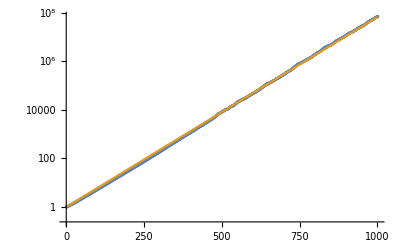

```mathematica
Show[ListLogPlot[Table[Mean[WA[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.045)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

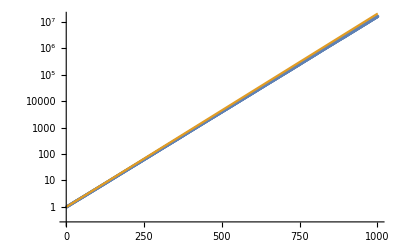

```mathematica
Show[ListLogPlot[Table[Mean[WB[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.042)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

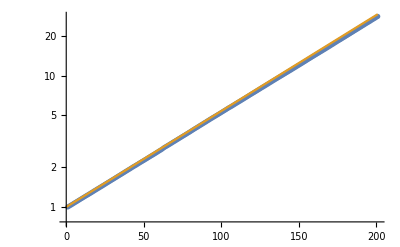

```mathematica
Show[ListLogPlot[Table[Mean[WC[[τ]]],{τ,1,201}]],LogPlot[Exp[-(-.042)τ .4],{τ,0,201},PlotStyle->ColorData[97][2]]]
```

```mathematica
mat=Table[{{Mean[WA[[τ]]],Mean[WI1AB[[τ]]]/Sqrt[Mean[WI4AB[[τ]]]],Mean[WI1AC[[τ]]]/Sqrt[Mean[WI4AC[[τ]]]]},{Mean[WI1AB[[τ]]]/Sqrt[Mean[WI4AB[[τ]]]],Mean[WB[[τ]]],Mean[WI1BC[[τ]]]/Sqrt[Mean[WI4BC[[τ]]]]},{Mean[WI1AC[[τ]]]/Sqrt[Mean[WI4AC[[τ]]]],Mean[WI1BC[[τ]]]/Sqrt[Mean[WI4BC[[τ]]]],Mean[WC[[τ]]]}},{τ,1,nstep+1}];
```

```mathematica
NMeas=Length[WA[[1]]]
```

10000

```mathematica
NBoot=200;
```

```mathematica
bootIndices=RandomInteger[{1,NMeas},{NBoot,NMeas}];
```

```mathematica
bootmat=Table[Print[b];Table[{{Mean[WA[[τ,bootIndices[[b]]]]],Mean[WI1AB[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AB[[τ,bootIndices[[b]]]]]],Mean[WI1AC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AC[[τ,bootIndices[[b]]]]]]},
{Mean[WI1AB[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AB[[τ,bootIndices[[b]]]]]],Mean[WB[[τ,bootIndices[[b]]]]],Mean[WI1BC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4BC[[τ,bootIndices[[b]]]]]]},
{Mean[WI1AC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AC[[τ,bootIndices[[b]]]]]],Mean[WI1BC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4BC[[τ,bootIndices[[b]]]]]],Mean[WC[[τ,bootIndices[[b]]]]]}},{τ,1,nstep+1}],{b,1,NBoot}];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

123

124

125

126

127

128

129

130

131

132

133

134

135

136

137

138

139

140

141

142

143

144

145

146

147

148

149

150

151

152

153

154

155

156

157

158

159

160

161

162

163

164

165

166

167

168

169

170

171

172

173

174

175

176

177

178

179

180

181

182

183

184

185

186

187

188

189

190

191

192

193

194

195

196

197

198

199

200

```mathematica
t0s=Table[Table[t0,{tref,t0+50,nstep,50}],{t0,100,nstep-50,50}];
```

```mathematica
tRs=Table[Table[tref,{tref,t0+50,nstep,50}],{t0,100,nstep-50,50}];
```

```mathematica
eigenSys=Table[Table[Eigensystem[{mat[[tref]],mat[[t0]]}],{tref,t0+50,nstep,50}],{t0,100,nstep-50,50}];
```

```mathematica
booteigenSys=Table[Table[Table[Eigensystem[{bootmat[[b,tref]],bootmat[[b,t0]]}],{tref,t0+50,nstep,50}],{t0,100,nstep-50,50}],{b,1,NBoot}];
```

```mathematica
t0s=Table[Table[t0,{tref,t0+20,nstep,20}],{t0,100,nstep-20,20}];
```

```mathematica
tRs=Table[Table[tref,{tref,t0+20,nstep,20}],{t0,100,nstep-20,20}];
```

```mathematica
eigenSys=Table[Table[Eigensystem[{mat[[tref]],mat[[t0]]}],{tref,t0+20,nstep,20}],{t0,100,nstep-20,20}];
```

```mathematica
booteigenSys=Table[Table[Table[Eigensystem[{bootmat[[b,tref]],bootmat[[b,t0]]}],{tref,t0+20,nstep,20}],{t0,100,nstep-20,20}],{b,1,NBoot}];
```

```mathematica
eigenVecs=eigenSys[[All,All,2]];
```

```mathematica
eigenVals=eigenSys[[All,All,1]];
```

```mathematica
booteigenVecs=booteigenSys[[All,All,All,2]];
```

```mathematica
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
```

```mathematica
CI[boots_]:=Block[{LQ,UQ,upper,lower},
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
upper=Quantile[boots,UQ];
lower=Quantile[boots,LQ];
(upper-lower)/2];
```

```mathematica
eigenVecs[[1,1,1,1]]
```

-0.32886

```mathematica
CI[booteigenVecs[[1,-2,-2,1]]]
```

0.699507

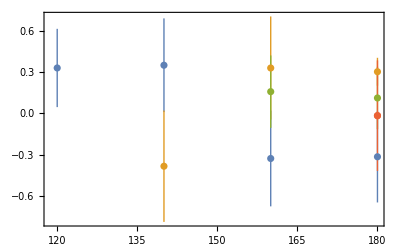

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,1]],CI[-Re[booteigenVecs[[All,t0,tR,1,1]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

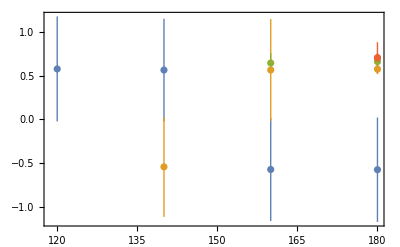

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,2]],CI[-Re[booteigenVecs[[All,t0,tR,1,2]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

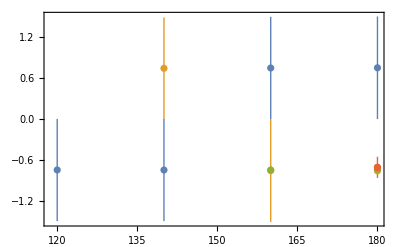

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,3]],CI[-Re[booteigenVecs[[All,t0,tR,1,3]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

```mathematica
t0I=2;tRI=2;
```

```mathematica
t0s[[t0I,tRI]]
```

120

```mathematica
tRs[[t0I,tRI]]
```

160

```mathematica
c11=Around[-eigenVecs[[t0I,tRI,1,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,1]]]]]
```

0.30.4

```mathematica
c12=Around[-eigenVecs[[t0I,tRI,1,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,2]]]]]
```

0.60.6

```mathematica
c13=Around[-eigenVecs[[t0I,tRI,1,3]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,3]]]]]
```

-0.80.8

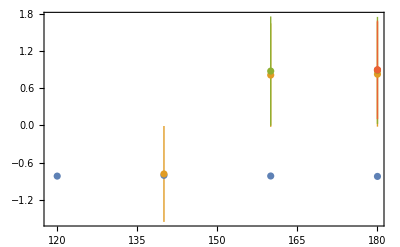

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,2,1]],CI[-Re[booteigenVecs[[All,t0,tR,2,1]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

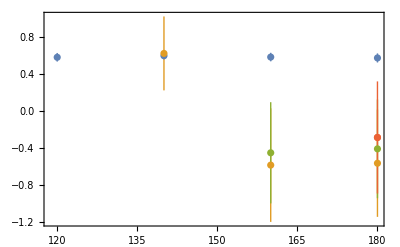

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,2,2]],CI[-Re[booteigenVecs[[All,t0,tR,2,2]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

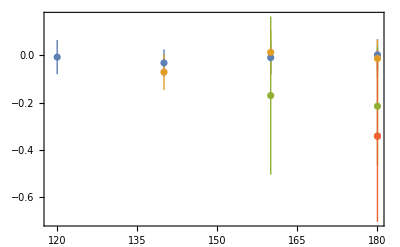

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,2,3]],CI[-Re[booteigenVecs[[All,t0,tR,2,3]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

```mathematica
c21=Around[-eigenVecs[[t0I,tRI,2,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,1]]]]]
```

0.80.8

```mathematica
c22=Around[-eigenVecs[[t0I,tRI,2,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,2]]]]]
```

-0.60.6

```mathematica
c23=Around[-eigenVecs[[t0I,tRI,2,3]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,3]]]]]
```

0.010.09

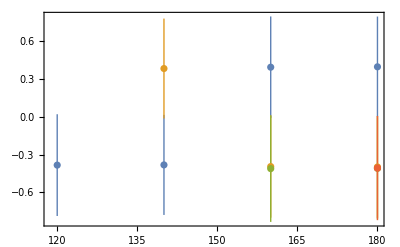

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,3,1]],CI[-Re[booteigenVecs[[All,t0,tR,3,1]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

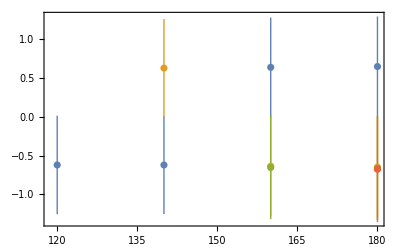

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,3,2]],CI[-Re[booteigenVecs[[All,t0,tR,3,2]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

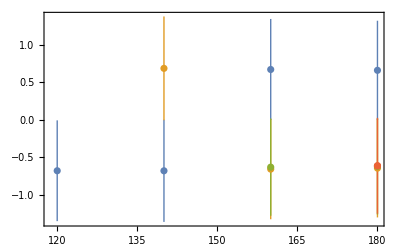

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,3,3]],CI[-Re[booteigenVecs[[All,t0,tR,3,3]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

```mathematica
c31=Around[-eigenVecs[[t0I,tRI,3,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,3,1]]]]]
```

-0.40.4

```mathematica
c32=Around[-eigenVecs[[t0I,tRI,3,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,3,2]]]]]
```

-0.60.6

```mathematica
c33=Around[-eigenVecs[[t0I,tRI,3,3]],CI[-Re[booteigenVecs[[All,t0I,tRI,3,3]]]]]
```

-0.70.7

```mathematica
matHam3pt=Table[{{Mean[HamA[[τ]]WA[[τ]]],Mean[HamI1AB[[τ]]WI1AB[[τ]]]/Sqrt[Mean[WI4AB[[τ]]]],Mean[HamI1AC[[τ]]WI1AC[[τ]]]/Sqrt[Mean[WI4AC[[τ]]]]},{Mean[HamI1AB[[τ]]WI1AB[[τ]]]/Sqrt[Mean[WI4AB[[τ]]]],Mean[HamB[[τ]]WB[[τ]]],Mean[HamI1BC[[τ]]WI1BC[[τ]]]/Sqrt[Mean[WI4BC[[τ]]]]},{Mean[HamI1AC[[τ]]WI1AC[[τ]]]/Sqrt[Mean[WI4AC[[τ]]]],Mean[HamI1BC[[τ]]WI1BC[[τ]]]/Sqrt[Mean[WI4BC[[τ]]]],Mean[HamC[[τ]]WC[[τ]]]}},{τ,1,nstep+1}];
```

```mathematica
bootmatHam3pt=Table[Print[b];Table[{{Mean[HamA[[τ,bootIndices[[b]]]]WA[[τ,bootIndices[[b]]]]],Mean[HamI1AB[[τ,bootIndices[[b]]]]WI1AB[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AB[[τ,bootIndices[[b]]]]]],Mean[HamI1AC[[τ,bootIndices[[b]]]]WI1AC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AC[[τ,bootIndices[[b]]]]]]},{Mean[HamI1AB[[τ,bootIndices[[b]]]]WI1AB[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AB[[τ,bootIndices[[b]]]]]],Mean[HamB[[τ,bootIndices[[b]]]]WB[[τ,bootIndices[[b]]]]],Mean[HamI1BC[[τ,bootIndices[[b]]]]WI1BC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4BC[[τ,bootIndices[[b]]]]]]},{Mean[HamI1AC[[τ,bootIndices[[b]]]]WI1AC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4AC[[τ,bootIndices[[b]]]]]],Mean[HamI1BC[[τ,bootIndices[[b]]]]WI1BC[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4BC[[τ,bootIndices[[b]]]]]],Mean[HamC[[τ,bootIndices[[b]]]]WC[[τ,bootIndices[[b]]]]]}},{τ,1,nstep+1}],{b,1,NBoot}];
```

1

2

3

$Aborted

```mathematica
cMat={{c11[[1]],c12[[1]],c13[[1]]},{c21[[1]],c22[[1]],c23[[1]]},{c31[[1]],c32[[1]],c33[[1]]}}
```

{{0.328615,0.566844,-0.755447},{0.811393,-0.584363,0.0127436},{-0.395507,-0.637551,-0.661137}}

```mathematica
eigen3pt=Table[Table[(cMat.matHam3pt[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,3}];
```

```mathematica
eigen2pt=Table[Table[(cMat.mat[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,3}];
```

```mathematica
thresh=-(0.21485 4/3)^2/2
```

-0.0410316

```mathematica
eigenHam=Table[eigen3pt[[n]]/eigen2pt[[n]],{n,3}];
```

```mathematica
stop={201,201,201};
```

```mathematica
matHamEM=Table[Table[{(τ-1).4,Around[matHam3pt[[τ,n,n]]/mat[[τ,n,n]],CI[bootmatHam3pt[[All,τ,n,n]]/bootmat[[All,τ,n,n]]]]},{τ,stop[[n]]}],{n,3}];
```

```mathematica
bootc11=-Re[booteigenVecs[[All,t0I,tRI,1,1]]];
```

```mathematica
bootc12=-Re[booteigenVecs[[All,t0I,tRI,1,2]]];
```

```mathematica
bootc13=-Re[booteigenVecs[[All,t0I,tRI,1,3]]];
```

```mathematica
bootc21=-Re[booteigenVecs[[All,t0I,tRI,2,1]]];
```

```mathematica
bootc22=-Re[booteigenVecs[[All,t0I,tRI,2,2]]];
```

```mathematica
bootc23=-Re[booteigenVecs[[All,t0I,tRI,2,3]]];
```

```mathematica
bootc31=-Re[booteigenVecs[[All,t0I,tRI,3,1]]];
```

```mathematica
bootc32=-Re[booteigenVecs[[All,t0I,tRI,3,2]]];
```

```mathematica
bootc33=-Re[booteigenVecs[[All,t0I,tRI,3,3]]];
```

```mathematica
bootcMat=Table[{{bootc11[[b]],bootc12[[b]],bootc13[[b]]},{bootc21[[b]],bootc22[[b]],bootc23[[b]]},{bootc31[[b]],bootc32[[b]],bootc33[[b]]}},{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(cMat.bootmatHam3pt[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,3}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(cMat.bootmat[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,3}],{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(bootcMat[[b]].bootmatHam3pt[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,3}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(bootcMat[[b]].bootmat[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,3}],{b,NBoot}];
```

```mathematica
booteigenHam=Table[Table[booteigen3pt[[b,n]]/booteigen2pt[[b,n]],{n,3}],{b,NBoot}];
```

```mathematica
eigenHamEM=Table[Table[{(τ-1).4,Around[eigenHam[[n,τ]],CI[booteigenHam[[All,n,τ]]]]},{τ,stop[[n]]}],{n,3}];
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
<<MaTeX`
```

```mathematica
TrimBleed[p2_]:=Show[p2,With[{d=.2},Graphics[{White,FilledCurve[{{Line[ImageScaled/@{{-d,-d},{-d,1+d},{1+d,1+d},{1+d,-d}}]},{Line[Scaled/@{{0,0},{0,1},{1,1},{1,0}}]}}]}]],ImagePadding->{{70,10},{45,10}}]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
origlegend=PointLegend[Table[Directive[ColorData[97][ii]],{ii,3}],{MaTeX["b=5a",Magnification->0.8],MaTeX["b=100a",Magnification->0.8],MaTeX["b=50a",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,3}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Dimensions@matHamEM
```

{3,201,2}

```mathematica
EMPorig=TrimBleed[Show[ListPlot[matHamEM,Joined->False,Frame->True,PlotLegends->Placed[origlegend,{.65,.2}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,nstep .4},{-.05,-.04}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\left<\\psi|H(\\tau)|\\psi \\right>",Magnification->1.2]}]]
```

-Graphics-

```mathematica
Export["~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/EMorig.pdf",EMPorig]
```

```mathematica
GEVPlegend=PointLegend[Table[Directive[ColorData[97][ii]],{ii,3}],{MaTeX["n=0",Magnification->0.8],MaTeX["n=1",Magnification->0.8],MaTeX["n=3",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,3}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

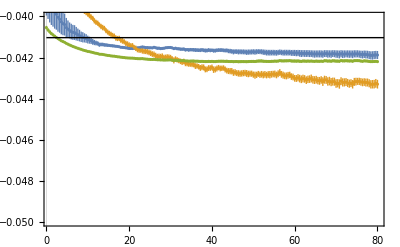

```mathematica
EMPGEVP=Show[ListPlot[eigenHamEM,Joined->False,Frame->True,PlotLegends->Placed[GEVPlegend,{.65,.2}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,nstep .4},{-.05,-.04}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\left<n|H(\\tau)|n \\right>",Magnification->1.2]}]
```

```mathematica
Export["~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/EMGEVP.pdf",EMPGEVP]
```

```mathematica
eigenHamEM[[1,150]]
```

{59.6,-0.0415160.000020}

```mathematica
eigenHamEM[[2,150]]
```

{59.6,-0.043180.00009}

```mathematica
eigenHamEM[[3,150]]
```

{59.6,-0.042190.00004}

```mathematica
eigenHamEM[[1,150,2]]-thresh
```

-0.0004840.000020

```mathematica
eigenHamEM[[2,150,2]]-thresh
```

-0.002150.00009

```mathematica
eigenHamEM[[3,150,2]]-thresh
```

-0.001160.00004

```mathematica
mb=4.77050;
```

```mathematica
(eigenHamEM[[1,150,2]]-thresh)mb 1000
```

-2.310.10

```mathematica
(eigenHamEM[[2,150,2]]-thresh)mb 1000
```

-10.30.4

```mathematica
(eigenHamEM[[3,150,2]]-thresh)mb 1000
```

-5.530.18

## 2x2

```mathematica
dropboxDir="~/Dropbox/"
```

~/Dropbox/

```mathematica
HamA=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WA=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]]
```

{1}
 |  |  |  |

```mathematica
HamB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac100.0_masses[1, -1, 1, -1].h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0412148,-0.0413353,-0.0411332,-0.0411577,-0.0412019,-0.0411587,-0.0414699,-0.0411658,-0.0411418,-0.041218,-0.0412386,-0.0411991,-0.0411757,-0.0412905,9972,-0.0415298,-0.041187,-0.0411432,-0.0411844,-0.0411834,-0.0411601,-0.0420641,-0.041204,-0.0413386,-0.0411935,-0.0413913,-0.0415488,-0.0414287,-0.0411958},999,{1}}
 |  |  |  |

```mathematica
WB=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket1.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac100.0_masses[1, -1, 1, -1].h5",{"Datasets","Ws"}][[All,All,1]]
```

{1}
 |  |  |  |

```mathematica
HamI1=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI1=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I1.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{4.20555,7.27746,10.3117,6.26366,3.89611,6.39446,2.16444,6.90196,11.2051,3.50358,3.89114,4.20782,5.28951,3.49192,6.12441,3.72277,9968,3.48901,27.7533,5.17294,6.29094,8.4774,4.4433,4.66776,6.32563,1.44424,6.2758,4.54782,4.05183,3.58733,1.90593,1.71628,6.04006},999,{1}}
 |  |  |  |

```mathematica
HamI4=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Hammys"}][[All,All,1]]
```

{{-0.0388288,-0.0378796,-0.039256,-0.0326763,-0.0312383,-0.0371432,-0.0328664,-0.03891,-0.0427955,-0.0343446,-0.041261,-0.0352431,-0.0375306,-0.0311602,9972,-0.0352492,-0.0445102,-0.0389954,-0.0349016,-0.0363893,-0.0380582,0.010713,-0.0466088,-0.0335564,-0.0312258,-0.0465905,-0.0161461,-0.0075631,-0.0438229},999,{1}}
 |  |  |  |

```mathematica
WI4=Import[dropboxDir<>"physics/projects/heavy_quark_nuclei/Hammys_LO_dtau0.4_Nstep1000_Nwalkers10000_Ncoord4_Nc3_nskip100_Nf4_alpha0.21485_spoila1_spoilaket20.0_spoilfhwf_spoilS1_log_mu_r0.0_wavefunction_product_potential_full_afac5.0_I4.h5",{"Datasets","Ws"}][[All,All,1]]
```

{{17.6867,52.9614,106.331,39.2335,15.1796,40.8891,4.68479,47.637,125.555,12.2751,15.1409,17.7057,27.9789,12.1935,37.5084,13.859,9968,12.1732,770.243,26.7593,39.5759,71.8664,19.7429,21.788,40.0136,2.08581,39.3856,20.6827,16.4174,12.8689,3.63255,2.94561,36.4824},999,{1}}
 |  |  |  |

```mathematica
WI4[[1]]
```

{17.6867,52.9614,106.331,39.2335,15.1796,40.8891,4.68479,47.637,125.555,12.2751,15.1409,17.7057,27.9789,12.1935,37.5084,13.859,18.7711,549.999,94.8718,3253.82,223.163,7.20979,139.313,147.848,81.3206,26.2719,1632.26,45.9351,4.16116,5.34039,46.1021,94.3527,7.60078,23.2124,15.9086,4.17017,20.1228,6.24811,52.7435,108.608,8.86306,67.7675,17.7533,102.568,123.271,3.82641,94.7357,13.0222,36.3652,1560.51,8.67273,7.71491,3.27648,68.9161,389.934,19.6434,168.911,6.52851,12.5341,182.687,2250.65,4.64027,7.48631,227.458,17.287,9.10562,8.82655,1229.99,10.1944,22.5419,56.1362,55.5007,5.47301,16.7918,28.8021,72.4645,136.765,14.8504,42.3612,3.72948,60.2299,94.3452,52.2878,9.75151,13.9289,4.84607,9.07813,129.601,18.7907,3.3864,6.74692,5.03132,10.1099,19.5812,88.2376,11.4631,5.67271,134.576,8.19534,109.443,11.6387,28.7385,11.3726,12.8647,8.19332,13.4113,3.62251,7.31034,145.85,46.7573,7.99708,17.0319,180.663,264.856,349.808,4.03979,16.5202,216.951,5.23637,19.9701,45.2805,53.3477,3.50645,11.8899,17.9671,54.0951,92.5259,10.1015,4.72185,4.6622,3.88711,22.7878,5.04857,11.9322,5.41173,6.78804,10.6975,20.773,2.88971,154.165,18.7899,39.6697,15.8911,1506.42,34.0339,643.467,32.7659,20.2086,17.0277,13.0426,2.80561,5.71518,13.3353,2.94633,199.477,17.3712,86.5509,10.2975,124.164,63.6194,20.892,4.1088,3.13607,48.9256,4.02533,23.0559,145.493,13.,114.071,11.1507,925.573,7.04123,3.53151,7.08212,14.1087,12.9192,10.7143,24.8824,22.4174,13.5326,6.61226,409.663,49.9998,22.1197,6.33081,8758.09,5.40941,82.9584,59.6931,24.6975,66.0987,27.9876,19.3846,50.9362,2.71607,7.17233,19.0879,236.596,205.128,64.0739,23.3163,104.091,244.005,30.066,73.98,30.5168,17708.2,13.8708,60.3642,140.208,21.532,176.147,31.5348,31.5348,86.8161,16.2048,39.6415,514.099,4.5244,9.95368,31.2507,15.1192,148.636,43.6584,36.3841,152.933,18.4024,12.2331,40.3592,1588.01,290.734,21.822,11.8774,13.9425,2.96099,24.2733,16.3451,62.2145,6.58258,19.7933,268.52,298.534,42.6582,18.1402,37.2595,6.74979,32.5399,90.1816,53.134,24.3858,63.1814,13.5132,13.7721,79.677,43.5665,33.3484,38.6741,6.59469,9.86513,5.84115,26.3647,26.0322,95.0619,8.33028,69.8254,19.9188,46.3524,14.1369,14.3016,10.2916,4.44713,4.79878,10.816,11.4906,10.2148,17.5303,75.2673,58.6226,7.57902,232.571,7.08422,30.1538,281.703,8.24799,4.57059,12.2309,247.524,21.3881,17.6928,12.5276,14.9,21.1556,6.15188,93.7299,14.3262,5.00681,601.827,22.5013,6.98322,14.7284,13.4653,24.2004,16.648,9.1702,81.3006,5.7777,3202.65,39.3662,3.30286,7.07993,23.28,60.3029,6.11526,11.3091,15.7352,4.40822,13.7946,26.7786,93.8844,2154.19,32.035,15.1795,37.5405,6.52096,13.1185,12.9633,12.5118,4.28677,3.88406,13.6312,8.94834,1100.38,971.557,7.51373,13.995,298.038,6.44266,66.09,57.1015,5.64633,8.52956,63.6154,78.3688,130.205,14.4746,41.1579,21614.3,31.8232,17.8669,95.5459,18.9608,719.95,5.90094,30.9222,26.0895,379.862,24.8443,18.2238,8.34468,21.5169,17.6856,57.4729,1811.27,9.21954,47.2415,43.9397,7.41446,195.745,208.82,8.78808,125.3,153.722,5.44528,81.3361,9.34993,5.79915,20.787,108.235,190.574,137.555,43.9959,151.076,81.9398,8.21661,9.2748,18.2357,35.9879,17.6252,28.0163,13.0314,125.338,7.08541,12.8381,11.1194,32.1343,39.0044,18.3878,9.63517,6.90386,101.932,2715.86,4.06905,29.5982,23.9999,2481.04,9.86028,14.0413,8.07433,14.6555,82.2604,365.309,157.088,27.9169,19.6396,2.99248,14.6565,47.7808,279.329,5.1676,17.8534,5802.76,10.8675,13.138,42.4149,10.4281,46.2574,23.8418,173.88,19.3781,9.02163,19.1753,8.32555,103.64,10.1542,55.1448,5.01655,21.6709,6.20361,10.2522,8.94173,76.4403,124.929,30.4543,19.1764,13.1193,176.731,348.414,23.6735,7.54074,8.78703,2.77351,4.13443,27.7264,15.2377,11.3017,167.347,16.4542,103.721,21.9591,173.382,6.79012,23.829,20.2117,141.708,4.54288,5.43987,44.3615,253.577,4.44353,4.01931,91.5255,29.3984,81.5921,6.46283,161.018,5.35414,22.2008,9.10259,8.51992,74.7693,59.687,28.1708,294.639,11.2471,15.7532,18.3666,5.0174,61.8987,63.2893,5.20656,6.76326,31.4103,14.9983,50.8037,148.275,4.68218,114.094,84.2596,13.7987,90.6023,1338.28,13.8289,40.045,10.2676,19.1532,12.4907,9.25979,146.967,105.145,6.79509,7.42696,61.0432,34.9876,26.3145,30.936,12.0029,13.6922,15.3967,991.371,17.4964,4.11692,3831.55,31.942,57.8591,10.4328,20727.3,6.442,67.5171,11.9274,146.754,8.93572,10.3503,68.7908,6.47256,192.129,1217.85,12.0754,26.8121,161.435,370.635,5.73872,21.4654,5.90108,12.3371,231.724,27.8902,3.79096,4.18854,57.7668,4.26356,209.855,7.55829,3945.34,7.91286,277.823,5.98811,10.6898,13.5904,5.47264,9.6601,13.423,19.5667,19.5667,19.5667,19.5667,17.6395,21.4099,19.167,290.753,10.5818,21.1039,3.8238,8.46457,113.2,9.66414,9.70134,17.4838,15.454,14.2558,18.7185,33.7399,38.902,3.71659,13.0306,85.2902,33.8799,34.5072,24.0936,2.99712,87.2928,14.7119,7054.92,44.1662,41.9546,3.78078,49.7771,24.1439,1290.35,37.9724,52.8292,3.31776,15.3348,5.83969,77.8607,91.1777,525.312,3.74218,28.2377,34.27,258.936,798.134,8.18576,39.2513,19.9022,5.79783,9.71756,7.87683,14.9862,149.321,61.4423,12.6943,84.7057,94.2303,1127.22,4.92179,291.939,15.9158,5.98923,151.707,4.30221,23.6904,630.333,43.7378,14.449,489.109,18.6268,509.986,5.28527,166.86,16.2623,276.696,253.167,34.3816,7762.94,178.997,158.536,6.5971,23.5439,8.9178,13.1774,9.86592,7.2835,5.34863,44.2716,1912.31,830.289,76.3196,19.9263,17.3602,33.2274,87.4343,82.7761,10.8931,29.6465,5.86633,219.099,29.1867,543.731,6.07106,10.1393,219.564,71.6384,13.5379,8.00333,15.6026,78.8529,5.07289,4.22704,450.351,26.7685,6.9234,34.783,216.177,16.4235,13.995,15.9422,43.4328,277.365,51.8032,16.5629,6.2461,8.14913,5.16626,7.09997,31.8574,9.32831,231.213,24.3692,33.2507,244.629,5.80332,34.3573,165.409,4.94975,8.48643,5.57838,28.2991,15.9808,9.86061,53.6918,36.4389,6.62285,8.98741,33.1974,46.1865,57.2218,25.2896,159.011,36.171,7.70899,24.2595,67.1623,4.30222,19.3906,528.526,992.434,36.524,3.81505,8.31077,63.2385,4.20011,3.86131,123.021,429.147,10.1866,7.79994,19.4048,65.0079,11.3665,2.37009,100.157,82.2756,10.4485,1543.93,20.0337,20.4088,17.7468,92.6618,18.7218,26.6449,121.102,89.1104,10.1172,4.76115,229.576,73.7198,13.4863,30.7779,92.8551,78.5401,16.0343,8.22741,3.48087,5.75814,6.58038,10.5002,1124.74,6.34187,7.36767,23.9327,473.306,17.8462,4.96079,5.88232,11.7005,247.176,22.2666,6.8355,38.4001,100.332,69.9046,361.511,512.834,3.07027,3.02107,3.40021,70.9302,4.76064,3.58854,5.23774,29.8897,5.48376,5.80845,9.42983,107.322,13.1137,13.7192,18.3461,6.95821,9.71371,18.3355,65.6434,14.2638,5.27486,54.2838,11.4286,29.2983,16.5665,36.2002,8.58414,10.5485,25.5839,5.44416,11.8755,1482.84,101.949,10.9831,14.3658,3.67144,87.7642,17.9933,5.42813,7.95334,17.128,7.49643,6.48814,47.3087,5.29706,19.9184,59.5759,10.7902,38.1896,20.6539,13.4707,8.86787,15.4494,7.69911,4.9603,319.323,29.2638,195.303,23.5891,5.48202,49.6162,52.4692,44.812,269.917,6.41333,247.586,141.679,15.1095,602.492,29.3733,28.1929,97.515,23.1328,41.2547,10.2394,3.53138,53.7667,9.45459,23.4269,139.543,13.0589,53.9866,12.9822,32.218,1130.88,17.1381,1219.25,99.0078,9.81246,141.046,53.0231,2.21707,25.5653,11.0068,3.15861,26406.6,19.6428,10.1429,2.80859,42.3167,8.50143,13.3127,27.6748,58.0976,34.8446,37.3799,282.807,5.33639,10.5028,286.87,5.70351,36.5784,16.8637,15.856,28.5603,840.86,6.75563,1996.22,4.3938,11.7365,4514.61,1576.6,432.179,22.1993,14.0833,3.88649,10.8497,32.4263,245.5,73.3464,761.063,3.95007,7.62791,8.79689,9.38674,8.66886,9.05174,15.6112,7.03513,3.4411,23.8343,6.67333,59.6325,10.8402,27.3806,29.9283,61.8546,5.64973,28.7079,10.838,3.02181,19.9096,6.13181,2821.74,375.839,45.0128,239.739,46.2784,23.014,16.9202,44.9224,3.39039,32.9548,19.0575,6.13646,24.4118,173.398,37.6918,286.134,282.531,94.9075,75.9741,5.71177,24.7185,80.222,1123.81,4.01199,6.75271,8.99078,89.4837,18.0599,59.747,66.167,220.012,93.4635,95.7275,53.5688,10.1686,10.1644,3.90962,7.14863,7.6082,5.3397,32.5844,46.7489,11.9355,172.971,21.9495,37.7745,36.4569,18.1571,8.63609,8.61301,39.7413,73.7465,13.4158,7.84175,14.6806,33.2808,3.41788,11.6189,90.7,26.8233,9.48976,3.84625,3.83974,5.55661,311.7,493.935,507.757,23.2642,9.21892,29.6165,338.53,58.5212,2909.12,6.91361,6.43714,356.258,488.209,7.95756,112.162,5.43254,255.943,61.5487,13.6696,2238.75,98.7236,14.3219,20.9793,28.6877,34.8252,22.9937,104.361,7.94608,5.27026,4.36283,1073.28,5.71854,2504.25,7.80555,411.471,9.72843,5.13531,141.075,4.27672,96.9739,4.42898,5.94325,5.71327,11.5947,4.25594,15.5631,387.57,9.21396,7.43378,104.754,28.9118,166.77,9.96297,37.3848,8.67594,8.85663,83.9855,478.457,52.848,19327.4,1048.68,14.5445,282.365,357.105,34.9332,21.0601,11.1499,16.5441,94.421,570.912,9.53188,3.16926,5.1239,3.5673,6.37179,5.96935,6.90613,474.777,19.9306,28.1238,29.2102,43.4833,13.1629,3.69068,5.29862,383.47,13.5324,9.51741,375.68,14.106,13.2745,908.58,6.89733,12.693,28.8944,6.49231,15.0512,38.5321,5.05599,4.86214,869.873,336.337,10.14,21.415,5.88355,9.06082,15.0843,55185.9,4092.96,61.0593,17.0896,1840.69,6.62889,6.66025,3.95558,717.253,6.4684,56.9147,5.76159,6.15928,38.6261,5.12009,40.4159,49.279,8.31599,6.95071,27.4563,306.315,57.5076,32.0497,13.8217,104.056,76.2553,8.4798,9.74783,8.71542,177.34,7.9919,16.7067,4.33412,45.1323,10.7279,11.8409,5.65457,34.085,14.6603,19.4798,13.172,275.843,10.3413,40.5445,2360.46,175.494,34.0552,3.77099,6.68622,8.90537,82.9538,306.168,19.2641,10.7557,10.9389,27.5565,70.9823,147.787,54.8359,169.134,176.838,11.1975,155.168,4.07615,6.41461,742.8,8.03805,4.39204,30.9368,201.274,11.3547,92.0095,15.6204,690.989,23.6117,16.6408,20.3948,21.4809,21.2344,5.31873,36.9054,4.05422,34.9738,187.962,4.91214,28.8179,6.20462,48.9051,2.88783,93.4291,10.0295,44.2731,46.4766,440.855,2.65545,14.5035,1136.1,54.5677,6.18103,82.3481,381.247,28.4534,12.8626,19.6296,8.23226,61.8937,159.472,100.738,6.02935,1790.34,11.6824,6.34352,4.52194,318.121,30.9248,5.77023,9.85594,92.69,9.76951,7.79799,70.9069,43.8021,75.169,294.816,4.8547,7.43765,139.048,49.7368,54.7135,12.6206,3.62105,128.44,67.6204,13.5907,166.233,51.5943,2.87035,8.94241,195.78,21.7868,138.566,226.047,12.8654,97.7093,1220.1,124.689,27.4081,10.8092,3.89482,67.5274,57.5937,37.2372,68.2402,131.731,11.6019,5.11876,6.72129,233.866,51.194,12.6695,427.563,4.13825,5.80082,5.57106,449.333,16.8196,7.11682,62.7655,511.839,148.892,20.9657,79.5318,21.3662,223.523,13.9861,21.2521,7.12141,78.2336,17.4961,8.38131,12.5426,16.7056,9.03939,24.1485,11.0727,218.696,7.91485,30.8814,8.5641,24.4904,29661.3,8.45645,27.033,101.756,8.01068,38.4126,20.5408,99.0577,21.7723,30.4242,84.6466,38.6481,40.8999,29.0049,9.31751,2.82227,5.14865,21.644,43.1522,21.6646,111.61,9.09779,234.657,3.38046,21.3359,56.9475,11.6136,18.6179,15.6073,31.7607,4.63909,9.93402,11.7665,1187.51,32.1169,16.8586,29.4777,14.8486,30.4569,126.5,8.74046,145.395,6.94641,11.7099,400.535,28.7946,15.405,7.22535,10.5837,5.67936,7.94728,9.61117,115.155,31.0733,15.0726,157.876,5.46243,6.09813,6.59275,9.74857,98.2675,7.43934,12.177,13.7378,16.9582,4.41737,11.3846,9.69768,4413.85,5.68455,5.17842,15.5226,3.38386,6.70387,3.13715,2721.04,5.54661,8.83584,300.612,4.10755,11.8679,11.448,17.7669,21.8492,30.5845,38.7434,6.82111,92.8907,6.66502,10.5743,20.0984,7.43799,192.077,20.6444,14.4124,9.11025,6.80319,46.632,26.45,13.1454,27.3333,21.4717,5.66102,14.8681,11.1256,14.4706,3.48059,224.882,9.39396,262.709,14.0315,16.3277,22.6617,22.6617,14.1074,14.1051,19.5938,19.8635,24.451,8.41745,131.245,2615.23,193.815,113.385,676.531,870.952,5.48737,55.9779,46.9093,6.3974,12.6457,8.72589,81.9904,4.12069,11.2925,15.0148,5.57193,5.01781,348.398,20.8449,420.804,420.804,20.9309,10.0125,3601.01,15.9926,7.80493,16.6021,111.723,33.951,61.0441,14.9707,479.63,88.4228,9.20263,33.362,3.83942,155.495,341.569,72.7384,63.4727,17.9508,41.2453,11.0824,8.84804,11.3061,46.4043,14.6044,36.5999,89.4394,35.3821,113.968,16.6813,7.33437,16.672,43.0924,20.7273,9.97597,6.63199,159.197,25.1393,34.6721,11.0805,82.4834,98.7506,13.0342,23.4584,81.76,10.2418,16.9895,11.7405,5.17123,38.8814,8.69788,34.9859,40.082,15.7009,4.87335,9.30648,57.8087,31.0993,18.2659,10.2701,91.2479,10.7895,23.2227,10.6741,28.0375,32.1826,19.5235,133.478,107.001,72.0186,43.7854,9.87873,786.29,30.6699,226.546,34.8135,90.0453,10.8832,20.4235,9.12541,3.67291,14.3783,494.646,45.0136,888.336,10.4089,7.65125,95.634,52.3958,14.2766,24.1635,8.44232,213.856,7.974,15.541,3.33304,13.037,16.9203,16.1528,11.7739,23.2401,10.0479,14.7514,196.092,15.8763,4.68986,297.966,39.5416,25.5686,8.9756,15.7639,8.22398,10.6393,802.02,21.6568,5.39857,19.5437,43.6288,43.6288,17.6709,12303.6,4064.97,14.341,16.6846,50.9498,129.668,277.978,37.715,203.351,24.8371,17.1022,259.019,28.0433,41.0986,52.3447,19.0509,3.12485,1103.38,5.64146,25.6898,383.959,211.643,13.3852,54.8205,13.5667,125.919,6.51942,139.374,86.2496,112.105,2.76588,18.5684,18.1331,1869.83,6.50706,331.257,12.7201,3.64035,12.6626,10.8156,18.1009,5.13132,18.3225,8.81627,13.2593,110.293,47.8423,135.729,5.2201,9.83964,12.3481,42.679,5.59608,21.0182,1544.52,16.6763,3.67943,39.3836,125.994,32.8832,10.5965,273.687,11.9509,8.39096,24.8777,23.6349,141.743,10.0576,484.453,12.2215,5.62677,125.425,64.6711,9.82494,5.19619,21.4294,3.71104,69.8342,10.1812,17.4583,86.6815,20.8558,29.4542,4.30543,11.8191,36.0654,20.8844,54.1787,17.4509,67.5668,8.6544,74.9195,10.5549,12.1759,976.339,863.025,39.3777,10.5157,39.9027,3.62077,23.1082,51.1326,13.2787,6.829,21.9898,6.81842,19.6146,55.3689,18.623,479.458,1080.24,36.8946,72.5985,156.619,24.0836,18.9451,16.9677,61.4688,38456.6,6.769,52.8923,17.8567,7.32848,40.9127,18.287,52.9604,37.8346,4.66511,11.231,14.8865,479.403,11.1321,35.8998,5.80192,92.0948,7.05275,8.99339,29.706,11.1084,26.6336,22.0285,351.019,32.5829,536.268,5.93062,34.2711,8.52836,100.834,142.428,3.86347,61.2009,125.462,4.00716,11.382,56.4574,20.1398,6.28677,27.8584,71.4037,7.76258,269.106,4.45841,127.083,280.357,43.8498,7.25274,65.7331,13.954,496.735,72.8522,79.8546,17.6293,27.2258,21.5993,91.077,12.5859,76.4447,390.493,10.269,27.4983,4.60743,751.302,48.8964,33.3962,232381.,115552.,1742.37,558.633,8.33156,30.852,361.516,11.5953,6.93302,185.847,33.8015,5.5891,8.06432,237.395,751.257,3.29808,82.0057,14.8506,4.31588,13.6697,8.63304,215.166,16.995,7.22693,8.02012,54.2009,4.84794,7.59984,4.99674,250.477,6.43884,63.0324,7.80141,632.725,78.1245,48.5597,5.29793,6.66167,8.85458,13.0929,58431.8,23.9869,6.32555,110.203,26.9013,8.92946,20.3535,38.4391,17.9808,7.96487,18.4674,12.8965,7.53039,88.141,81.6822,48.6919,4.49188,17.9749,4.13014,5.07231,9.23809,6.00469,32.293,9.21969,33.3585,27.453,4.79767,25.4939,303.748,8.02917,12.8388,5.0299,3438.09,15.4401,88.3817,713.734,8.25951,156.25,14.3385,11.1721,6.43114,26.8604,17.3355,12.6473,11.2312,48.2832,6.71607,226.845,8.20247,59.1377,5.55859,24.9149,5.74232,22.5556,38.911,54.282,23.006,69.7276,9.0088,609.852,10.2565,6.98638,19.0049,30.8976,3455.78,5.1264,27.2302,20.4876,3.85172,3.10219,221.324,29.8773,5.6055,74.3618,53.5499,21.7431,6.11159,6.47094,8.83467,6.53987,40.9697,97.7096,25.084,15.1868,72.9251,50.2821,11.4729,7.37393,13.9797,14.8845,4.82473,17.1263,12.9987,28.7024,10.7942,50.5211,5.98434,84.1018,107.234,17.1617,19.8219,14.6561,16.8862,322.146,7.51702,468.983,36.6083,27.6977,2.54955,8.89995,11.7942,18.2841,78.7121,867.913,52.9103,11.2159,3.20088,81.1794,52.9431,12.4581,31.702,75.019,29.8117,13.6084,54.831,9.80305,14.7762,139.333,602.503,47.8749,13.9127,3.82237,10.9289,6798.45,8.833,40.191,673.846,138.86,3.64453,392.286,11.8202,3.09347,5.95006,118.178,2689.09,60.1204,5.89192,73.0553,7.71638,22.2472,7.29028,27.6893,54.3786,9.18823,26.558,31.4552,8.26397,26.944,5.40383,37.0863,28.9972,44.0613,27.0648,15.8742,21.9823,45.75,13.1581,112.136,420.328,66.2733,33.1849,19.1371,7.24323,365.263,228.475,14.5772,9.09712,26.5958,12.4381,9.30883,34.7632,202.322,152.307,184.859,21.1062,25.0266,26.3775,4.27278,5.32402,4.72668,22.1981,19.3097,4.49713,3.75051,61.2808,27.2276,51.0079,17.0914,16.0732,66.7022,13.2991,20.4283,10.6613,45123.,13.1529,483.934,85.1747,4.21296,107.31,12.9281,12.6673,1067.98,8.43616,683.115,92.6372,34.9299,3.13017,6.38475,10.4929,1138.02,498.918,20.8055,8.10657,12.5969,778.141,203.85,5.21319,20.0522,13.322,39.8076,71.1512,13.9522,189.509,4.98025,49.1807,2.69313,5.63421,17.1933,97.6051,177.736,1458.51,35.2367,6.72029,26.7669,439.095,5.84745,59.9535,10.2758,11.6939,170.754,8.79658,16.751,5.53911,186.213,30.1845,14.8865,25.2146,14.0036,5.5409,52.3831,18.9807,17.9807,12.0518,14.7291,25.4444,205.482,6.45342,25.6448,9.54069,19.2534,7.82193,12.4116,24.1329,7.1368,30.5827,11.1261,6.47426,15.6041,10.6573,5.64699,7.34891,7.70434,39.1795,12.0305,3.84177,41.7753,181.271,23.291,51.9718,43.1729,19.6595,13.4912,4.65366,38.8759,171.18,3.53094,1036.07,4.9979,7.47524,53.2113,99.5881,25.1954,3.63065,3.51582,6.93399,5.17548,8.00654,46.4684,18.891,7.18671,42.3794,27.6302,4.28709,91.4802,50.5321,34.3182,11.0729,126.408,85.5685,121.307,9593.8,7.19325,100.502,42.6797,3.15125,39.3072,22.2629,48.8548,67.4184,9.49977,260.999,5.17584,105.407,60.9609,38.2595,6.98176,19.1236,171.726,20.7054,5.55504,85.9281,113.873,1418.96,55.5496,10.7903,8.21687,44.4827,844.889,12.4101,10.4013,40.2281,27.8014,5.88271,84.5004,2.70702,11.9451,25.365,122.564,75.0391,104.738,6.30888,10.8437,33.0382,62.24,22.0468,15.8596,24.9942,13.5608,7.32554,51.7524,7.1178,10.1473,225.283,21.3895,408.898,15.5178,79.0662,87.0893,75.8518,5.12783,389.341,7.42529,1008.16,24.4284,21.4546,17.2003,6.26498,13.3306,10.0373,34.0582,5.61111,8.09591,10.4051,33.08,11.6984,130365.,95.2953,56.9146,115.061,129.111,3.58575,166.822,6.83028,44.6901,18.9352,208.186,210.886,8.73273,118.055,29.0938,18.4123,38941.3,35.0349,18.13,15.5877,54.7385,798.928,436.479,10.1458,9.10196,47.1211,880.488,5.57384,44.4954,661.674,28.6523,30.3128,94.2715,105.522,125.148,14.9695,10.4752,49.5332,36.3513,45.8875,14.4135,576.647,3.42666,23.6417,165.756,12.6314,12.9545,46.0275,11.4477,1598.31,780.493,26.821,45.8181,302.496,19.1856,35.3126,513.65,123.182,21.6328,86.9736,36.8081,30.0365,73.6862,311.81,4.83779,13.4682,6.51473,38.9056,5.11133,29.7217,9.7745,50.3336,3606.29,7.04624,73.1694,5.89014,361.495,13.442,302.713,20.7887,15.1386,303.108,10.1418,45.1482,14.3101,53.3608,25.1151,19.6814,28.1205,88.3842,3.2488,233.539,4005.51,91.3037,274.268,205.015,6.91997,68.6431,4278.38,45.2159,23.4312,14.9221,4.98827,529.599,6.948,103.682,15.6024,22.4568,48.0178,28.1163,7.43046,15.8883,15.0979,12.404,6.17244,20.583,128.171,96.8953,493.694,974.351,16.7076,43.7536,45.7171,22.0443,460.839,451.591,19.9347,4.7281,9.62884,21.5813,12.6651,1322.97,5.38606,26.0698,15.9285,34.8825,9.02648,123.111,27.4332,10.026,6.51484,20.3899,5.15661,24.5304,77.641,19.8249,5.15526,5.73289,4.98846,4.92405,15.605,10.2969,161.986,109.913,166.21,237.43,98.1537,232.305,9.95326,2.87398,28.1202,101.508,5.22599,29.5029,7.1985,18.2699,10.7235,18.1694,96.5732,196.035,61.2731,174.72,21.5158,13.199,204.862,12.675,5.97976,22.1051,256.516,17.2941,19.3089,10.2181,3.95419,31.2017,29.2523,25.5915,11.7053,56.3091,2.91442,43.7622,14.9543,8.57862,37.0231,4.72196,35.934,4.42681,33.4896,172.849,14.3267,46.5549,191.127,20.798,91.0551,7.67404,29.8278,306.412,115.662,9.57275,25.4081,24.5552,24.7693,58.9121,6.07219,26.2461,4.30284,5.41507,123.154,6.8984,62.3506,452.072,13.1635,30216.2,7.68984,6.08534,27.0111,11.8099,8.28807,15.1025,16.3721,5.085,531.009,355.275,7.65459,277.13,34.0463,19255.1,34.9353,50.2196,57.9255,180.417,5.636,14.5973,15.6136,29.1421,14.2209,45.7513,5.85358,25.5139,14.8484,128.385,63.3725,1473.79,155.197,245.733,9.75104,150.149,8.03788,43.1837,3.48941,5.63476,193.731,9.16174,32.1833,6.06609,19.15,198.037,6.93132,40.2026,54.1479,5.55852,59.7026,35.6182,15.1019,8.60313,120.447,15.1384,6.20746,39.7426,10.4463,337.845,106.407,4.20834,121.44,83.574,16.712,6.00665,1015.7,3.56952,51.2241,19.1166,24.5099,114.706,98.8296,76.2551,88.7006,27.6661,237.892,15.5355,13.2792,6.186,164.584,4.75373,34.8816,16.8153,10.7715,29.2456,277.549,36.089,12.5423,26.3773,1559.53,19.0343,25.2007,8.05239,100.455,12.1994,204.604,5.56061,12.7398,36.29,275.485,62.6691,84.5639,13.2467,9.24367,23.9892,16.3464,18.4208,43.4289,912.695,19.5329,356.493,3.33876,201.13,25.1547,8889.14,7.95245,22.4367,28.3782,11.6891,11.252,11.5033,3.4611,3.35868,56.4481,4.33103,241.223,13.4586,3.27735,79.3731,5.0472,12.5393,60.7172,8.82107,12.5105,23.0545,19.8256,37.4104,15.0353,2938.61,18.5819,11.1155,12.1897,7.7906,8.82797,35.2767,31.5579,12.6007,64.7743,32.9648,11.9537,13.5142,6.79477,30.2328,62.9791,44.8699,1001.65,202.298,8.41395,18.1839,7.23078,31.109,10.1492,4.48196,19.9856,15.0803,15.6855,6.98676,22.3508,39.3178,7.19998,26.3748,24.749,5.48434,4.76385,10.5028,3.8069,30.3169,22.128,8.78664,35.3905,9.14643,6.92124,85.7875,23.2869,28.0852,46.857,6.38499,24.9183,34.6695,24.3062,86.3262,5.00445,30.5933,7.50892,40.1429,3.589,430.962,58.2103,16.247,16.2907,56.8681,30.6499,175.621,7.32066,40.0521,21.879,19.1149,9.4343,4.16741,107.726,10.7709,13.6544,1306.45,10.2174,63.868,30.6718,124.242,47.8358,15.0056,17.0803,12.4229,7.20455,43.6792,13.9936,22.8466,12.4729,1330.9,8.1884,114.417,127.956,19.1041,4.94755,5.59813,3.93592,40.0762,18.7483,50.7466,16.5561,76.0895,32.2566,32.9449,40.4623,9.39289,13.0003,30.8608,3.33791,35.2381,12.3442,22.1263,7.08475,68.5139,14.7587,15.7138,28.5963,8.53192,717.117,7.75118,25.8438,12.7298,33.4662,20.272,12.6264,53.5955,7.40282,4.37284,278.512,18.632,366.134,54.0158,146.053,47.6921,11.083,19.6429,20.5434,9.15175,20.9822,80.9683,93.8319,5.07532,217522.,17.4978,10672.6,11.8546,34.6399,7.87553,137.364,23.533,9.64054,3.89144,36.8077,7.90803,85.4715,622.65,132.845,48.6752,30.7887,16.1531,14.0541,4.18762,14.7033,19.7687,120.464,6.91534,44.207,10.2243,25.98,31.597,19.8015,4.22664,4.88111,11.8187,10.9638,216.531,7.52969,19.9405,2.88003,16.5924,20.313,26.7663,45.7705,15.5011,9.58487,53.679,13.0457,98.7338,28.4332,4.40123,4.89806,26.0651,21.3533,2155.67,56.8889,6.09111,16.4346,35.5416,48.9113,6.58,8.5018,7.62402,10.4728,27.231,15.4322,15.2745,4.75051,26.0479,61.5554,31.5261,70.5272,44.6197,2231.96,5.70257,21.2517,9.16143,18.3575,14.0427,352.751,28.2409,216.98,65.5502,42.56,514.471,4.12368,17.5283,11.6709,6.59966,19.2415,260.105,3.78357,505.472,24.0837,6.3265,6.96976,10.248,2.80404,135.553,27.8036,86.3798,20.8094,22.7206,11.9329,6.40108,7.95642,31.956,50.431,41.0148,5.70218,6.01631,4.34159,4.35195,110.557,11.2778,7.47206,25.8561,18.0033,15.6354,4427.42,35.4663,5.1865,22.6977,21.8493,24.8965,9.61113,19.0998,33.6017,324.261,74.4694,29.9045,35.1895,86.0288,38.6638,8624.95,204.049,82.1532,41.0424,5.29862,6.38841,1617.09,25.2067,14.0244,353.651,43.2285,400.637,3.34401,692.267,13.246,509.977,12.0302,43.7272,408.937,119.562,802.181,6.98018,13.9026,3046.02,10.8121,11.1873,38.5599,10.7127,36.1998,94.2466,22.6535,16.8447,8.76341,624.637,5.20794,81.3461,5.26586,84.1297,27.0967,22.2934,47.1143,17.6271,37.7561,5.47109,9.56926,6.81929,22.7019,12.079,163.68,142.346,9.13857,902.199,70.7888,9.6311,9.3386,1.8486,12.0874,6.99224,71.6421,24.4373,18.1581,943.621,95.591,49.9733,257.543,3.63497,41.9671,17.8925,3.98109,35.7722,11.8449,4.69106,28.9173,5.74112,44.1883,2.33519,181.011,127.478,55.0576,5.08567,21.0349,72.8524,40.2664,9.89168,3.15889,52.2819,9.3581,142.552,5.64686,84.6604,18.4206,181.325,47.0499,10.3555,5.02052,21.5936,52.0421,7.24609,6.2138,16.3866,35.2769,205.992,23.0843,35.6604,7.05172,5.11952,30.3674,411.412,73.2017,11.785,16.7386,82.7545,6503.36,377.767,20.9455,13.3357,42.2559,4.0857,4.71582,1346.01,11.0402,1769.34,8.33515,3246.98,132.828,13.4454,7.76738,6.69533,14.6528,9.05331,136.52,16.2527,443.326,13.0698,8.29434,61.3117,5.42374,138.131,10.346,9.75765,7.56352,12.8533,37.6122,3.67415,21.1775,43.4567,20.5976,11.6223,9.3735,26.6941,28.5344,11.8356,6.09444,395.834,134.664,38.6396,580.197,31.9345,16.5103,7.89033,35.9937,16.3305,15.9873,27.6415,55.5616,14.9517,488.078,214.824,32.4419,12.1632,22.0702,22.232,633.541,53.9198,15.3712,33.1725,10.4395,17.1439,17.233,29.2817,83.057,26.7191,28.4803,1479.66,36.0609,26.0052,11.6246,19.2057,39.0313,723.185,54.9517,18.2945,40.3688,3313.17,5.02355,5.62593,250.701,22.4882,392.263,21.2089,2590.82,231.132,18.2976,64.6486,57.2891,35.4049,16.7586,54.6555,57.8194,30.1798,227.133,11.8199,338.659,46.7069,46.7069,6.06326,21.5011,64.6453,13.986,30.229,271.047,12.5308,13.3341,42.2578,33.7617,11.7427,11.1115,5123.25,377.09,5.64697,21.4305,2098.61,5.67119,20.5731,10.5704,14.7832,63.7451,7.62989,205.467,8.42167,19.5023,14.0318,9.18189,21.9177,849.082,381.037,11.5121,16.3069,100.815,37.1888,8.39708,20.0571,55.3686,17.5786,8.65813,313.708,6.53579,5.88408,11.4203,99.0469,3.32921,177.827,28.7443,5.35284,34.0954,150.994,12.7317,4415.24,21.9647,60.2853,17.2341,23.6392,44.2562,15.2954,6.81276,27.1255,327.31,41.6401,78.739,23.6839,1545.71,54.7876,12.8926,30.7624,13.9043,9.9546,14.3089,9.55628,8.44443,707.812,42.5144,50.9441,62.7882,40.0434,6.08816,7.65435,36.6492,9.63781,50.4607,60.528,522.532,12.3584,81.0651,12.9916,200.746,1912.31,18.5122,2.50038,37.6317,9.45828,37.2069,32.6041,49.4092,14.7409,32.5182,14.3727,23.448,12.1017,5.08564,100.921,7.56863,280.632,107.389,15.3037,4.05989,10.7944,12.5697,28.1279,34.4154,15.4212,127.222,51.2392,159.97,441.629,3.7532,26.4464,15.732,8.38167,64.6271,7.1264,6.20448,7.41269,35.631,6.04498,3.68975,523.736,112.736,2718.73,28.9026,9.48564,51.3803,265.657,1054.88,128.979,167.254,12.8584,48.5062,3.56568,143.21,8.11569,9.83302,146.433,16.5419,7.61913,2.52746,13.0969,21.2477,13.7932,15.6243,54.4273,6.26843,22.5288,21.4287,5.91829,73.7541,901.681,29.253,9.29282,139.253,23.1508,5.73737,71.5149,188.253,4.0603,10.8775,13.732,32.7258,20.372,28.3365,305.733,4.30862,18.5564,4.63898,966.075,5.66308,108.866,79.1821,72.0095,2068.76,23.0818,35.538,17.6564,6.90513,10.0561,13.9279,7.34454,5.74786,268.122,86.1478,14.9318,23.1734,13.5974,442.906,11.0346,26.4395,17.5585,6.64435,17.1784,156.279,21.2062,7.1707,232.745,78.6565,23.6639,52.7046,22.6861,4.78203,3.13751,12.9005,645.984,46.5911,30.3998,3.34463,199.206,14.6463,172.589,32.3372,17.9393,36.7588,6.02717,123.341,39.1179,35.2471,45.4082,67.5811,27.5884,13.9651,13.0431,9179.77,5.89587,15.9078,5.82453,11.9613,9.23099,316.6,50.2923,9.97078,10.2554,19.1453,159.462,9.51506,12.5653,5.14244,3.10825,126.673,35.0332,16.4403,4.71928,26.1459,43.7945,18.3682,63.8484,5028.14,374.769,12.0567,27.8091,43.7788,35.7196,35.3597,37.5235,34.8056,9.23707,72.442,7.65075,58.32,38.3973,15.8235,18.7456,6.08179,146.881,18.9632,161.161,43.1113,92.4671,10.7113,48.632,18.029,29.5907,6.52429,41.0293,35.448,35.448,11.8169,26.2772,13.8362,24.4201,7.67802,140.708,4.66334,4.60858,9.30997,43.2144,85.2659,9.27076,58.6506,102.175,399.474,12.1363,16.9381,24.9057,18.5372,3090.46,15.7573,4.60555,67.5133,8.55992,42.2976,18.7496,15.8896,3.21198,32.3195,1252.3,22.285,7.92245,15.1122,6.65971,18.3866,12.748,108.166,28.581,28.5229,56.582,206.796,7677.64,9.12446,4.20942,58.845,30.0385,8.21602,8.5259,7.39319,32.7699,24.8983,5.41608,3.12652,154.754,3.50727,464.749,44.9465,24.8904,362.094,5.84426,5.35656,43.6685,33.6503,46.3964,23.9176,63.1229,318.088,45.3939,53.1024,817.862,31.6179,7.66054,7.57711,24.5257,13.7514,9.90469,5.46852,56.489,48.6592,140.949,23.0119,25.4095,177.26,7.88366,23.675,36.4084,3.06241,23.0842,5.87706,4.79602,147.952,13.3054,38.7383,13.3359,20.0838,15.3107,22.5072,28.5919,1.68464,505.485,106.88,133.125,8.14183,30.4196,14.6203,4.51594,25.1607,32.8368,12.848,7.97191,6.37023,9.50919,35.8166,18.3158,10.4813,27.5783,15.8416,213.71,6.99476,19.1493,12.4609,13.2426,7.16109,4.40404,2.74473,18.9148,381.414,130.027,19.6083,6.99793,5.07728,102.054,34.4222,16.6749,6.66801,23.8166,15.9187,26.6551,253.847,27.5998,4.03695,27.7814,136.444,26.1319,7.83425,7.05939,10.0032,17.2054,11.8625,37.5906,38.7413,7.6179,385.845,4.2523,63.9272,772.848,78.1548,150.95,5206.62,6.32507,11.6109,14.1322,13.8295,643.778,11.0352,20.7922,66.4876,16.7546,13.8621,10.2219,20.7747,54.6765,3.91094,2.47501,6.7889,120.312,6.16706,24.8608,33.6126,18.2677,23.1826,558.447,239.113,41.9129,13.4143,82.9288,4.08325,14.8919,15.8407,52.3373,8.74888,17.2371,21.9652,9.28254,47.5116,25.3905,8.82916,112.451,6.21895,6.83978,59.1773,115.033,6.44992,229.695,2.31638,167.484,30.3753,45.0815,7.946,16.2861,18.1177,5.63489,3.61981,3.37845,5.2942,189.817,69.7902,7.24583,25.0512,96.4302,44.2998,10.0966,45.0116,18.5318,4489.83,5.9576,27.7946,5.92787,30.575,9.55144,15.34,2.26249,150.042,64.1749,74.9018,66.4358,662.021,269.375,6.42085,23.7666,23.8937,11.213,4.0644,13.3119,5.70311,160.639,14.6762,20.9282,18.2312,37.3704,13.9822,43.2184,6.55352,226.808,36.3484,35.1656,73.5911,9.41745,11.792,113.87,589.51,6.27533,21.7742,20.7034,4.96102,16.3153,22.8138,92.2918,3.27704,23.5437,18.4725,6.17111,5.8065,10.0856,47.6159,80.2191,20.5247,94.1387,50.5691,156.973,5.56621,61.3781,8.20173,46.9045,5.60885,964.22,354.732,8.9486,35.3818,4.46076,4.79147,6.84663,60.8434,17.743,6.43405,72.0905,20.383,9.14978,23.205,4019.37,31.8575,1733.46,42.5475,671.851,57.564,880.229,35.3666,13.3934,34.6567,25.6824,43.5782,16.6797,10.3153,7.61656,8.05477,5.81059,17.4141,15.5204,26.6432,15.4437,10.2815,16.1354,72.2382,9.08742,13.944,8.46904,22.8088,490.703,16.1934,155.173,9.90415,10.8313,37.366,4.10158,9.71369,9.3324,26.5688,12.5463,203.145,2.35029,83.8973,43.7274,10.5645,43.7909,494.727,17.8533,46.119,139.38,86.7234,37.9921,5.84404,9.91449,26.6264,69.1036,16.6371,4.41369,320.386,22.188,18.9543,72.1988,154.142,597.432,719.845,14.8781,4.04769,1087.06,184.818,12.7669,412.781,2.08986,11.7905,5.99398,2.36567,3.192,102.671,14.5256,33.5406,4.89805,48.7049,158.182,6.52433,5.66144,147.555,28.3668,90.6052,4.60906,8.85048,11.3291,115.079,5.6956,16.9406,332.404,47.7088,5.63527,5.70833,320.942,41.7326,5.77371,57.6256,6.05876,43.7945,4.18619,540.509,3.79328,323.875,10.8568,28.4434,65.3833,17.2815,5.9601,4.37345,2.55752,76.2659,7.8802,47.6367,92.7834,6.26168,102.204,334.471,3312.66,15216.6,29.9187,10.8568,23.1062,21.5204,30.0112,105.355,353.221,16.12,172.669,17.4929,11.4204,22.6199,40.7858,24.447,336.113,20.9109,249.737,47.4351,8303.78,129.91,116.223,22.3134,8.81676,83.2469,16.5928,552.829,17.051,29.3364,4.2134,4.54818,70.4168,57.6182,20.3184,8.88905,122.343,136.815,6.37095,24.2781,7.94256,80.756,7.64274,44.1443,12.6335,5.72565,46.3882,20.1782,366.351,2.65433,131.762,3.53581,5.07057,145.117,58.1275,8.24884,41.602,239.238,575.756,8.70415,21.2331,7.84667,21.848,20.448,10.5078,62.0146,91.0103,29.0854,21.2391,15.1168,307.59,65.0213,12.8527,8.99015,2.9549,7.87736,9.24341,10.162,30.3162,10.8875,3615.95,97.9441,21.5644,7.99475,279.474,2014.74,8.85948,8.57267,52.7402,10.8869,27.3846,19.4292,233.918,7.69976,48.783,320.801,7.34174,25.7217,187.591,80.8454,7.0807,35.7206,579.858,4.22683,18.1076,14.869,25.3832,86.8734,65.4574,73.9983,36.7028,24.091,322.727,29.2685,5.62883,12.2979,840.367,36.2039,54.1922,41.6916,30.9427,59.1756,19.2959,28.7033,71.6788,3.99707,6.67471,17.1483,26.7813,68.8821,6.92452,36.1852,7.25614,13.3259,4.94033,26.8384,3.68088,504.762,15.9003,33.8209,1191.98,649.064,16.947,27.1901,12.5433,8.98056,8.90251,8.35608,7.80119,42.1725,254.322,13.0308,13.7373,99.4538,6.22247,20.0296,42.1389,154.593,12.1745,5.66602,90.4154,18.103,17.2621,7.03861,187.962,71.9037,20.1962,14.0126,6.83236,20.5656,25.1589,7.60846,49.7621,18.3599,87.2607,8.77034,181.744,124.77,7.66617,9.66357,5.17081,131.497,543.19,86.6334,144.808,117.346,5.91627,17.4909,18.5735,86.4973,14.3794,7.18878,22.9332,181.884,17.2459,11.9278,143.981,7.57904,9.79694,10.381,12.0133,538.695,4.88422,11.4588,18.2197,39.5633,4256.93,159.902,7.39858,16.2546,4.48806,25.6156,5.5561,67.3179,1450.34,55.235,19.2581,73.458,3.55236,152.855,13.8578,96.3598,8.2272,39.7134,67.0786,8.29731,11.9637,477.855,52.8175,452.47,950.85,9.52364,37.6045,26.6218,531.518,37.7635,14.8046,7.56497,21.2217,6.18893,165.288,15.3202,2.64645,6.4239,5.36483,11.8767,150.656,6.61344,37.6849,320.288,50.7137,96.5927,9.53376,9.42403,41.5804,18.9945,112.901,11.6402,16.3457,17.708,178.516,7.75288,42.4405,55.8792,3.75047,21.1343,4.47364,24.569,10021.6,13.8456,41.6455,28.9083,7.67406,20.4846,159.952,12.5494,26.1147,193.899,13.7099,8.21706,17.0249,6.99809,3.52783,22.6724,579.002,5.92081,4.51353,160.466,21.4129,10.3682,62.502,331.649,6.99618,5.73983,5.03993,9.56956,56.1011,8.69412,3.90322,157.627,58.1961,6.85188,22.9747,5.94142,23.3878,32.2037,6.27455,5.99836,19.8009,9.6613,15.8434,11.3283,14.1221,3.89349,48.1267,3.57131,2.52718,5.77575,9.70197,84.736,47.4093,26.455,8.17546,19.6533,415.873,18.4382,2.62083,3.02702,31.6717,7.32187,36.0368,7.81066,7.66614,4.95579,342.198,16.8588,6.08553,17.2947,8.05289,23.6671,3.28763,4.62469,29.3327,17.5873,126.911,15.812,75.5077,86.9376,9.74872,19.2212,23.2092,6.94157,5.5732,241.002,21.7425,75.3748,8.10396,17.4544,56.2725,7.82558,307.371,79.9147,7.88713,8.47731,693.625,188.607,13.168,86.3399,12.179,273.801,85.6202,27.8307,5.16921,14.1807,13.76,86.1336,10.3612,42.9857,58.3495,15.8781,123.367,4.9653,31.453,226.361,392486.,54.4332,29.2882,23.6018,19.1263,25.8907,32.1889,1.50111,16.8572,39.6679,32.1587,6.25189,13.7809,176.791,83.8151,226.501,900.798,16.3081,4.31415,70.8009,4.32125,75.7291,12.9514,223.496,8.99588,11.2773,8.5063,5.56924,81.4085,5.123,25.6344,11.4197,16.0586,24.4529,12.4589,17.5143,3.21357,3.62564,14.0892,4.31322,20.3705,26.4919,38.0097,77.2802,16.0089,21.4779,48.4804,47.9213,91.2064,14.6814,2.76349,133.087,29.826,5.21517,69.2786,8.42401,8.17861,7.32217,3.99233,3.00473,4.43149,3.54485,17.679,36.0356,296.762,35.9492,35.9492,20.4855,42.3992,395.696,70.9314,394.638,6.54356,7.65536,721.288,12.5569,11.3399,11.12,98.9319,23.0809,25.8075,20.3182,8.5481,49.5031,9.26219,310.978,9.07668,82.9892,111.459,4.43598,16.8192,3.26361,20.5186,981.701,2887.57,14.9937,3.30563,4.33028,7.25307,7.43652,33.9632,6.50634,38.7888,4262.22,575.237,11.9396,5.2832,12.2781,22.4945,131.368,982.152,1367.83,5.49163,44.0709,37.6739,377.521,53.7445,38.5578,21.3599,7.71087,87.2857,86.9353,14.0975,67.1546,26.1602,111.406,365.58,20.8586,130.584,20.3939,30.1054,28.4503,3.87755,6.59531,88.6563,3.66026,41.8518,6.28442,88.959,22.3135,13.2421,5.68405,9.85603,12.4551,15.0649,22.6806,6.83311,1070.53,19.824,6.00754,49.7629,23.9016,12.4743,29.1762,162.251,6.87888,133.868,8.08848,55.4816,21.2346,65.558,104.046,28.1313,31.6249,140.248,29.7488,21.1915,176.77,6.05755,706.878,4.55135,28.8615,284.206,5592.39,105.125,5.75796,1183.11,3.48572,81.4685,34.5141,47.3643,3.45265,6.11525,3.0082,8.64181,4.15499,23.6871,9.07408,11.5212,112.223,161.653,38.7788,6.67847,6.16483,13.8113,11.2278,32.7094,9.62656,5.56535,18.652,109.655,7.89164,22.0683,15.4669,4.15781,3.6365,16.5103,95.1035,13.8979,11.2191,8.65455,15.8505,8.82716,123.172,14.6091,74.3001,10.6019,11.7809,43.1591,99.4877,82.2303,18.5606,82.8977,19.7297,9.5449,3.50217,63.5539,136.402,5.78287,173.855,173.855,78.0545,181.043,348.292,15.9528,495.352,15.635,5448.95,48.9831,34.4257,6.71741,14.773,36.9873,36.9873,27.2472,201.553,16.7222,167.501,885.281,2.21803,8.82122,3.81399,6.02213,23.8784,97.2812,12.6179,47.6723,12.3602,12.4259,26.5657,5.02489,25.5899,42.7266,8.79866,304.272,6.87009,6.3137,17.8097,7.16827,21.4795,10.5536,17.8301,12.8051,49.53,195.946,24.5681,24.835,28.5016,15.4417,24.5056,233.314,69.8642,74.7449,6.49399,34.9508,5.20726,10.2784,59.5966,19.9027,4.57332,57.9854,38.4743,5.94613,1689.15,12.968,45.7318,18.271,4.51235,55.2106,39.9436,8.40215,21.3693,41.0512,63.9909,14.5611,18.5576,191.186,597.126,8.38135,16.3797,8.99754,8.99754,46.378,59.3371,18.5731,44.7441,35.2306,277.386,9.67825,74.7471,32.3801,40.7957,6.77844,769.688,14.6775,104.372,22.5283,85.1738,3.63129,8.14826,81.9042,83.322,16.3428,20.6076,3.61263,156.809,3097.03,6.9634,7.7837,7.15718,46.1127,135.701,15.9728,68.0606,8.15268,22.0657,9.05287,91.2858,17.983,18.1835,3.2099,29.7551,1813.91,884.235,4.93974,8.12487,5878.06,34.5026,5.45276,31.1222,31.0789,104.802,22.8124,20.8095,10.5829,21.1337,83.0827,22.0229,4.67012,5.69712,9.52116,3.18991,6.28805,232.93,8.57548,2.89095,11.3879,5.61773,15.6511,3.75789,25.7958,32.7213,7.27698,56.4067,45.6483,32296.,26.2514,552.064,171.114,15.9426,33.2625,9.78483,11.5076,20.003,17.4674,14.6555,22.1829,15.8282,49.0505,15.0082,15.602,154.027,181.437,10.8588,39.6593,45.0633,10.0577,398.656,137.989,13.1554,2.29529,319.608,22.9494,7.91332,28.3632,6.95375,83.0749,23.9129,234.002,5.48883,29.0286,12.8065,6.51189,7.31824,94.102,28.4841,11.7303,95.0897,212.835,11.5136,9.65282,6.22136,9.12955,26.0922,40.0907,46.5847,15.8896,72.9748,71.5735,23.5801,6.27952,5.65176,111.304,98.9994,10.5555,112.486,3.52749,38.5409,7.98488,7.50831,11.2838,5.41692,22.8115,40.3502,49.4792,21.6769,54.7026,58.4141,4.66091,36.99,37.5869,1880.98,12.8357,465.26,16.2549,19.5258,45.2349,50.7409,1044.28,6.30938,127.492,356.841,306.628,3.35762,2.47084,50.3277,3168.06,32.0532,33.,11.786,203.869,14.1917,6.80697,8.38149,14.5792,73.9178,83.6756,83.2792,12.882,10.1241,4.36068,474.435,196.965,25.7487,18.1482,58.5201,30.5271,17.8172,178.13,41.453,7.19305,29.0806,117.542,21.514,16.0874,11.0078,123.97,197.76,23.7376,7.23504,62.5541,32.6544,11.8241,12.0077,8.3951,59.9904,183.569,40.2637,174.75,34.6118,20.6778,52.2796,100.588,100.588,2767.6,14.6892,39.1056,33.1213,19.4417,389.666,2029.84,30.2671,28.4226,38.2517,18.5444,4.79948,5.41257,4.76865,82.4653,10.2887,2.82493,5.40977,26.8154,19.997,18.581,6.97642,11.9275,21.1081,606.724,13.4157,4.63517,16.0971,113.618,52.599,13.2605,57.0116,6.96589,8.71294,3.57688,45.7323,17.4846,6.06841,14.1362,15.63,27.1805,21.4193,103.155,20.2373,753.053,606.797,8.05366,19.0009,10.308,172.249,11.6279,212.105,7.59337,9.31389,69.5017,10.8765,3.76904,200.,5.83577,137.434,96.6393,108.862,22.5345,8.75095,4.57214,464.352,238.984,24.0622,13.4779,5.92205,6.7158,44.6576,15.8369,476.324,45.2026,88.1755,11.7791,3.70875,16.4305,10.2804,21.0032,8.4282,13.4901,30.4208,11.3302,6.51767,5.37375,15.0788,88.9049,65.76,36.9558,13.3818,21.2594,148.906,17.4944,46.4064,441.393,6.00994,31.2452,29.6088,91.167,3.02267,18.9854,12.5442,53.7356,15.5291,12.2488,48.5267,16.28,56.8141,21.0387,21.0387,8.59265,95.3989,8.23293,72.3613,68.2045,105.126,72.183,5.25997,10.4223,125.746,16.5054,4.54312,8.25272,4.05299,12.6997,43.0919,5.48253,35.2884,835.035,45.9808,12.3509,4.46371,3.25085,216.076,146.966,12.4156,99.4387,111.174,76.5426,4.51871,43.5002,374.949,21.5778,214.165,12.7128,3.24154,153.817,29.4611,237.237,5.27509,14.051,16.9291,407.054,6.4851,43.7885,16.4543,24.1311,15.4765,15.1959,6.03667,1799.19,12.8686,37.6167,31.6851,10.3435,6.43158,41.8103,11.5923,45.4227,6.24137,6.8543,13.1212,44.5854,321.26,88.4439,45.3661,7.9328,4.95208,6.26796,4.10598,44.7476,2740.3,26.3459,21.0909,4.90481,33.1966,22.2743,6.99327,372.25,7.78225,68.2699,11.634,6.6774,903.307,33.1536,82.5838,97.448,4.80827,53.3287,269.771,274.319,28.2012,36.7798,52.8046,4.13227,61.2991,21.5632,31.342,8.50359,33.709,9.74828,10.1341,5.42465,4.8996,71.82,126.529,11.6893,61.5283,11.2384,15.4388,78.5387,4710.41,1.99894,3.54482,160.764,11.5265,1831.54,13.7306,108.88,22.7385,4.629,388.46,18.1591,13.4402,15.9286,7.32994,8.46014,18.5411,23.4122,3.79844,22.6418,15.3806,13.2847,3.35101,16.1202,18.9568,18.1946,232.106,526.182,7.68926,6.97274,14.22,4.98804,6.6093,10.7974,3.3177,262.461,13.0006,18.686,33.7101,19.5991,8.98197,8.08444,4.89824,2.12566,22.475,4.51163,18.5179,11.178,6.96283,72.3853,8.83391,15.2345,13.5875,261.538,6.48654,3.84581,286.594,8.92192,49.371,3.79109,12.46,4.76002,31.8437,13.4319,8.26798,181.198,20.0587,4.75551,19.5181,7.26468,3.48265,3.50361,10.2959,420.413,4.07325,34.4861,11.3644,5.28858,8.57622,14.9372,18.6353,12.1597,27.4972,25.0759,65.2755,12.7595,42.8453,47.3335,4.22458,5675.2,4.62616,64.453,71.1083,5.77564,99.1655,28.7961,10.8859,4.81034,5.4787,21.4399,153.606,4.48585,412.702,3.90086,19.467,8.539,52.242,21.5066,37.8865,28.5936,5.5151,27.4769,28.3719,13.2395,59.987,10.7114,15.4124,38.3005,1159.63,29.748,16.7768,18.4651,15.0965,4.19409,47.2327,17.977,32.5401,25.8288,10.3698,7.37957,10.5503,6.00015,20.3974,25.3855,47.1437,81.5942,89.5568,22.146,75.3481,54.5824,45.8741,132.34,54.8852,14.1193,13.7418,30.7226,21.5696,71.2791,2213.87,150.015,17.9976,11.8795,1265.75,7.31477,8.30006,337.255,5.1474,36.876,16.3896,22.7871,99.5365,17.4652,73.9581,10.7505,25.055,50.8579,7.43425,127.064,27.3752,70.5797,179.276,89.4437,71.1799,66.9859,5.10908,4.93444,54.8332,151.379,10.3576,48.6277,41.5579,24.5826,8.86271,21.9282,27.7161,7.70148,16.7456,70.7809,42.345,14.0988,2.12363,8.64002,30.9882,46.6701,7.65498,237.458,11.7624,23.0668,33.8639,3.76639,136.918,19.7049,6148.33,13.8139,12.6344,121.679,1167.95,12.2279,59.6263,68.4711,6.14833,45.0331,20.2722,13.5497,57.6302,13.6257,39.3305,31.5351,13.7343,891.116,684.688,8.12514,8.0898,28.1308,190.531,17.5089,3021.31,7.33731,89.6903,8.59203,48.1889,56.5379,4.5198,20.6056,20.0997,18.7542,20.4713,13.822,10.4949,4.03605,13.235,2551.37,15.3616,15.9883,29.3417,40.1146,1285.34,6.27163,4.86526,13.7046,66.2153,49.2118,23.5944,88.3586,14.0046,13.1006,13.1789,8.24095,14.6287,29.1151,16.9861,8.21764,7.43354,12.3356,65.8204,27.3451,21.9906,771.416,84.1264,48.7924,6.4904,556.059,38.0641,42.8162,11.4655,320.795,15.5546,28.5045,14.3193,51.8352,20.1682,22.0551,54.6142,12.9905,28.6841,10.0272,30.052,11.064,20.7125,28.2921,7.11038,5.7687,18.6097,5.14304,107.84,6.29185,5.77483,51.2456,23.1233,85.8541,4.50219,14.7663,6.69143,387.087,4.12721,19.04,8.07234,15.7776,125.175,31.0074,66.3485,6.76778,34.6934,3.87853,20.5992,4.2985,18.1861,6.71415,26.5298,7.50038,10.6985,16.393,12.0178,238.716,119.348,571.201,88.3086,7.16339,14.0919,518.059,5.94281,210.093,23.3332,73.3638,10.2274,48.9463,37.4201,41.4835,127.053,9.1842,7.58808,11.261,9.07062,41.2249,3.60962,5.80529,20.3782,15.63,255.984,31.5116,28.3435,6.24656,71.3873,11.1648,79.9636,87.4057,115.805,77.5859,28.1551,4.90963,6.38251,55.7827,15.9732,70.6278,91.8115,712.786,73.7078,12.4144,18.834,10.3472,53.5011,6.78786,48.3188,8.88005,18.7518,1562.32,11.2221,265.532,13.2395,7.4896,3918.05,7.41852,5.81912,11.7881,83.9546,2.70733,19.6318,4.83243,21.1567,832.571,5.53227,290.739,44.3087,262.175,26.5835,26.4185,11.757,5.80268,26.2507,22.4692,14.7586,20.8362,4.73979,15.9715,3.27419,14.818,23.4759,45.9082,17.2862,13.2408,170.733,39.2354,4.18138,19.7187,47.4676,48.6508,3.56667,6.22062,6.11934,51.0308,16.8958,19.5482,31.3468,55.0951,424.669,8.52013,49.7115,26.0126,33.5445,8.7654,123.006,5.61014,97.7035,28.2294,34.4183,8.68329,47.9277,77.525,6.17621,329.296,14.636,328.731,4.44548,14.3687,3.89954,20.714,10.4353,11.7077,13.338,36.0832,18.2599,12.3817,12.1104,38.506,5.45827,9.21746,273.346,31.1641,31.1641,10.1388,10.7736,4.90757,12.0912,17.2504,4.23274,19.6582,23.9407,8.19752,39.9964,43.2585,21.5381,103.365,4.27673,106.939,34.7491,44.8564,305.504,13.0398,234.679,13.743,35.4336,12.9266,4.8939,58.8646,21.0866,7.03603,18.4068,4.26059,9.12969,43.9107,10.445,166.72,72.994,7.83439,242.65,10.9457,6285.45,3.18953,11.9441,3.32913,9.11392,5.0085,681.743,9.38278,50.4801,7.32021,11.7533,871.669,10.0789,8.73881,30.2152,30.1691,38.7158,22.9844,18.8814,54.8762,108.176,18.6694,77.3482,31.2426,4.40124,9.03832,46.6718,24.6491,48.5971,32.6815,10.7157,4.72168,54.5431,5.2011,257.518,7.16666,25.1975,207.418,13.9276,49.2144,14.3824,32.9548,21.4362,229.735,115.987,56.1209,67.4936,42.7913,230.277,100.065,4.40398,26.7907,12.0217,124.671,9.9971,10.7573,11.9348,36.3179,13.5838,10.0647,5.46492,6.55142,5.2685,11.8495,31.8155,7.80355,50.1312,39.6374,37.1536,8.39212,6.67351,7.97136,33.1785,7.5367,5.35998,9.26391,21.5075,7.77952,12.1714,19.9625,4.18906,48.7711,10.9033,4.54616,2078.76,11.0243,7.75986,6.82928,12.986,323.738,9.74254,19.581,15.0169,303.904,12.369,10.5236,5.49259,100.471,16.336,21.249,2.72012,4.26015,4438.88,9.93016,12.1182,18.3876,9.23254,82.9185,6.85931,76.4196,76.4196,9.67049,2.60686,12.5703,45.4312,100.069,40.4411,8.02551,5.57518,1407.49,10.2965,26.4173,169.71,62.0565,152.343,5.88491,244.2,132.094,52.4852,2.91801,1654.93,45.6555,8.1376,105.303,4.34618,21.3566,11.6984,41.1945,39.3959,121.368,26.8594,115.062,7.68262,1154.01,6.75029,15.9151,8.37293,21.514,10.7822,17.344,6.42655,3.93391,1186.6,33.1737,533.694,4.05172,13.8739,37.813,11.5802,7.49502,7.95046,6.41629,184.577,40.1623,46.7039,236.212,7.06221,68.6007,74.3944,27.9193,375.262,10.8405,11.1865,7.18334,21.7519,62.4608,7.87077,7.02404,33.9382,27.4602,20.0937,4.14837,8.25314,24.5713,10.2898,4.83237,57.9504,25.9365,10054.1,73.1206,18.5999,4.38161,3.41865,69.0506,12.2219,28.9247,76.315,754.489,7.9565,18.5804,411.807,213.518,115.33,7.09843,4.16706,76.9555,1001.17,35.6961,5.08133,535.354,23.0874,119.784,26.0064,29.5166,300.084,9.47313,6.54069,36.3819,5.24649,21.0725,12.3298,292.596,7.98513,24.9452,11.7672,21.5895,36.4714,19.3517,329.78,7.11675,79.5613,13.7361,18.1195,7.70986,13.579,10.7284,41.5656,46.5166,13.0018,14.1022,341.961,81.275,25.0069,5018.5,5.38431,6.94361,43.5669,39.6283,7.16478,359.239,30.1145,9.0108,22.6505,7.03415,205.494,16.1751,234.782,5.71717,6.04447,510.755,220.4,5.42463,1418.39,7.22333,147.528,30.3309,14.0055,4.13406,4.16707,19.2657,298.893,5.43929,4.57164,31.5904,17.3052,1.95469,57.4183,4569.67,190.086,24.918,5.02,2.5868,138.087,8.88474,13.1548,483.043,22.3223,10.0351,4.68032,46.7412,2.81415,9.0988,8.42419,7.22631,23.0802,38.4541,15.2532,16.9698,24.3356,7.04637,1669.47,21.9747,102.817,164.43,10.8323,10.6714,54.0311,1091.96,9.30062,33.6397,4.59373,39.7233,10.1093,21.3631,30.9488,58.8433,8.18652,22.1149,21.4605,9.9333,4.92419,40.2624,6.85151,30.1042,9.60022,9.56187,31.0978,3.85717,223.697,50.9261,2.81885,97.7661,427.051,10.581,1013.83,55.8631,11.742,26.7374,22.0794,724.496,25.0666,123.908,4.10954,84.6947,24.1775,23.4612,13.0919,7.51239,13.5652,95.079,12.7379,3.9542,9.61737,5.42328,1188.96,8.45455,5.87065,10.2047,8.80645,8.0564,7.41343,12.1153,1820.97,5.481,46.9767,12.5709,7.66143,10.4752,21.9966,16.0803,24.3018,2.67557,6.06472,63.9456,11.8656,14.2163,65.5359,47.8456,6.60381,12.1386,6.40392,90.1078,10.9148,5.75669,46.209,13.1241,5.76904,4.11062,5.47894,87.5927,9.02732,59.386,7.89295,8.31559,3.12447,10.5512,10.815,10.2388,54.3406,10.4429,39.7847,13.974,34.6746,3.74698,123.084,6.86603,12.3259,81.6864,38.9694,30.6688,401.561,3.20088,40.7191,8.92356,47.4081,6.39691,2580.14,4.26438,4.3407,153.533,1086.39,28.6889,23.246,5.12209,10.5962,418.951,12.4154,25.6745,8.34524,3.14332,4.94626,25.7714,282.005,52.5841,2.95967,248.562,18.7257,19.0764,6.03711,5.80325,930.963,25.6831,6.00531,14.4566,3917.07,20.9105,19.6297,8.76863,13.5415,62.9756,76.6605,52.8519,8.03255,15.8316,4.71249,19.1561,22.8814,19.8313,26.7636,13.4119,4.96959,35.923,39.5624,88.3202,37.5376,26.7201,17.3882,5.34621,28.5497,137.6,18.5088,15.1482,338.99,42.1673,716.084,7.38918,17.5481,31.5539,21.1001,25.6139,10.0055,28.5957,45.9515,244.473,5.42619,873.467,128.496,23.4211,9.25707,5.29403,97.3126,516.21,6.87723,112.257,124.089,6.82773,37.1787,62.7191,9.80007,35.2138,72.2737,7.38669,6.00463,9.67469,29.1571,36.0704,109.589,25.587,116.753,65.2667,65.2667,7.51391,61.5385,18.0296,91.3114,7.68755,12.0218,1142.73,130.155,141.045,92.2311,45.1845,25.5584,312.369,22.5712,29.7361,90.8927,4.56777,219.958,8.26893,7.60712,39.557,4.3659,4.10365,3.14947,21.1268,3.9607,13.896,21.793,20.8981,8.3473,32.7604,5.35588,38.4392,545.609,4.60244,6.79546,18.2157,28.6206,4.29246,79.77,69.7284,27.5007,92.2424,12.1638,13.6255,64.5932,9.69106,6.6245,6.70227,737.429,25.8238,24.4263,11.5602,16.5079,160.351,111.591,5.31518,202.267,255.442,48.7662,9.5701,521.551,31.6418,1741.61,85.096,1.83256,14.6671,26.1701,9.69637,5.88105,2.42109,24.0507,1.41344,675.948,44.1348,12.3205,3.87532,8.06466,8.49417,3.10128,5287.59,33.192,171.761,229.959,8.00372,63.5318,21.6379,66.1056,3.58751,4.4435,19.7232,30.5565,37.9426,136.153,8.2613,79.4594,20.2961,222.278,6.31934,14.4673,39.8094,364.994,19.8535,11.0903,12.7911,51.3494,17.0057,43.7631,7.60381,13.4736,52.3941,7.52458,59.8906,21.9911,1149.78,28.7329,14.8178,7.37336,9.49742,11.3594,7.49772,39.3685,8.80364,12.6023,8.02545,10.7724,16.9182,15.7973,9.51478,311.697,7.44054,12.5527,33.8732,943.86,33.0816,8.94289,48.3851,199.479,10.1184,19.0575,35.5811,1127.64,42.0968,103.716,6.77869,31.551,60.3522,3.56825,24.3532,20.6448,322.763,165.432,24.9423,16.5193,92.4704,1163.93,11.6524,12.6888,115.578,3.07645,184.208,26.4201,7.56418,10725.8,30.0113,35.5683,9.87225,11.1443,88.9149,24.8076,2.74596,64.2916,617.44,4.11107,4.74847,63.2494,411.383,42.9266,5.21269,295.805,8.46109,60.8943,68.7978,343.997,3.92356,243.243,36.1592,5.87629,122.411,8.13144,39.7828,6.91873,14.7946,5.38301,183.974,16.4987,2.74312,567.706,6702.53,113.777,77.5126,4.3948,26.7477,41.0964,40.6586,65.8198,5.53455,25.8605,4.56232,7.0198,10.0633,4.95552,13.7695,6.27899,33.418,12.6442,104.486,3.08667,5.32587,298.057,7.31579,5.76909,11.3672,19.8729,31.0489,19.2899,7.02822,5.91383,9.01715,18.1281,7.41062,8.38258,26.4747,7.8036,1999.57,76.9753,235.06,11.9008,15.954,29.2508,34.2366,113.363,128.529,41.538,15.6867,15.4898,44.1588,28.1686,126.357,13.8267,10.4087,102.438,130.027,14.6867,21.7067,42.8444,5.9072,149.328,17.4378,58.3202,1094.15,145.832,15.1541,50.606,37.4293,115.58,36.7395,19.2392,171.307,38.176,10.2012,456.529,78.1623,4.66111,662.76,52.3981,50.9045,4.72865,6.37606,95.2698,9.7639,275.875,21.0855,6.50664,14.7504,20.528,7.31997,21.9232,3.76653,29.4601,5.73215,21.0253,8.60338,8.04039,222.334,14.3475,9.61766,51.7456,5.59029,19.7117,45.2738,22.6838,26.2912,11149.9,12.9191,15.384,18.2809,7.88288,2.51983,11.1871,94.2436,7.7309,5.10015,5.49356,5.25587,51.8475,6.32277,23.0533,4.64944,13.0286,6.41848,30.7514,6.35834,26.4213,11.6042,26.1661,16.8749,10.322,58.6459,12.554,7.44731,10.4038,56.6581,657.126,8.19563,157.544,69.6576,30.1889,34.2843,8.71094,53.2636,5.22387,179.802,31.8074,14.736,82.3792,33.7625,2982.79,102.573,28.7852,24.1073,9.28952,12.9242,33.7077,12.0185,26.7411,14.3954,22.7678,20.5326,4.718,15.3521,1284.1,10.9606,5.23388,138.074,49.4801,5.0503,215.192,9.24058,33.0403,31.8559,7.97404,3.47798,16.4732,16.426,21.2512,30.553,12.5929,9.6163,326.923,13.2656,59.6693,513.146,33.4101,6.65656,9.02367,73.5517,308.312,10.6278,13.0077,38.1822,6.75208,3.65286,1076.38,36.3319,7.01233,118.405,29.3392,27.8056,57.0753,43.0126,3.08443,23.2807,10.6261,74.3612,9.51247,12.7969,16.1006,13.1898,710.913,20.0212,8.35239,34.8638,62.7703,7.40843,35.1586,12.3003,9.26666,18.7757,16.9344,15.6387,14.9281,168.168,2.92323,17.9655,15.3441,1.92913,24.0351,23.0402,7.76314,7.08756,18.6098,407.682,343.659,24.769,3.40762,6.95265,6.11495,2.64024,14.5065,6.70168,8.82036,234.585,5.65041,44.0463,14.0904,10.5123,166.549,119.474,33.207,10.2417,10.079,73.4797,15.007,7.00186,29.3028,239.399,14.5408,14.1479,71.766,10.1551,54.3451,90.0965,50.9632,53.9439,56.9963,4.02956,5.3785,19.7487,39.4155,9.6315,6.96453,3.33417,5.68246,157.69,423.566,4.28844,167.412,10.1659,294.429,23.6495,46.4116,5.65398,4.81201,23.813,30.4482,9.10994,45.7371,13.3232,271.194,12.4137,14.8132,5.53435,16.3965,16632.5,7.42034,155.113,3.6051,4.37577,36.4897,17.1801,38.0969,5.52932,67.7361,25.3148,5.7899,26.2741,2.73369,6.05476,159.373,9.76009,194.058,106.144,3159.27,7.90742,164.571,254.191,22.6401,14.396,3.48604,38.4657,5.76808,74.0403,16.0524,34.9033,8.86373,25.0089,11.4182,22.8168,51.4791,68.2429,14.466,12.5356,39.3088,47.4843,1111.35,81.0968,11.2493,14.0511,92.2285,4.3682,42.8246,5.36903,15.4011,46.8238,7.54319,11.1523,88.9067,167.185,1396.42,7.68983,10.0268,246.001,5.03512,334.506,12.5811,27.7118,8.00334,183.231,19.9981,12.0247,99.7145,5.46989,5.41459,44.6161,94.4301,40.048,15.4081,19.1307,6.79178,9.15253,5.37557,21.8106,14.9271,9.05113,2.73568,23.378,27.2516,240.582,64.539,70.1293,1302.42,4.6515,370.911,12.895,2.99597,9.34337,4.77949,526.243,765.637,3.46263,43.0602,27.0933,4.77747,7.44091,18.3637,52.103,6.74316,121.839,2808.7,13.1536,8.26653,4.52011,2.74048,11.8821,88.8104,30.8957,61.7395,26.8939,4.65016,22.0141,22.0861,17.3308,54.0062,38.6372,36.509,224.601,6.8661,14.9564,3.95283,26.3657,2511.83,39.6388,5.87731,33.4936,99.0241,9.1496,2.3811,97.9332,5.44222,6.79521,3.52939,116.992,13.996,17.5944,24.6655,919.981,14.4411,17.6535,9.26864,7.35528,4.25678,5.47632,80.847,28.0638,989.534,698.316,12.131,34.9876,26.68,87.6754,43.6436,17.6082,304.753,9.90627,18.4857,556.935,7.817,17.9147,871.31,1256.25,17.971,14.6542,30.8915,10.738,6.02461,4.1025,14.8432,109.089,56.1212,6.38622,31.9658,26.4345,4.65933,28.0391,34.9118,44.4531,10.2145,6.96979,36.5696,3.50255,7.03151,5.72427,814.999,6.33096,9.79156,77.844,837.374,91.7429,50.9764,10.0122,24.8029,1518.18,3.51223,24.0207,11.4364,13.758,5.24149,131.859,19.6579,190.581,25.7684,4.15621,17.7374,183.435,39.7161,36.9542,62.6348,10.5017,22.0036,5.2959,42.865,9.9093,26.2807,77.6876,162.683,85.1351,102.387,5.22034,1150.65,44.8085,312.025,29.1142,19.2948,7.54545,26.7321,49.6597,239.246,12.1534,4.61318,14.9259,4.64158,25.255,10.9077,53.448,2055.42,2055.42,6.64977,24.166,22.3261,375.39,9.34349,28.4915,45.8808,3.21958,18.3728,15.4777,65.4464,6.2241,19.1292,15.3845,4.34739,33.386,4.50973,95.2144,26.6638,8.23589,18544.6,8.58916,31.7291,26.4181,21.0336,18.6318,9.51117,12.3618,42.6066,108.156,114.117,37.6057,899.213,19.6153,11.8342,10.7306,38.3246,16.961,57.6176,18.4286,6.64678,115.224,1413.28,25.935,53.3946,10.1306,1091.19,62.3608,14.7247,13.2492,24.0928,45.4356,6.09761,95.1453,5.51017,610.338,7.97395,25.3183,29.8055,54.0181,12.8128,77.9699,9.60168,38.3786,26.6751,6.4231,32.6388,32.6388,150.281,33.1368,27.1845,11.4966,21.9081,33.6009,344.325,12.7211,3.09095,709.102,15.7577,37.5859,12.7973,648.541,237.49,8.33574,44.5071,140.291,89.5243,14.492,10.2918,38.6864,66.1173,455.448,2.40822,79.9724,423.132,32.0709,8.94368,159.294,10.9585,9.70119,23.3484,990.512,1246.9,5.9431,6.49886,3.71927,1051.07,60.3006,35.7294,27.4105,362.415,76.734,49.6908,5.48098,105.541,6.10934,13.91,2.29081,694.455,42.9694,173.515,108.824,31.5649,8.66197,414.902,139.383,8.88916,144.935,54.1199,407.288,22.5375,4.92664,7.43045,16.4202,5.00061,18.3637,2.30319,8.97252,12.9378,28.559,27.5227,100.252,32.5817,26.4149,33.5052,59.6165,299.559,59.1588,73.4242,3.79297,265.18,31.4296,10.8783,327.967,3.94862,11.706,5.7476,2885.59,26.0066,294.518,21.2538,34.7625,9.7762,24.7935,9.82763,264.194,10.2933,5.8064,3.03934,5.22355,272.295,51.5932,23.023,16.2869,18.2029,12.4644,16.8323,22.7019,704.912,42.084,31.7756,317.32,8.25418,9.31132,5.16596,59.7816,19.833,228.38,12.7275,6.34903,20.6397,2.94136,30.4002,618.234,6.3569,9.73743,24.0554,46.294,813.242,67.0342,23.572,14.914,171.33,9.10919,43.8045,153.097,44.0991,19.2413,387.282,1783.05,9.34166,145.161,10.5411,12.1645,6.84512,4.53961,9.54865,7.59463,11.4199,21.4031,13.0455,33.9021,10.0974,508.259,297213.,22.9526,6.49414,371.902,5.16319,250.056,18.326,5.57723,105.095,3.66427,11.4456,22.6196,10.2009,3.75138,26.7571,38.4106,64.0791,12.8949,5.56102,85.8645,21.7733,162.844,12.7029,10.7098,18.3057,8.46829,7.33359,13.6095,24.0047,27.1026,21.4103,321.365,430.209,3.81129,15.8626,467.134,4.77014,7.04498,6.26315,9.07151,16.8283,25.893,68.3717,35.4848,26.8452,10.754,18.5543,25.2316,120.742,875.141,10.5759,61.6009,123.996,30.5628,5.66881,274.085,53.9381,2.86403,5.77344,66.3454,93.3429,17.646,4.81728,73.771,8.09038,342.23,72.6214,6.65617,86.1289,28.3387,18.9362,8.42481,446.831,5.56945,16.0373,108.987,28.106,101.943,10.9431,5.20225,15.5869,2.50555,14.1398,177.72,37.4222,8.44161,13.7848,5.5497,6.26793,870.26,3.92736,15.1897,59.138,9.2223,34.6645,10.2595,9.40126,8.15473,57.2294,5.1707,487.34,51.9166,274.292,91.12,16.0611,7.51691,108.675,4.17847,585.994,19.9005,10.8566,11.971,130.797,137.387,223.746,139.739,70.6521,19.7251,2.56238,1484.84,16402.9,153.155,14.0079,29.3571,35.7162,164.471,54.3849,5.2685,63.5087,12.2014,81.0397,11.0335,17.9927,7.68243,3868.4,2.40943,5754.65,25.1967,29.6119,1.97409,11.7861,7.41291,9.43749,308.848,129.734,5.36214,91.5608,18.5649,39.3151,14.8428,89.0203,292.739,48.3824,51.4084,261.417,7.20913,8.40847,4.56153,43.6909,106.594,8.52233,78.5021,9.07927,8.17672,25.924,2126.91,86.8648,4.2503,8.58311,40.6702,3872.23,11.9568,10.1275,80.7526,74.3305,721.353,6.57959,5.87221,654.296,30.4337,62.4497,12.1034,6.71483,19.2775,63.3671,44.8071,8.50711,38.9351,7.03487,90.7411,11.416,6.565,56.5852,38.8126,42.7902,8645.51,9.40215,502.159,7.49188,38.3516,46.0502,69.1134,8.79697,238.975,70.5957,12.3454,11.3399,6.22486,5.62486,30.3237,42.6638,20.9712,14.9849,22.9685,5.70548,250.237,31.197,408.483,26.7791,13.9036,5.02702,4.70937,29.7016,7.31537,12.4766,234.702,14.8994,433.85,84.5372,44.8034,23.6931,16953.4,117.365,36.3613,187.251,696.206,28.7476,21.6127,62042.6,4.00514,81.0833,85.6753,31.2113,21.9151,16.1817,7.96892,177.884,23.7362,7.17836,1448.41,9.02217,35.7767,198.424,32.973,59129.8,24.795,9.37298,41.8046,13.9633,32.9254,13.2827,22.2188,12.0912,5.35905,214.485,28.7338,33.4439,71.9187,12.8737,26.7912,27.9732,4.58387,990.149,6.8244,36.285,25.4904,17.1278,70.8521,51.4645,23.8643,9.60539,31.4328,11.7371,8.24515,14.1695,52.3212,288.424,46.7764,112.891,17.8246,46.1558,6.86385,197.628,245.853,28.1402,14.9554,10.0244,14.1918,284.06,42.945,59.8482,43.7055,9.5593,9.10783,3.6158,8.72281,274.624,5.97253,281.796,160.878,39.3103,4.50584,11.8092,15.5831,58.3323,40.3965,33.0489,135.476,119.766,5.42803,3.44034,5.51341,11.5709,15.8681,37.8728,483.409,75.6681,137.462,8571.73,10.6023,34.6651,6.06545,19.5235,17.0502,13.8574,121.223,9.05166,5.86913,138.982,14.741,5.11472,3.59598,15.1433,14.5221,4.31087,6.03415,5.22304,10.8169,4.97343,25.4367,153.623,10.3569,164.35,14.7829,6.87074,14.2792,35.2523,24.6506,17.1963,33.4992,66.6462,41.813,14.3791,49.6938,22.3763,82.8646,51.8502,89.4449,26.4009,32.0802,8.16159,5.21288,115.051,253.904,18.7915,4.4749,5.51525,43.5235,19.4399,4.884,65.7531,7.90209,27.5546,5.32344,9.89389,20.355,22.3911,5.46583,1081.19,13.3787,11.3258,76.1668,336.252,6.49732,3.74429,110.373,7.40414,108.228,25.3449,4.16851,28.8365,18.6435,49.3605,11.8203,4.29622,126.804,139.749,14.2855,29.5504,1610.43,14.083,6.82552,104.737,25.6668,387.689,27.5573,4.36566,3.48149,6.16558,38.9636,2.88624,15.7107,588.438,72.6713,5.97144,10.4041,5.48452,36.4892,33.8397,13.0477,15.4021,11.906,4.92549,9.64608,5.09591,180.393,14.4514,17.8793,5.20677,11.9778,1100.,8.32562,11.7114,37.6765,15.904,43.272,8.84268,11.9538,71.5258,10.7674,5.64109,11.1661,4.5191,26.6423,18.4013,37.0703,156.276,9.44177,156.633,487.519,17.9795,16.4132,56.6835,26.8809,5.17971,11.6744,15.0562,20.1901,1828.18,40.1016,4.5038,235.481,75.7577,564.441,72.4804,26.294,60.6377,31.3681,11.5428,190.387,52.2673,35.7311,215.432,8.96602,8.969,41.1298,10.6169,12.1036,11.6876,12.3675,7.64152,18.9475,15.2698,5.40871,36.3804,15.9551,4.02354,116.758,50.4638,7.75267,98.5573,27.4714,34.6873,3.4953,20.677,27.0862,2.6414,95.2082,11.0404,7.72165,6.10032,18.6305,13.3037,9.58892,111.382,29.8991,192.757,53.986,30.9489,6.08671,10.6187,53.8928,22.9594,19.9303,8.292,6.96045,9.93164,74.6842,114.698,114.698,5.95488,26.6243,6208.47,15.9824,166.919,58.0681,15.5039,9.85408,43.4064,111.987,8.02145,26.0994,18.4662,12.991,8.65456,24.3272,10.0001,21874.2,168.693,773.728,908.642,11.5534,8.30429,8.01472,23.9265,77.5597,42.0359,32.2053,6.13842,7.85439,9.47946,80.3804,266.403,87.2168,68.9727,6.87195,20.7255,77.2328,46.9656,174.749,43.3356,63.9642,3.2537,8.41118,7.88274,115.659,52.3636,5.20563,640.4,9.91608,69.6153,5.60383,24.6276,12.9838,8.08493,4.87362,12.1373,17.3559,49.7015,8.20622,16.6072,21.3305,439.926,5.85641,3.0186,10.3568,13.5065,10.9763,31.139,10.4287,43.1578,129.239,29.8873,143.629,15.3776,10.0262,25.8077,4.13021,8.90112,13.6588,84.5994,17.8666,16.8523,35.4981,18.4323,6.41054,17374.6,5.08486,14.9192,25.5489,5.42095,9.05773,69.1258,323.517,96.2026,34.1477,8.04702,5.51321,10.1137,6.73102,6.31134,97.4693,14.2297,5.55686,98.4341,154.778,6.03469,3.23362,20.7893,65.1018,6.17689,36.6298,12.1522,12.4008,51.3271,11.7567,29.7995,3.61223,8.116,6.48462,74.8609,46.0414,10.2865,84.1974,15.9652,17.8612,23.9627,11.7543,10.8017,17.6696,2.29112,5.97361,10.4673,66.8313,5.01075,13.9545,25.5043,5.72818,31.7896,16.3992,27.7215,78.7501,39.8166,11.8076,12.2369,227.568,6.73216,63.0297,18.9453,15.5742,19.2241,42.9654,529.573,3.08298,1395.19,385.944,19.3969,11.607,11.4672,104.69,101.453,349.668,56.0195,101.401,26.7037,148.714,17.5092,6.20069,474.61,8.68967,27.8479,60.5629,23.7188,7.63331,55.2054,10.361,9.82284,2.59052,6.7483,26.5941,8.99178,10.8858,16.18,5.66211,145.15,12.2383,45.5169,12.8444,5.35581,40.7552,19.803,37.2092,58.0236,4.64301,1055.76,14.0318,2738.56,1613.25,8.14506,248.883,5.05764,6.72823,9.16428,14.4381,6.05584,29.7272,7.37107,7.5294,10.962,308.821,29.4146,2.94241,26.4823,8.85191,6.78723,14.3242,69.1705,54.5722,37.4255,3.70698,30.6995,6.28706,78.6693,11.304,30.6762,27.8144,8.98751,25.5421,42.8059,53.4734,18.5874,14.5457,12.1631,18.2127,26.2607,795.424,9.14709,9.65777,6.15751,18.2534,600.882,6145.15,17.1752,58.5841,7.28677,6.76991,29.2293,254.314,9.121,15.2738,8.05259,47.4258,10.6953,54.5891,5.36027,3.68886,12.1486,407.736,2.21272,123.818,16.7694,2.56952,13.285,137.281,22.8748,13.0116,32.165,305.819,522.942,9.57591,23.1231,16.222,16.1157,8.06104,8.50792,18.7938,9.10304,28.9455,3.11147,67.494,19.9619,12.9892,308.553,22.0906,10.1854,220.943,1714.1,8.30447,118.07,9.61821,171.587,50.0992,103.752,59.3696,29.1547,17.5342,3.18651,29.4675,24.3693,10.0578,29.2242,17.0723,48.7776,13.0221,99.0582,10.9967,8.47814,8.60747,22.9609,7.7868,136.937,37.1231,2.79224,8.95145,10.6788,12.9439,35161.6,60.5161,4.10062,4.21721,17.1105,19.7677,69.9738,397.857,1752.25,15.8293,41.1236,15.4695,124.459,16.4176,7.26746,12.8674,30.5746,3.86737,6.19228,5.22091,715.158,42.7574,39.4216,5.94461,26.9536,115.163,19.7698,4.53043,13.3154,2.48351,5.0114,8.45763,25.1235,4.9538,36.6107,164.714,17.434,20.3353,459.285,80.1384,12.7988,39.4451,41.7915,75.2611,14.0293,15.8893,19.1651,11.7722,15.4598,32.3446,11.9605,19.5076,5.30683,4562.54,10.5141,6.09625,28.8417,8.03763,5.2464,12.2234,629.159,46.7932,19.6694,46.8058,73.856,24.759,8.95154,9.12352,5.38773,140.819,4.34265,253.917,25.6068,23.0412,154.819,55.4215,20.4341,9.80715,298.267,298.309,18.9871,1.98735,22.5449,4.2218,3.72429,9.29484,4.13346,20.136,110.541,5.52441,16.0745,44.7691,150.011,107.892,24.958,42.9119,8.02045,13.5068,71.7246,15.4297,11.2892,14.775,521.839,24.5444,125.723,8.03795,31.9525,4.01487,132.555,6.96579,34.7419,43.7451,13.4207,5.25062,43.3358,580.935,29.01,4713.09,7.79137,85.1128,1917.78,64.1653,4.10379,64.4042,10.1277,307.204,18.1573,84.7522,804.444,17.1376,33.5884,12.0555,37.8251,6.3218,9.55913,248.837,30.2304,32.0788,171.439,18.0068,4.13265,81.7712,20.6626,6.2302,305.299,66.823,46.5471,1092.56,9.73199,4.58233,178.705,2996.54,13.9762,9.70148,9.35468,19.1132,36.841,10.0958,12.8305,20.6989,16.1162,4.26543,2.52318,7.02126,21.1204,46.4627,31.7576,22.8646,318.381,6.18556,10.4912,7.5965,4.38977,3.31998,8.22318,6.3339,445.346,65.4567,37.6582,9.7365,20.0121,3.49931,153.476,52.0013,6.23921,6.13514,8.62861,44.2703,24.6977,6.93821,6.66354,657.945,3.59857,9.35901,4.28972,24.9125,7.20191,6.98307,27.8643,16.0323,988.877,5.42387,8.41732,28.388,10.0419,13.2898,3.2177,9.41645,13.3379,38.0429,5.74956,2605.44,53.9498,7.10642,26.5982,56.0578,8.99805,303.46,124.62,72.264,31.0997,6.97149,219.866,15.5357,11.434,3.40774,88.7329,3.60716,14.7147,205.104,9.1274,10.1454,235.125,47.4937,4.61766,7.70389,69.6784,91.8181,12.9042,61.1896,3.08111,9.66202,11.2006,168.751,9.55575,36.5038,5.70693,18.4662,231.031,5.68422,7.42052,10.8597,7.96788,8.93921,4.4126,22.6752,5.62741,39.6456,162.152,596.217,30.7044,18.766,1029.74,127.1,24.0397,12.012,4.05178,199.704,8.93518,5.46779,11.2903,55.2664,1020.32,4.62544,19.0048,72.6707,4.09414,3.821,765.41,24.4795,67.9714,32.3048,107.239,176.554,48.353,6.70449,75.6703,7.53832,7.35933,14.4534,52.6952,11.6659,102.528,13.0553,5.91657,17.5575,46.851,16.7551,49.1864,19.8458,5.91996,21.7098,270.283,35.5571,4.35202,4.87189,3.05449,100.491,149.501,44.8708,23.3334,39.4704,36.5454,16.8101,29.105,85.6985,32.8022,27.7072,13.9418,4.03485,10.2189,3.57723,9.7852,141.397,77.032,27.6498,28.8737,80.2866,28.0151,162.034,21.1307,3.88798,15.5534,84.1992,61.8676,6.08913,4031.86,163.234,28.1886,58.0889,85.9793,190.187,9.07338,68.4433,43.0052,305.181,21.0527,3.34998,44.12,7.69474,3.25134,11.8395,294.274,71.4364,8.48201,16.7288,14.2466,7.11523,8.38713,6.72609,9.28819,10.6392,4.7849,249.283,5.21025,13.522,192.5,131.12,13.4254,36.389,24.0576,11.3479,42.6952,8.22738,8.44816,18.0431,14.8524,6.11653,61.434,194.213,2.73102,4.97444,11.7481,86.5294,183.665,10.1368,347.318,28.8222,27.6567,15.7543,87.7439,2.86618,9.80584,7.28581,18.5208,232.435,49.0569,29.8581,6.77437,13.542,84.5093,6.10173,27.0708,132.597,215.837,6.11227,6.68741,29.3525,13.8953,8.96368,10.9304,30.7493,13.4405,20.991,8.23318,14.9234,95.502,3720.9,19.1889,81.7978,3.20146,519.985,89.6441,3.39782,48.7005,55.7013,8.32068,88.5959,73.6495,92.5954,115.668,38.6921,6.20683,19.3124,19.8253,5.65089,9.88639,4.39288,7.51597,4.81173,3.83344,83.3648,15.0915,7.14724,2.90411,7939.8,16.5177,5.52202,28.5966,8.4966,17.3839,52.8887,6.3427,60.4981,9.6822,16.3254,271.242,10.9381,38.3081,9.5075,46.7444,10.8355,320.426,7.22921,9.83066,13.9575,203.351,203.351,43.9059,6.13887,234.388,98.9742,8.49922,1774.31,6.103,6.61044,142.293,82.4485,2167.86,10.1569,8.01406,20.0277,2.91037,10.8632,226.651,26.17,27.6004,15.2402,70.4705,4.78187,6.07365,73.0834,23.2763,137.12,503.164,24.7553,48.9918,17.887,21.876,402.671,9.39082,9.1935,394.543,4.16887,20.9248,65.8489,45.8658,74.2603,2.77537,59.33,7.17782,11.0169,14.8975,28.0263,6.38745,4.32916,13.2181,386.451,567.914,21.1335,15.7901,11.6618,270.152,65.8716,292.785,126.317,602.2,17.6918,67.9762,228.642,8.1394,4.48803,6.35664,57.88,7.41265,7.21911,5.40438,6.52953,12.3644,119.842,5.64313,12.3019,6.23604,2.31108,301.511,63.3555,67.479,30.2088,118.056,38.7262,39.4455,45.5024,6.53525,8.8533,11.699,40.3224,17.2251,26.6321,118.083,45.93,140.776,19.9774,4.99354,73.242,38.8433,7.22895,2.87003,25.0753,10.4945,4.29372,7.49494,479.092,87.5679,33.9709,18.6153,15.2104,6.57179,24.9103,6.1002,27.6002,41.6782,20.9049,7.32217,117.227,116.449,79.5128,84.6401,19.77,48.2661,5.17866,5.96241,9.9925,42.7082,17.7592,16.5544,26.5233,19.6898,17.9966,36.1279,5.12585,63.9023,31.9634,14.1913,120476.,3.02753,8.16292,9.9729,187.056,4.30145,13.6512,10.9848,167.299,3.02455,6.49778,68.6968,9.34818,772.302,18.6284,109.257,181.385,7.0893,174.155,7.50208,11.1593,88.3987,28.3593,53.0627,35.9771,83.5442,8.28845,9.3125,12.1057,4.76682,12.6739,11.9095,12.3849,48.2013,3.46418,33.3458,36.8916,808.818,192.757,3.47274,99.3509,24.5229,55.3286,5.38204,68.6436,109.301,7.8952,18.7972,219.372,14.3098,7.02166,23.895,616.012,104.675,69.5822,220.541,433.932,17.6356,112.561,490.45,9.69146,185.602,4.72513,741.162,5.55042,13.5889,1302.28,55.9559,10949.6,48.5778,314.329,9.13649,5.8971,188.201,83.8362,8.31081,40.5412,130.754,3.5442,38.2346,16.2633,10.2077,195.144,7.80103,10.1096,193.118,1187.5,11.2239,22.7739,12.8577,5.07204,909.219,875.364,9.91863,18.3861,35.2355,11.8711,6.39333,44.8314,41.3538,5.07289,5.68052,47.265,568.472,8.11626,56.5375,26.544,13.0739,444.79,2.00696,880.493,108.062,40.9303,53.9645,72.6796,34.0431,16.4976,85.226,158.713,17.7687,110.745,8.20947,18.518,12.8593,68.3864,53.6301,254.335,19731.2,26.1401,41.2702,80.7821,44.1755,101.947,28.7631,6.33123,101.184,18.0057,4.99679,7.71454,40.2462,40.2462,16.1247,31.0079,61.967,14.4521,161.414,33.0196,5.87056,26.9189,92.149,100.04,21.4463,53.0993,668.908,8.11381,3.33039,274.043,7.61948,17.4079,10.7006,14.8197,3.28228,37.4166,7.92992,4.51495,21.507,67.596,3.53023,9955.46,15.3182,7.97564,71.6371,3.49287,65.38,19.102,19.0721,18.9578,33.8132,23.1483,19.4321,69.3896,11.8101,53.0314,9.57949,3.50038,6.96387,7.12509,9.72672,54.9264,7.41056,43.3914,59.403,7.1633,23.5299,10.0645,872.703,3.22611,15.6491,311.916,38.4766,279.087,47.5086,17.3801,22.4189,237.589,74.5385,17.4106,349.789,11.4333,9.39807,23.7892,5.7871,11.2799,31.9126,9.44374,1060.7,2.28221,1232.91,41.6403,6.66236,1491.29,32.5088,16.7969,135.689,14.8554,10.8915,40.6134,35.4718,11635.1,18.3868,330.018,29.8996,372.927,7.77902,11.3887,8.42932,9.41858,4.18145,26.3955,24.9492,104.873,30.0746,17.9917,4.74386,89.5804,79.0914,64.1467,23.49,5.27163,11.4123,6.08172,19.3057,14.2173,13.6834,4.493,4.12099,15.9637,25.9685,15.4423,58.2123,796.262,24.0279,101.756,10.4701,16.4741,59.2939,5.59851,552.345,16.4469,52.7077,22.0186,24.335,5.04087,6.32539,138.047,9.87412,57.5907,509.693,28.9258,4841.25,217.362,9.61853,13.3307,10.3547,3.84478,11.0317,7.63859,12.6254,21.5024,10.1007,19.4301,32.2821,12.6625,22.2533,38.3337,2.72757,141.042,25.8451,198.396,21888.7,21.6356,57.5838,128.555,20.4196,16.9098,635.241,3.02176,15.8223,8.48309,133.153,38.2045,11.3843,7.96199,10.1093,67.9106,52.3867,26.2307,12.7422,5.785,50.6879,50.6879,5.60538,45.0746,54.7838,21.5125,14.292,17.7224,6.30188,10.9514,11.1545,78.5166,135.977,5.8693,10.5854,47.3119,7.01122,488.406,51.9074,42.5262,21.3017,51.3059,82.041,17.7089,27.2098,110.236,79.8258,7.70648,525.041,7.11331,4.81064,103.464,5.39707,20.0877,10.3723,53.7766,505.885,6.02849,7.30848,739.606,9.03462,18.9199,16.4408,18.4778,106.052,46.5414,16.9189,36.9549,10.8778,25.1763,101.119,4.93361,4.88411,8.54162,14.0232,4.01916,20.753,7.9591,3.52743,70.8258,14.4992,11.5501,3.32774,46.8673,17.1812,19.5279,18.8491,42.7168,183.999,18.7196,97.5799,71.8558,24.8596,142.321,194.213,23051.7,2.96695,244.994,16.2863,8.40908,9.00841,3.69721,96.3014,12.8291,16.2271,13.2002,93.1343,31.0158,4.69901,52.3932,3.17921,43.4656,6.69771,11.7927,15.487,71.5549,48.892,6.80013,23.7053,5.27967,12.5266,51.5789,9.78942,157.935,1.88826,522.012,23.5186,2.7614,12.3665,37.1654,5.25107,68.1499,89.2706,21.8236,7.92634,22.0074,41.3737,27.9857,23.1124,5.00129,7.71142,27.8075,20.3104,7.86643,3.42338,9.73283,45.0634,11.1415,6.31784,16.1827,10.775,8.60087,25.678,24.5213,20.4959,14.0961,10.0131,22.9402,9.63327,10.0235,4.89915,3.53029,3.18454,6.2337,50.6308,106.924,5.66113,4.69164,82.6587,28.1567,2647.02,25.9877,45.1479,2264.51,206.257,5.19412,1417.15,77.1176,232.412,17.7734,13.6835,77.1788,253.251,10576.1,162.911,5.8599,20.5716,23.5593,112.098,9.90531,39.5176,12.8954,139.898,8.57651,19.4175,48.4045,4.70887,34.6689,11.0312,180.771,3.61634,8.83369,55.6264,602.63,7.88352,5.39859,736.709,179.873,36.7887,24.0142,21.4285,18.5548,9.6403,15.5973,8.00995,11.0849,12.3921,29.1873,2.92761,17.4782,152.889,38.1811,15.7359,4.03233,8.56644,102.017,57.1423,11.8947,745.37,27.1209,32.4248,77.4196,16.9573,43.3966,1015.43,2.95757,7.30791,39.6355,34.8571,1.93596,39.8886,44.8214,160.492,10.5093,20.1702,13.302,5.58404,11.7288,7.20573,5.75223,26.0987,36.0592,2.4417,34.7628,49.617,9.54523,44.8936,10.5178,234.606,3.29142,16.4291,7.1719,107.703,5.76864,24.7737,11.4642,1.80872,17.4798,75.8251,8.40153,95.4981,57.5812,5.9005,12.9843,13.136,24.4342,15.8886,6.77691,395.044,10.0716,5.51453,13.4715,5.29944,32.7255,3.87151,27.3002,120.194,6.84428,14.4292,19.9959,48.4144,9.11217,59.2831,4.52116,9.63921,44.1987,316.675,30.4602,30.4602,3.92057,6.56218,49.3812,72.785,13.2274,16.9799,10.5838,21.8632,25.3268,12.0925,6.33998,59.4641,13.8878,57.9912,102.547,38.4274,37.1581,108.987,3.38318,19.2795,20.2721,3383.64,5.93683,34.9891,7.2561,22.9645,1039.98,8.32384,4.85758,6.34127,28.4257,5.09769,121.253,8.27266,155.589,58.835,26.5671,37.34,11.0624,6.08857,45.8293,3075.33,9.25849,18.9963,7.42699,2.99551,9.97215,43.0893,28.1788,259.142,5.42363,11.0392,42.6722,70.7555,6.53859,37.7943,17.9211,192.03,16.9159,14.684,19.5563,138.642,14.2691,15.5795,12.7159,8.87311,3.37186,21.733,10.226,11.0759,11.2278,17.7932,13.8158,12.6539,25.8987,53.3966,24.6612,34.0087,34.0087,8.68668,41.0063,19.0229,13.9628,43.1374,61.818,14.6289,16.5318,7.437,14.8713,5.04928,26.0954,70.5314,15.2345,22.9598,41.5594,97.0468,98.3188,25.0536,8.25321,9.79349,40.7166,23.2415,4.57472,3.72586,6.12905,7.08139,227.379,6.42889,7993.09,7.16841,5.36616,14.7364,14.2733,4.68349,8.75076,42.7409,11.617,34.9621,4.45793,29.2887,57.7174,54.5553,15.6754,28.8831,12.0991,5.82282,10.7392,52.198,352.784,220.726,10.7879,36.5565,201.27,228.363,5.61207,673.869,2.33094,6.07317,15.0937,135.227,56.1497,9.42519,28.4011,14.707,11.7784,18.5826,452.918,104.559,27.0594,341.159,4.65367,4585.48,11.3821,8.08047,4.16322,9.30071,4.74274,98.6111,84.5964,7.07457,25.7825,69.9988,5.42252,24.2446,3.51165,72.508,639.218,24.1188,138.331,44.828,12.1039,6.85871,7.96131,33.7959,525.101,42.4766,86.2227,42.2453,57.5419,93.602,79.0265,29.6294,4.89025,21.2639,27.5816,96.2448,26.7768,14.0233,223.072,45.2209,94.8815,368.341,143.869,52.6391,575.575,7.18475,4.55603,114.856,25.5972,62.3097,14.7143,30.7893,29.7375,269.822,40.1593,3.26264,14.5162,5.18748,70.9511,43.5656,9.24367,7.2147,4.19492,52.4973,408.233,28.4526,112.884,15.5495,458.435,757.03,26.3967,3.30376,17.2457,7.13475,6407.27,117.799,15.3375,186.928,2175.9,106.673,2.68674,13.5078,7.72596,18.1036,14.4137,4.59904,214.611,188.799,76.0421,13.8909,60.8536,6.84858,27.0983,10.9112,27.3154,9.60824,36.2744,12.3224,33.0229,3.00519,76.7164,40.9234,22.6342,8.61579,17.6558,244.225,19.5166,272.897,7.87437,224.805,1312.77,4.27601,5.01232,54.5408,77.4294,23.3103,16.5811,20.135,18.5895,10.6888,27.1828,91.0892,435.664,70.9288,19.2773,11.5606,102.744,7.07319,884.633,27.3477,172.322,13.5059,6.1519,3.26401,6.74814,9.66822,15.2376,77.0773,10.1055,3.30737,3.25355,9813.52,31.9618,12.6363,51.6153,7214.59,10.7141,163.236,556.233,15.5628,31.7108,8.26135,4.25245,81.4569,5.32713,4.76325,664.683,6.07995,15.2566,17.0886,4.15611,22.9044,4.65441,22.5551,7.97174,105.156,39.9497,7.14563,126.554,4.98672,2.84726,179.737,125.519,87.5463,5.57585,15.6136,4.3507,95.0715,23.9421,51.3712,8.42708,61.8389,89.8307,305.989,912.097,24.5982,75.6987,61.6832,7.13581,44.1356,9.84488,5.60874,7.16279,94.9013,6.53539,18.1014,13.1034,73.9347,22.721,8.93516,15.004,3.08015,26.869,42.5835,34.2976,4.91163,4.79835,785.676,11.1249,57.2403,4.59068,197.907,25.4845,1311.09,78.8781,5.88002,26.3086,15.0254,10.2502,6.18112,21.9629,23.4046,6.42807,241.527,15.6489,16.8905,74.9638,4.87141,76.174,63.4379,18.0901,21.3707,56.4956,210.965,14.4061,58.7924,83.8904,4.05647,9.61609,6.80615,131.207,4.63276,168.16,13.4996,34.4693,9.95613,12.2741,34.5431,7121.03,230.637,9.73048,13.2343,16.5591,42.721,9.20168,65.448,13.2463,21.5161,3.45743,5.19749,7.94222,9.65132,9.66226,174.943,20.935,26.3698,50.1338,5.32182,334.392,457.886,13.9442,6.79082,5.9287,99.1723,9.28217,9.72191,12.2848,27.9965,7.56645,6.51293,12.1533,4.66314,44.7947,67.5188,6.64672,79.1911,587.301,33.1094,330.83,41.266,13.6062,153.536,151.232,6.90345,87.8884,15.8852,54.8145,35.2736,168.909,11.5176,9.7941,29.5055,63.1627,6.25235,58.1764,26.5851,20.9531,13.9969,195.542,8607.28,86.3235,37.4011,13.5443,8.72513,4.95003,24.0416,7.45317,6.49179,8.83958,14.6985,5.20492,122.071,112.376,7.71443,230.932,86.3597,126.477,4.23889,137.337,9.76684,13.7756,2.63451,56.6239,14.1586,9.97261,48.3456,5.92811,5.15956,45.6236,40.3818,10.2693,8.40843,502.682,20.3207,17.0133,16.5574,15.1324,78.6759,97.2154,106.331,911.505,36.2846,19.155,2.55348,10.5826,21.5227,314.315,15.2566,74.2498,178.346,58.8683,3682.31,157.884,7.33404,9.25289,94.9547,5.84343,10.5748,21.6905,4.239,62.7606,161.653,12.4035,993.076,7.258,38.5464,15.0582,35.5261,4.38223,7.37832,3.33608,72.2884,9.17479,6.01497,6.18869,117.942,14.7656,16.9944,48.3525,15.1301,215.698,75.4925,791.63,19.5601,9.52013,105.282,378.105,25.8412,6.96814,8.99231,17.1689,24.2147,19.4259,3.01523,52.3654,19.9248,785.011,7.27752,3.62637,29.3142,13.0179,819.01,63.4128,14.0522,2903.62,9.52828,233.995,92.2576,50.8602,16.148,5.5434,50.8463,168.172,266.497,43.0433,6.48914,7.69202,83.9355,9.63844,61.7016,10.783,547.131,151.612,251.822,24.7123,6.96807,122.342,96.1359,4.87714,677.054,58.6719,4.4187,35.3091,18.9317,8.74744,9.07896,68.3582,10.13,12842.5,5.70034,28.3529,7.05101,133.13,357.23,25.3065,77.6164,7.95231,49.1173,4.10734,13.5722,29.6391,13.9906,15.9035,116.312,4.01702,9.28611,25.0333,75.1789,52.5927,3.22579,12.2821,7.88724,7.93777,13.4929,7.47783,6.74984,182.963,169.86,82.7673,103.39,13.0062,38.1193,21.3395,15.534,10.7385,16.9203,44.9961,13.5267,13.9514,9.69184,22.7806,3.2175,35.1705,176.333,48.0995,17.6543,14.2606,6.17933,6.86549,6.0649,61.8358,10.0096,145.512,5285.76,3.12461,8.46708,29.2136,39.9876,8.37642,5.63083,18.3326,41.0531,16.671,4.90542,17.6798,228.836,291.347,6.33936,7.99303,152.383,10.9711,1.81367,13.282,28.7334,128.201,2167.14,10.1334,24.9159,7.26377,64.536,502.892,3.89402,124.668,20.9113,5.56409,14.1119,747.578,3.72705,5.69388,141.354,21.8767,13.7796,92.1103,30.3525,98.3617,32.3674,10.7274,9.4654,11.8917,86.0689,53.6199,19.1611,46.981,11.6366,15.9533,86.7987,57.3412,4992.04,28.7483,14.8028,431.846,5.28929,175.599,8.14909,19.4723,17.5395,6.6428,22.984,35.5425,28.041,10.6827,6.19642,47.0733,4.02462,33.9382,11.3424,55.9603,8.52037,9.86277,151.233,20.8075,6.90498,183.674,75.0614,48.4183,6.09705,138.005,78.2637,22.9889,24.493,55.6576,23.5228,12.5305,4.1194,11.0204,13.1004,313.883,8.58142,3.79799,4629.46,141.399,690.049,99.6613,274.304,5.5793,3.71566,35.4897,68.5399,85.1644,7.04097,21.5453,11.0603,15.4494,16.4014,3.53828,13.1364,24.221,3.43298,243.323,20.3082,14.1555,70.4822,136.204,525.722,12.8016,22.8621,7.84554,9.07862,57.2092,18.5633,41.2972,4.88156,30.3499,7.58414,11.4082,25.5545,15.448,4.90146,35.1188,2011.9,655.398,15.4958,14.3206,22.1817,35.7565,4.23859,61.1623,83.1518,7.45816,351.549,19.4987,27.3199,16.1739,84.5923,84.5923,84.5923,84.5923,7.31608,13.2586,630.833,43.4625,77.0295,100.153,813.098,17.9353,18.081,13.9581,66.7039,747.079,87.6829,12.362,7.45077,5.26432,14.6818,56.2869,3.20259,47.4533,303.302,7.54983,5.37152,36.8597,21.1648,14.4968,26.9746,10.4627,98.774,16.604,421.575,4.06368,75.7934,86.053,58.2061,21.7987,3337.13,28.1558,84.7546,24.9202,4.22108,7.33843,463.788,15.6783,8.48507,455.846,23.8324,26.5398,441.342,15.624,21.6841,18.373,230.871,19.7969,48.9481,5.1714,6.63364,18.6599,14.9684,26.3238,8.10245,62.0953,52.1734,11.3345,189.652,188.049,129.211,13.2983,8.30073,27.4072,24.5298,27.3326,10.6445,37.2631,6.85064,4.88242,32.8674,793.316,29.5506,9.88896,14.917,34.5926,3.8135,16.9485,83.486,67.6568,66.8939,23.9398,2.60495,5.70943,12.2997,24.4822,31.7976,19.5217,9.25263,2.4099,33.7049,21.0775,38.5984,5.09985,5.57038,1961.37,12.0852,24.0343,16.9456,15.0238,14.0086,17.5138,6.5883,24.9009,9.91291,56.613,3.336,24.0051,60.1455,68.1648,28.7441,29.1847,7.82769,3.47408,313.968,3.19327,16.8867,14.4048,15.9149,29.3647,25.3037,24.9825,49.4357,32.0529,13.0643,32.3756,68.1266,287.72,6.09316,152.204,8.69855,5.22385,2.83797,25.2159,107.121,684.594,23.6177,12.3043,44.5383,62.5035,7.54094,126.517,20.603,95.8843,244.926,14.942,12.2383,47.6281,68.4415,36.468,49.2416,13.0218,37.3336,2.71517,55.7923,804.449,43.9894,3.90399,14.6955,8.96435,88.8716,5.18101,18.5988,7.10988,42.2709,57.0894,11.9703,8.02719,10.5902,128.821,20.1787,12.6771,12.2571,6.75246,5.72201,6.68361,13.1346,355.897,26.0755,8.16636,6.43254,45.0748,48.1559,388.125,787.91,625.52,4.82457,24.708,85.6254,43.6128,2.11398,11.9941,21.1602,8.18911,35.1641,13.4497,25.2901,233.602,33.5129,46.2808,343.438,9.7451,8.98172,23.768,172.247,27.2988,118.216,5.44772,8.05944,9.42958,67.787,3.95717,11.2595,26.374,11.857,89.18,5.41474,9.4953,129.99,11.1016,6.03076,13.5453,12.8978,5.76144,33.4997,82.5186,328.271,7.78654,29.1775,13.893,5.98168,39.7045,9.17618,22.0023,38.8101,10.0068,15.871,14.1742,10.3503,19.2231,4.91419,138.168,7.08621,12.2928,43.7605,13.9955,5.5792,1022.75,11.4434,27.412,61.7102,5.53345,3.80245,159.106,26.3842,20.3945,31.4209,4.96197,16.6195,374.929,10.0959,10.6454,41.6901,14.6381,31.1066,9.6777,11.5792,47.0457,3.85341,6.86606,16.9092,25.4977,22.2857,191.739,53.27,8.94152,6.21731,17.6459,4.81847,1316.57,25.8209,10.6929,1423.02,19.536,50.5821,612.316,4.50312,7.06742,5.21606,729.692,140.248,223.313,4.5105,138.031,12.1732,770.243,26.7593,39.5759,71.8664,19.7429,21.788,40.0136,2.08581,39.3856,20.6827,16.4174,12.8689,3.63255,2.94561,36.4824}

```mathematica
HamI1[[1]]/HamA[[1]]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

```mathematica
Dimensions[WA]
```

{1001,10000}

```mathematica
Show[ListLogPlot[Table[Mean[WA[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.045)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
Show[ListLogPlot[Table[Mean[WB[[τ]]],{τ,1,1001}]],LogPlot[Exp[-(-.042)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

-Graphics-

```mathematica
fac=Mean[WI1[[1]]]/Sqrt[Mean[WI4[[1]]]]
```

0.426966

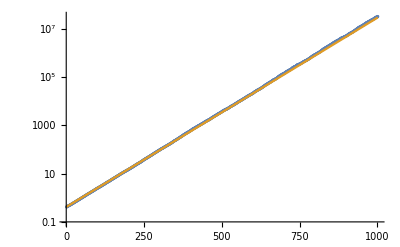

```mathematica
Show[ListLogPlot[Table[Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]],{τ,1,1001}]],LogPlot[fac Exp[-(-.045)τ .4],{τ,0,1001},PlotStyle->ColorData[97][2]]]
```

```mathematica
mat=Table[{{Mean[WA[[τ]]],Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]]},{Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]],Mean[WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
mat=Table[{{Mean[WA[[τ]]],Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]]},{Mean[WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]],Mean[WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
matHam=Table[{{Mean[WA[[τ]]HamA[[τ]]]/Mean[WA[[τ]]],Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]]},{Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]],Mean[WB[[τ]]HamB[[τ]]]/Mean[WB[[τ]]]}},{τ,1,1001}];
```

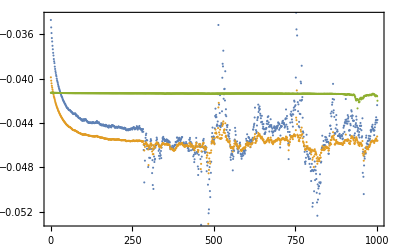

```mathematica
ListPlot[{matHam[[All,1,1]],matHam[[All,1,2]],matHam[[All,2,2]]},Frame->True]
```

```mathematica
NMeas=Length[WA[[1]]]
```

10000

```mathematica
NBoot=200;
```

```mathematica
bootIndices=RandomInteger[{1,NMeas},{NBoot,NMeas}];
```

```mathematica
Dimensions[bootIndices]
```

{200,10000}

```mathematica
bootmat=ParallelTable[Print[b];Table[{{Mean[WA[[τ,bootIndices[[b]]]]],
Mean[WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]]},{Mean[WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]],
Mean[WB[[τ,bootIndices[[b]]]]]}},{τ,1,1001}],{b,1,NBoot}];
```

1

10

19

28

37

46

2

47

11

20

38

29

3

48

12

21

30

39

4

49

22

40

31

13

5

50

23

32

41

14

24

33

51

42

6

15

25

34

52

7

43

16

26

35

53

44

8

17

27

36

54

45

9

18

55

64

73

81

89

97

82

65

74

56

90

98

66

83

75

57

91

99

84

67

76

58

92

100

85

68

59

93

77

101

69

86

60

94

78

102

87

70

61

95

79

103

88

71

96

62

80

104

105

72

113

63

121

129

106

137

114

145

122

130

107

115

138

146

123

131

108

139

116

147

124

132

140

109

148

117

125

133

141

110

118

149

126

134

142

111

150

119

127

135

143

120

112

151

128

136

153

144

161

152

169

177

154

185

162

193

170

178

186

163

155

194

171

179

187

164

156

195

172

180

188

165

157

196

173

181

189

166

158

197

174

182

190

167

198

159

175

183

191

168

199

160

176

184

200

192

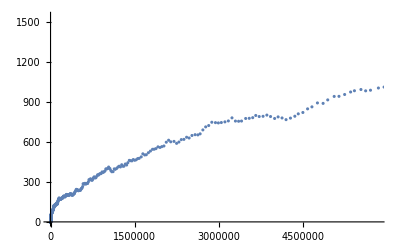

```mathematica
ListPlot[bootmat[[1,All,1]]]
```

```mathematica
t0=100;tref=220;
```

```mathematica
Timing[{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]]
```

{0.010264,{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}}

```mathematica
{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]
```

{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}

```mathematica
{evals,evecs}=Eigensystem[{mat[[tref]],mat[[t0]]}]
```

{{8.94502,6.95328},{{-0.848818,0.528685},{-0.443305,-0.896371}}}

```mathematica
t0s=Table[Table[t0,{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
tRs=Table[Table[tref,{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
eigenSys=Table[Table[Eigensystem[{mat[[tref]],mat[[t0]]}],{tref,t0+50,1000,50}],{t0,100,950,50}];
```

```mathematica
booteigenSys=ParallelTable[Table[Table[Eigensystem[{bootmat[[b,tref]],bootmat[[b,t0]]}],{tref,t0+50,1000,50}],{t0,100,950,50}],{b,1,NBoot}];
```

```mathematica
eigenVecs=eigenSys[[All,All,2]];
```

```mathematica
eigenVals=eigenSys[[All,All,1]];
```

```mathematica
booteigenVecs=booteigenSys[[All,All,All,2]];
```

```mathematica
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
```

```mathematica
CI[boots_]:=Block[{LQ,UQ,upper,lower},
UQ=(1+Erf[1/Sqrt[2.]])/2;
LQ=(1-Erf[1/Sqrt[2.]])/2;
upper=Quantile[boots,UQ];
lower=Quantile[boots,LQ];
(upper-lower)/2];
```

```mathematica
CI[-booteigenVecs[[All,5,3,1,2]]]
```

0.0367468

```mathematica
eigenVecs[[1,1,1,1]]
```

-0.81421

```mathematica
CI[booteigenVecs[[1,-2,-2,1]]]
```

0.50152

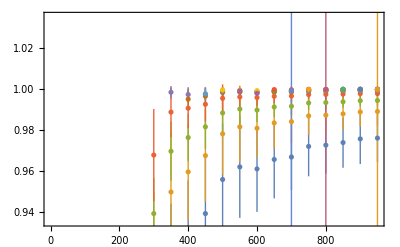

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,1]],CI[-Re[booteigenVecs[[All,t0,tR,1,1]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

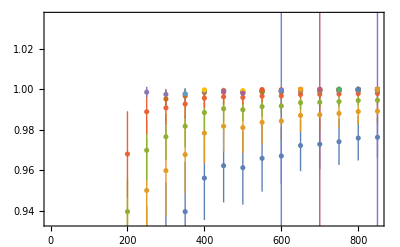
```mathematica
Show[-Graphics-,PlotRange->{0,1.1}]
```

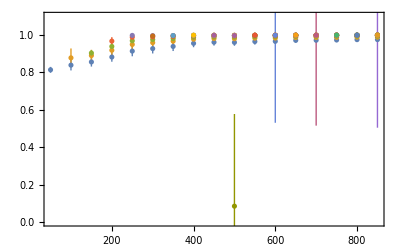

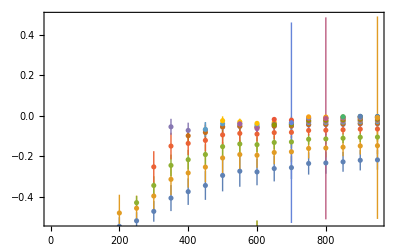

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,2]],CI[-Re[booteigenVecs[[All,t0,tR,1,2]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

```mathematica
t0I=4;tRI=3;
```

```mathematica
t0s[[t0I,tRI]]
```

250

```mathematica
tRs[[t0I,tRI]]
```

400

```mathematica
c11=Around[-eigenVecs[[t0I,tRI,1,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,1]]]]]
```

0.9910.010

```mathematica
c12=Around[-eigenVecs[[t0I,tRI,1,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,2]]]]]
```

-0.140.06

```mathematica
Around[-eigenVecs[[t0I,tRI,1,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,1]]]]]^2+Around[-eigenVecs[[t0I,tRI,1,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,2]]]]]^2
```

1.0000.025

```mathematica
{Around[-eigenVecs[[t0I,tRI,1,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,1]]]]]^2,Around[-eigenVecs[[t0I,tRI,1,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,1,2]]]]]^2}
```

{0.9820.019,0.0180.016}

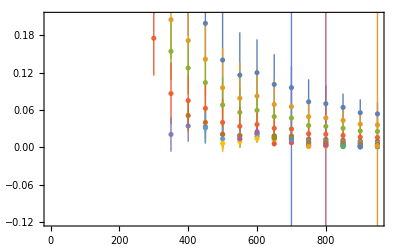

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,2,1]],CI[-Re[booteigenVecs[[All,t0,tR,2,1]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

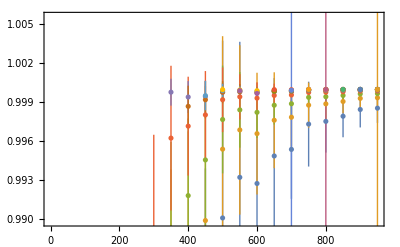

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,2,2]],CI[-Re[booteigenVecs[[All,t0,tR,2,2]]]]]},{tR,1,Length[eigenVecs[[t0]]]-1}],{t0,Length[eigenVecs]-1}],Joined->False,Frame->True]
```

```mathematica
c21=Around[-eigenVecs[[t0I,tRI,2,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,1]]]]]
```

0.080.04

```mathematica
c22=Around[-eigenVecs[[t0I,tRI,2,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,2]]]]]
```

0.9970.004

```mathematica
{Around[-eigenVecs[[t0I,tRI,2,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,1]]]]]^2,Around[-eigenVecs[[t0I,tRI,2,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,2]]]]]^2}
```

{0.0060.006,0.9940.008}

```mathematica
Around[-eigenVecs[[t0I,tRI,2,1]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,1]]]]]^2+Around[-eigenVecs[[t0I,tRI,2,2]],CI[-Re[booteigenVecs[[All,t0I,tRI,2,2]]]]]^2
```

1.0000.010

```mathematica
matHam3pt=Table[{{Mean[HamA[[τ]]WA[[τ]]],Mean[HamI1[[τ]]WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]]},{Mean[HamI1[[τ]]WI1[[τ]]]/Sqrt[Mean[WI4[[1]]]],Mean[HamB[[τ]]WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
matHam3pt=Table[{{Mean[HamA[[τ]]WA[[τ]]],Mean[HamI1[[τ]]WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]]},{Mean[HamI1[[τ]]WI1[[τ]]]/Sqrt[Mean[WI4[[τ]]]],Mean[HamB[[τ]]WB[[τ]]]}},{τ,1,1001}];
```

```mathematica
bootmatHam3pt=ParallelTable[Print[b];Table[{{Mean[HamA[[τ,bootIndices[[b]]]]WA[[τ,bootIndices[[b]]]]],Mean[HamI1[[τ,bootIndices[[b]]]]WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]]},{Mean[HamI1[[τ,bootIndices[[b]]]]WI1[[τ,bootIndices[[b]]]]]/Sqrt[Mean[WI4[[τ,bootIndices[[b]]]]]],Mean[HamB[[τ,bootIndices[[b]]]]WB[[τ,bootIndices[[b]]]]]}},{τ,1,1001}],{b,1,NBoot}];
```

1

10

19

28

37

46

2

38

20

29

11

47

3

21

39

12

30

48

4

22

40

13

31

49

5

50

14

41

32

23

6

15

51

42

33

7

24

16

43

52

8

34

25

35

26

17

53

9

44

36

27

18

55

54

45

64

73

56

81

89

97

65

57

82

74

90

98

66

67

75

91

99

58

83

59

84

100

76

92

68

85

77

101

60

93

69

86

78

102

61

94

70

62

79

103

71

95

87

88

63

80

104

72

96

105

113

121

129

137

145

106

114

138

130

122

146

107

139

115

123

131

147

108

140

116

132

148

124

109

117

125

141

133

149

110

142

126

118

150

134

111

143

119

151

135

127

112

144

120

136

128

152

153

161

169

177

185

193

154

162

170

163

178

186

194

155

171

164

179

172

187

195

156

165

180

188

173

196

157

166

181

189

174

197

158

167

198

190

175

182

168

159

191

176

199

183

160

200

184

192

```mathematica
cMat={{c11[[1]],c12[[1]]},{c21[[1]],c22[[1]]}}
```

{{0.990784,-0.135449},{0.075118,0.997175}}

```mathematica
Chop[Table[Table[Conjugate[eigenVecs[[t0I,tRI]]][[m]].mat[[t0s[[t0I,1]]]].eigenVecs[[t0I,tRI]][[n]],{m,1,2}],{n,1,2}]]
```

{{73.244,0},{0,61.8594}}

```mathematica
t0s
```

{{100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100,100},{150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150,150},{200,200,200,200,200,200,200,200,200,200,200,200,200,200,200,200},{250,250,250,250,250,250,250,250,250,250,250,250,250,250,250},{300,300,300,300,300,300,300,300,300,300,300,300,300,300},{350,350,350,350,350,350,350,350,350,350,350,350,350},{400,400,400,400,400,400,400,400,400,400,400,400},{450,450,450,450,450,450,450,450,450,450,450},{500,500,500,500,500,500,500,500,500,500},{550,550,550,550,550,550,550,550,550},{600,600,600,600,600,600,600,600},{650,650,650,650,650,650,650},{700,700,700,700,700,700},{750,750,750,750,750},{800,800,800,800},{850,850,850},{900,900},{950}}

```mathematica
Chop@Table[eigenVecs[[t0I,tRI]].mat[[t0s[[t0I,1]]]].Transpose[eigenVecs[[t0I,tRI]]],{τ,1,1}]
```

{{{73.244,0},{0,61.8594}}}

```mathematica
Chop@Table[cMat.mat[[t0s[[t0I,1]]]].Transpose[cMat],{τ,1,1}]
```

{{{73.244,0},{0,61.8594}}}

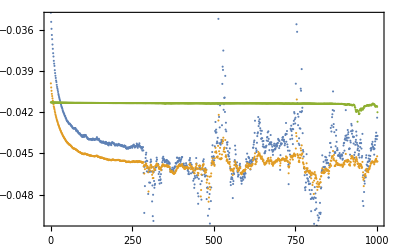

```mathematica
ListPlot[{matHam3pt[[All,1,1]]/mat[[All,1,1]],matHam3pt[[All,1,2]]/mat[[All,1,2]],matHam3pt[[All,2,2]]/mat[[All,2,2]]},Frame->True,PlotRange->{-.05,-.035}]
```

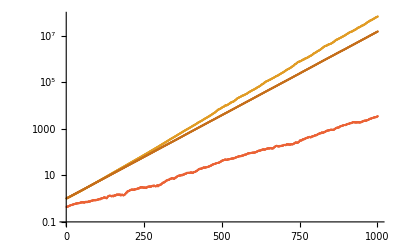

```mathematica
ListLogPlot[{matHam3pt[[All,1,1]],mat[[All,1,1]],matHam3pt[[All,1,2]],mat[[All,1,2]],matHam3pt[[All,2,2]],mat[[All,2,2]]}]
```

```mathematica
eigen3pt=Table[Table[(cMat.matHam3pt[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}];
```

```mathematica
eigen2pt=Table[Table[(cMat.mat[[τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}];
```

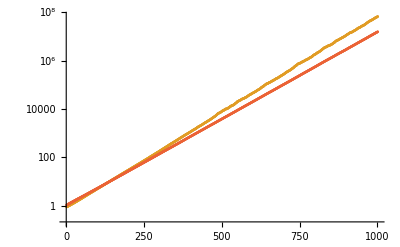

```mathematica
ListLogPlot[{eigen3pt[[1]],eigen2pt[[1]],eigen3pt[[2]],eigen2pt[[2]]}]
```

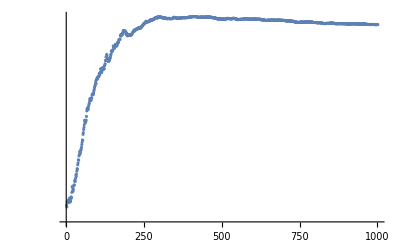

```mathematica
ListLogPlot[{eigen2pt[[1]]/mat[[All,1,1]]}]
```

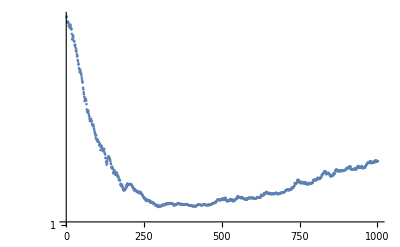

```mathematica
ListLogPlot[{eigen2pt[[2]]/mat[[All,2,2]]}]
```

```mathematica
fullEignvals=Table[Eigenvalues[{mat[[tref]],mat[[t0I]]}],{tref,Length[mat]}];
```

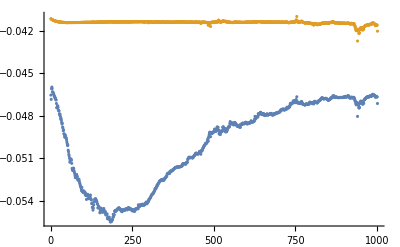

```mathematica
ListPlot[{eigen3pt[[2]]/fullEignvals[[All,2]],eigen3pt[[2]]/eigen2pt[[2]]}]
```

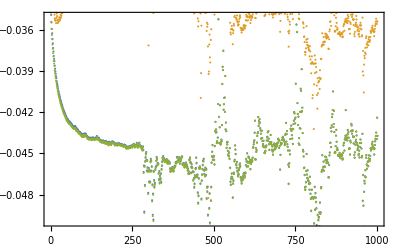

```mathematica
ListPlot[{eigen3pt[[1]]/eigen2pt[[1]],eigen3pt[[1]]/fullEignvals[[All,1]],matHam3pt[[All,1,1]]/mat[[All,1,1]]},Frame->True,PlotRange->{-.05,-.035}]
```

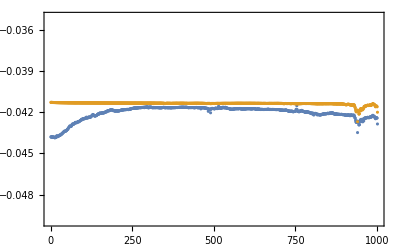

```mathematica
ListPlot[{eigen3pt[[2]]/(mat[[All,2,2]]),matHam3pt[[All,2,2]]/(mat[[All,2,2]])},Frame->True,PlotRange->{-.05,-.035}]
```

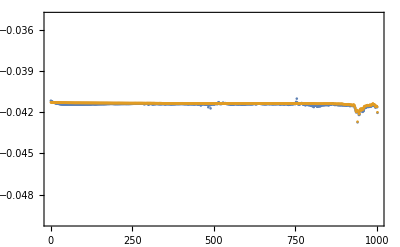

```mathematica
ListPlot[{eigen3pt[[2]]/eigen2pt[[2]],matHam3pt[[All,2,2]]/(mat[[All,2,2]])},Frame->True,PlotRange->{-.05,-.035}]
```

```mathematica
thresh=-(0.21485 4/3)^2/2
```

-0.0410316

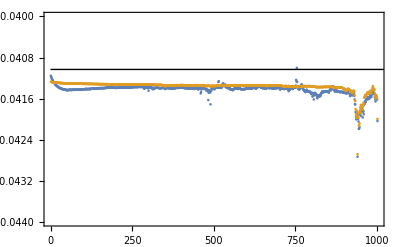

```mathematica
Show[ListPlot[{eigen3pt[[2]]/eigen2pt[[2]],matHam3pt[[All,2,2]]/(mat[[All,2,2]])},Frame->True,PlotRange->{-.044,-.04}],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}]]
```

```mathematica
eigenHam=Table[eigen3pt[[n]]/eigen2pt[[n]],{n,2}];
```

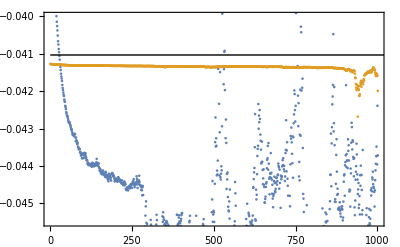

```mathematica
Show[ListPlot[{matHam[[All,1,1]],matHam[[All,2,2]]},Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000},{-.0455,-.04}}]
```

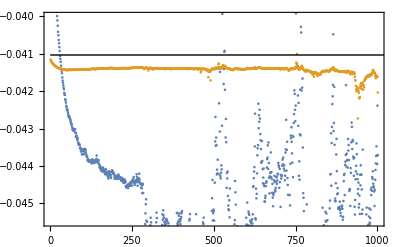

```mathematica
Show[ListPlot[{eigenHam[[1]],eigenHam[[2]]},Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000},{-.0455,-.04}}]
```

```mathematica
stop={500,1001};
```

```mathematica
matHamEM=Table[Table[{(τ-1).4,Around[matHam3pt[[τ,n,n]]/mat[[τ,n,n]],CI[bootmatHam3pt[[All,τ,n,n]]/bootmat[[All,τ,n,n]]]]},{τ,stop[[n]]}],{n,2}];
```

```mathematica
boott0I=RandomInteger[{1,10},NBoot]
```

{6,2,1,8,2,6,4,2,9,2,5,6,3,3,6,2,7,5,10,2,10,6,4,3,9,4,10,6,9,7,3,10,5,10,8,7,1,2,4,4,9,6,1,7,10,4,1,7,9,2,9,1,5,2,4,3,2,5,10,8,9,7,4,8,10,4,2,8,2,5,2,6,5,2,3,10,7,9,9,9,5,7,7,5,3,5,3,1,10,10,4,7,4,4,6,5,3,2,2,1,6,9,6,5,4,3,8,2,4,5,8,5,7,5,2,10,10,3,6,9,9,7,7,6,8,4,6,10,4,4,9,6,8,3,5,1,3,8,4,10,3,5,7,5,2,3,9,6,2,8,1,8,6,2,6,5,1,3,9,10,7,2,2,5,7,9,5,2,5,7,10,3,2,1,8,9,1,5,3,3,10,8,3,4,4,8,3,3,7,5,3,1,5,8,7,7,3,7,10,1}

```mathematica
boottRI=Table[RandomInteger[{1,Length[booteigenVecs[[1,boott0I[[b]]]]]}],{b,NBoot}]
```

{1,16,7,1,1,11,6,15,5,7,13,13,15,6,11,12,8,1,3,7,5,2,11,9,10,9,9,7,2,4,5,4,12,4,1,4,4,5,4,14,2,13,8,10,1,11,4,3,6,5,10,12,14,6,2,4,5,4,2,9,8,11,2,9,2,12,6,3,10,6,12,7,10,6,12,3,11,2,2,2,6,7,5,13,10,1,16,2,3,7,14,7,9,4,9,6,13,3,16,8,12,6,3,11,12,2,11,15,10,13,9,9,9,9,11,2,3,15,12,5,10,6,11,6,4,8,5,8,12,14,6,9,7,8,13,8,6,10,13,9,6,13,8,7,2,14,9,1,12,10,17,3,13,1,1,13,4,5,2,7,5,7,14,8,1,5,3,17,14,1,9,10,5,3,11,8,15,2,10,14,4,9,16,10,5,11,14,12,4,4,2,16,14,8,5,2,12,2,2,1}

```mathematica
-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,1]],{b,2}]]
```

{0.992093,0.995004}

```mathematica
Dimensions[booteigenVecs]
```

{200,18}

```mathematica
Dimensions[booteigenVecs[[All,3]]]
```

{200,16,2,2}

```mathematica
bootc11=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,1]],{b,NBoot}]];
```

```mathematica
bootc12=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],1,2]],{b,NBoot}]];
```

```mathematica
bootc21=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],2,1]],{b,NBoot}]];
```

```mathematica
bootc22=-Re[Table[booteigenVecs[[b,boott0I[[b]],boottRI[[b]],2,2]],{b,NBoot}]];
```

```mathematica
bootcMat=Table[{{bootc11[[b]],bootc12[[b]]},{bootc21[[b]],bootc22[[b]]}},{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(cMat.bootmatHam3pt[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(cMat.bootmat[[b,τ]].Transpose[cMat])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen3pt=Table[Table[Table[(bootcMat[[b]].bootmatHam3pt[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigen2pt=Table[Table[Table[(bootcMat[[b]].bootmat[[b,τ]].Transpose[bootcMat[[b]]])[[n,n]],{τ,1,Length[mat]}],{n,2}],{b,NBoot}];
```

```mathematica
booteigenHam=Table[Table[booteigen3pt[[b,n]]/booteigen2pt[[b,n]],{n,2}],{b,NBoot}];
```

```mathematica
eigenHamEM=Table[Table[{(τ-1).4,Around[eigenHam[[n,τ]],CI[booteigenHam[[All,n,τ]]]]},{τ,stop[[n]]}],{n,2}];
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
<<MaTeX`
```

```mathematica
TrimBleed[p2_]:=Show[p2,With[{d=.2},Graphics[{White,FilledCurve[{{Line[ImageScaled/@{{-d,-d},{-d,1+d},{1+d,1+d},{1+d,-d}}]},{Line[Scaled/@{{0,0},{0,1},{1,1},{1,0}}]}}]}]],ImagePadding->{{70,10},{45,10}}]
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
origlegend=PointLegend[Table[Directive[ColorData[97][ii]],{ii,2}],{MaTeX["b/a=5",Magnification->0.8],MaTeX["b/a=100",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,2}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
EMPorig=TrimBleed[Show[ListPlot[matHamEM,Joined->False,Frame->True,PlotLegends->Placed[origlegend,{.75,.2}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\left<\\Psi_T|H(\\tau)|\\Psi_T \\right> / m_Q",Magnification->1.2]}]]
```

-Graphics-

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/EMorig.pdf",EMPorig]
```

~/Dropbox//physics/projects/heavy_quark_nuclei/EMorig.pdf

```mathematica
GEVPlegend=PointLegend[Table[Directive[ColorData[97][ii]],{ii,2}],{MaTeX["n=0",Magnification->0.8],MaTeX["n=1",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,2}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

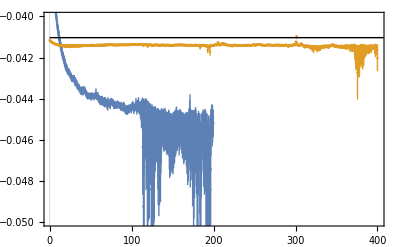

```mathematica
EMPGEVP=Show[ListPlot[eigenHamEM,Joined->False,Frame->True,PlotLegends->Placed[GEVPlegend,{.75,.2}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\left<n|H(\\tau)|n \\right> / m_Q",Magnification->1.2]}]
```

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/EMGEVP.pdf",EMPGEVP]
```

~/Dropbox//physics/projects/heavy_quark_nuclei/EMGEVP.pdf

```mathematica
GEVPlegend=PointLegend[Table[Directive[ColorData[97][ii+2]],{ii,2}],{MaTeX["n=0",Magnification->0.8],MaTeX["n=1",Magnification->0.8]},LegendMarkers->Table[Automatic,{ii,2}],LegendLayout->{"Column",4},LegendMargins->0.5,LegendFunction->frame]
```

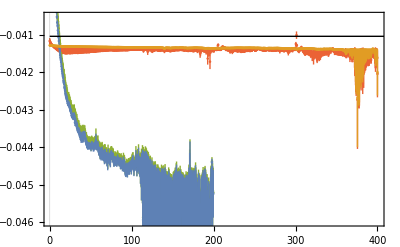

```mathematica
EMboth=Show[ListPlot[eigenHamEM,Joined->False,Frame->True,PlotLegends->Placed[GEVPlegend,{.725,.2}],PlotStyle->{ColorData[97][3],ColorData[97][4]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][4]}],ListPlot[matHamEM,Joined->False,Frame->True,PlotLegends->Placed[origlegend,{.77,.3}]],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.049,-.0405}},BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],Frame->True,Axes->False,GridLines->{{0},{0}},FrameLabel->{MaTeX["\\tau \\ m_Q",Magnification->1.2],MaTeX["\\Delta E_n(\\tau) / m_Q",Magnification->1.2]}]
```

```mathematica
Export[dropboxDir<>"/physics/projects/heavy_quark_nuclei/EMboth.pdf",EMboth]
```

~/Dropbox//physics/projects/heavy_quark_nuclei/EMboth.pdf

```mathematica
eigenHamEM[[1,250]]
```

{99.6,-0.044530.00019}

```mathematica
eigenHamEM[[2,250]]
```

{99.6,-0.041380.00005}

```mathematica
eigenHamEM[[1,250,2]]-thresh
```

-0.003500.00019

```mathematica
eigenHamEM[[2,250,2]]-thresh
```

-0.000350.00005

```mathematica
mb=4.77050;
```

```mathematica
Mean[(eigenHamEM[[1,200;;350,2]]-thresh)]mb 1000
```

-20.40.6

```mathematica
.214850^2(4/3)^2/4/4
```

0.00512895

```mathematica
(eigenHamEM[[2,250;;,2]]-thresh)mb 1000
```

{-1.650.24,-1.650.23,-1.650.23,-1.640.22,-1.640.22,-1.630.22,-1.640.23,-1.630.24,-1.630.24,-1.630.23,-1.630.23,-1.630.22,-1.630.22,-1.640.22,-1.630.21,-1.630.21,-1.630.22,-1.630.22,-1.620.22,-1.630.22,-1.630.22,-1.610.22,-1.610.21,-1.620.21,-1.630.23,-1.620.22,-1.620.21,-1.620.21,-1.620.22,-1.620.21,-1.620.21,-1.630.21,-1.620.20,-1.620.21,-1.630.21,-1.690.23,-1.670.22,-1.800.31,-1.660.22,-1.720.26,-1.660.21,-1.660.21,-1.650.21,-1.640.20,-1.640.21,-1.670.22,-1.640.21,-1.660.22,-1.680.23,-1.740.26,-2.00.5,-1.670.21,-1.700.22,-1.670.21,-1.680.22,-1.710.23,-1.650.21,-1.640.20,-1.660.20,-1.690.22,-1.680.21,-1.780.27,-1.740.24,-1.820.31,-1.760.25,-1.840.32,-1.690.21,-1.720.24,-1.740.24,-1.740.24,-1.750.23,-1.710.21,-1.710.21,-1.700.22,-1.680.22,-1.670.22,-1.680.23,-1.700.23,-1.700.23,-1.690.23,-1.700.22,-1.730.23,-1.740.24,-1.720.22,-1.750.24,-1.730.23,-1.740.24,-1.740.24,-1.730.23,-1.760.25,-1.720.23,-1.710.23,-1.710.22,-1.700.22,-1.710.21,-1.690.22,-1.690.23,-1.730.23,-1.710.22,-1.770.23,-1.740.23,-1.830.28,-1.760.23,-1.770.23,-1.740.22,-1.720.22,-1.720.22,-1.730.23,-1.710.22,-1.740.22,-1.730.22,-1.720.22,-1.740.22,-1.750.22,-1.730.21,-1.720.22,-1.750.23,-1.780.24,-1.790.24,-1.780.24,-1.780.24,-1.790.25,-1.770.25,-1.750.24,-1.750.24,-1.760.24,-1.760.24,-1.760.24,-1.750.22,-1.740.23,-1.740.23,-1.740.22,-1.750.22,-1.720.23,-1.710.23,-1.720.22,-1.710.23,-1.690.21,-1.700.21,-1.720.23,-1.720.23,-1.710.22,-1.710.23,-1.710.23,-1.700.22,-1.710.23,-1.700.23,-1.690.22,-1.690.22,-1.690.21,-1.690.22,-1.690.22,-1.680.22,-1.680.22,-1.700.23,-1.700.23,-1.700.23,-1.710.22,-1.700.22,-1.710.23,-1.730.23,-1.740.22,-1.730.22,-1.740.23,-1.720.22,-1.720.22,-1.730.22,-1.710.22,-1.740.22,-1.760.21,-1.770.22,-1.770.23,-1.780.24,-1.780.23,-1.790.24,-1.720.21,-1.730.21,-1.720.21,-1.730.22,-1.740.22,-1.770.24,-1.750.23,-1.730.23,-1.750.23,-1.740.23,-1.760.23,-1.760.23,-1.790.24,-1.750.23,-1.770.24,-1.810.25,-1.800.25,-1.760.23,-1.770.24,-1.730.23,-1.730.23,-1.700.20,-1.710.21,-1.750.24,-1.760.25,-1.760.24,-1.820.27,-1.860.30,-1.830.28,-1.770.25,-1.740.22,-1.740.23,-1.740.22,-1.740.23,-1.800.25,-2.20.6,-2.10.5,-1.860.30,-1.800.24,-1.780.25,-1.760.24,-1.750.22,-1.740.22,-1.740.22,-1.740.22,-1.790.24,-1.820.24,-1.790.24,-1.820.25,-1.800.23,-1.840.25,-1.840.26,-1.810.24,-1.980.33,-1.890.30,-1.900.30,-1.880.29,-2.00.4,-2.81.3,-2.20.5,-2.10.5,-2.00.4,-1.940.32,-2.10.4,-2.10.5,-3.21.7,-1.980.34,-1.970.31,-1.800.24,-1.770.23,-1.750.21,-1.740.20,-1.810.24,-1.790.22,-1.780.23,-1.780.23,-1.810.24,-1.850.26,-1.750.21,-1.660.19,-1.630.20,-1.680.19,-1.660.21,-1.660.19,-1.710.21,-1.700.20,-1.700.21,-1.680.20,-1.540.23,-1.20.6,-1.10.7,-1.590.21,-1.710.21,-1.630.20,-1.550.24,-1.700.20,-1.710.20,-1.690.20,-1.680.20,-1.690.21,-1.610.20,-1.440.29,-1.40.4,-1.40.4,-1.30.4,-1.540.22,-1.520.24,-1.490.25,-1.490.26,-1.550.21,-1.400.32,-1.620.19,-1.590.20,-1.630.19,-1.700.21,-1.680.21,-1.690.22,-1.680.21,-1.720.22,-1.740.21,-1.740.22,-1.750.22,-1.740.21,-1.760.23,-1.720.21,-1.820.27,-1.890.31,-1.890.33,-1.850.31,-1.850.30,-1.830.28,-1.850.31,-1.850.31,-1.90.4,-1.880.32,-1.860.32,-1.820.28,-1.830.28,-1.770.25,-1.760.25,-1.690.22,-1.700.22,-1.720.24,-1.770.26,-1.770.26,-1.780.26,-1.750.25,-1.780.27,-1.790.27,-1.810.28,-1.800.28,-1.800.28,-1.780.27,-1.770.26,-1.760.25,-1.750.25,-1.770.26,-1.820.29,-1.830.29,-1.840.30,-1.850.31,-1.840.30,-1.840.29,-1.830.29,-1.830.29,-1.840.30,-1.820.28,-1.810.27,-1.820.28,-1.830.28,-1.840.29,-1.810.27,-1.810.28,-1.780.27,-1.740.25,-1.760.25,-1.780.26,-1.720.23,-1.760.25,-1.760.26,-1.780.26,-1.730.23,-1.730.23,-1.740.24,-1.750.25,-1.760.26,-1.740.25,-1.790.27,-1.750.25,-1.770.26,-1.760.25,-1.760.25,-1.750.25,-1.760.25,-1.750.24,-1.700.21,-1.700.21,-1.680.21,-1.670.21,-1.660.22,-1.630.23,-1.580.25,-1.770.26,-1.770.26,-1.720.23,-1.750.24,-1.740.23,-1.690.22,-1.650.22,-1.640.21,-1.640.20,-1.570.25,-1.610.22,-1.580.24,-1.600.23,-1.590.24,-1.600.23,-1.630.22,-1.650.22,-1.670.24,-1.700.23,-1.690.22,-1.650.25,-1.700.24,-1.720.24,-1.750.25,-1.730.25,-1.700.24,-1.740.27,-1.730.26,-1.770.26,-1.760.26,-1.760.27,-1.750.26,-1.740.26,-1.770.28,-1.750.26,-1.730.26,-1.710.25,-1.700.25,-1.670.25,-1.720.25,-1.670.26,-1.690.23,-1.720.24,-1.750.26,-1.720.24,-1.710.24,-1.720.24,-1.680.22,-1.730.24,-1.710.23,-1.720.24,-1.760.26,-1.740.24,-1.760.26,-1.780.27,-1.760.25,-1.750.25,-1.730.23,-1.720.24,-1.730.24,-1.750.25,-1.750.26,-1.750.26,-1.730.25,-1.720.25,-1.720.25,-1.740.25,-1.720.24,-1.710.24,-1.710.24,-1.690.22,-1.700.22,-1.700.24,-1.750.27,-1.720.25,-1.740.26,-1.90.4,-1.800.32,-1.740.28,-1.750.26,-1.740.26,-1.750.25,-1.730.25,-1.730.24,-1.750.24,-1.760.24,-1.780.26,-1.800.25,-1.780.26,-1.830.29,-1.790.27,-1.770.26,-1.720.27,-1.710.28,-1.660.31,-1.770.25,-1.740.27,-1.740.27,-1.800.28,-1.810.28,-1.840.30,-1.910.33,-2.00.4,-1.90.4,-1.910.35,-1.850.34,-1.880.31,-1.800.31,-1.740.29,-1.790.33,-1.740.33,-1.750.29,-1.760.27,-1.770.29,-1.710.29,-1.820.33,-1.730.34,-1.690.34,-1.690.32,-1.60.4,-1.70.4,-1.70.4,-1.710.32,-1.70.4,-1.50.5,-1.01.0,-1.10.9,0.12.2,-1.20.8,-1.60.4,-1.70.4,-1.80.4,-1.680.35,-1.860.32,-1.820.29,-1.860.31,-1.760.30,-1.70.4,-1.750.30,-1.50.5,-1.50.5,-1.630.34,-1.40.6,-1.610.35,-1.580.35,-1.740.25,-1.840.30,-1.850.30,-1.880.30,-1.90.4,-1.90.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-1.880.31,-2.00.4,-2.00.4,-1.970.35,-2.00.4,-2.00.4,-2.00.4,-2.10.4,-2.10.4,-2.10.5,-2.00.4,-2.10.4,-2.20.5,-2.20.5,-2.30.6,-2.20.5,-2.20.5,-2.20.6,-2.50.8,-2.50.7,-2.20.5,-2.20.5,-2.81.0,-2.40.7,-2.20.5,-2.20.5,-2.30.6,-2.20.5,-2.30.5,-2.30.5,-2.30.6,-2.40.7,-2.60.7,-2.70.9,-2.40.6,-2.50.7,-2.40.6,-2.40.6,-2.50.6,-2.40.6,-2.50.7,-2.40.6,-2.40.6,-2.40.6,-2.30.5,-2.30.5,-2.20.4,-2.10.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.00.4,-2.10.4,-2.00.4,-2.00.4,-2.10.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.10.5,-2.10.5,-2.10.4,-2.00.4,-2.00.4,-1.90.4,-1.90.4,-1.80.4,-1.90.4,-1.80.4,-1.80.4,-1.70.4,-1.70.5,-1.70.5,-1.60.6,-1.80.4,-1.80.5,-1.70.5,-1.90.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-1.90.4,-1.90.4,-2.00.4,-2.00.4,-2.00.4,-2.00.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.10.4,-2.20.5,-2.10.4,-2.10.4,-2.10.4,-2.10.5,-2.20.5,-2.10.5,-2.10.5,-2.20.5,-2.00.7,-2.20.5,-2.20.5,-2.20.6,-2.20.5,-2.10.4,-2.00.5,-2.00.4,-2.00.5,-2.10.5,-2.20.5,-2.20.5,-2.30.5,-2.50.7,-2.30.6,-2.30.6,-2.20.7,-2.10.6,-2.20.7,-2.40.8,-2.40.8,-2.30.7,-2.30.7,-2.20.6,-2.30.7,-2.20.6,-2.50.7,-2.81.0,-3.21.4,-3.21.4,-3.92.1,-4.42.6,-4.62.8,-4.52.7,-4.12.2,-4.22.3,-8.6.,-4.32.4,-4.62.7,-4.82.9,-6.4.,-6.4.,-5.43.4,-4.22.3,-3.81.9,-4.02.2,-3.61.7,-4.32.4,-3.91.9,-3.71.7,-3.81.8,-3.51.7,-4.52.3,-4.01.9,-3.91.8,-4.22.1,-3.31.4,-3.21.3,-3.21.3,-2.91.1,-3.01.2,-3.01.1,-2.81.0,-2.81.0,-2.80.9,-2.80.9,-2.70.9,-2.60.8,-2.60.8,-2.80.9,-2.70.9,-2.60.9,-2.71.0,-2.60.8,-2.50.7,-2.40.7,-2.50.8,-2.60.8,-2.60.8,-2.40.7,-2.20.5,-2.20.5,-2.00.4,-1.90.5,-2.00.4,-2.20.4,-2.30.5,-2.20.5,-2.30.5,-2.60.8,-2.81.0,-3.01.1,-2.70.9,-2.60.9,-2.70.9,-2.81.0,-2.81.2,-4.82.9}

```mathematica
eigenHamEM[[2]]
```

{{0.,-0.034910.00033},{0.4,-0.035440.00030},{0.8,-0.035920.00031},{1.2,-0.036290.00028},{1.6,-0.036520.00027},{2.,-0.036830.00026},{2.4,-0.037070.00026},{2.8,-0.037370.00024},{3.2,-0.037550.00024},{3.6,-0.037800.00024},{4.,-0.037970.00025},{4.4,-0.038060.00022},{4.8,-0.038310.00020},{5.2,-0.038470.00019},{5.6,-0.038630.00019},{6.,-0.038760.00020},{6.4,-0.038900.00021},{6.8,-0.039020.00022},{7.2,-0.039230.00024},{7.6,-0.039340.00022},{8.,-0.039400.00019},{8.4,-0.039460.00016},{8.8,-0.039570.00016},{9.2,-0.039720.00016},{9.6,-0.039790.00015},{10.,-0.039880.00013},{10.4,-0.039950.00013},{10.8,-0.040030.00013},{11.2,-0.040090.00012},{11.6,-0.040210.00013},{12.,-0.040290.00013},{12.4,-0.040330.00013},{12.8,-0.040410.00012},{13.2,-0.040490.00013},{13.6,-0.040540.00013},{14.,-0.040580.00012},{14.4,-0.040690.00012},{14.8,-0.040760.00012},{15.2,-0.040820.00012},{15.6,-0.040860.00012},{16.,-0.040930.00013},{16.4,-0.040960.00013},{16.8,-0.041050.00013},{17.2,-0.041070.00013},{17.6,-0.041060.00013},{18.,-0.041160.00012},{18.4,-0.041190.00014},{18.8,-0.041230.00012},{19.2,-0.041310.00013},{19.6,-0.041350.00014},{20.,-0.041400.00014},{20.4,-0.041430.00014},{20.8,-0.041430.00013},{21.2,-0.041510.00012},{21.6,-0.041550.00013},{22.,-0.041610.00013},{22.4,-0.041630.00014},{22.8,-0.041640.00013},{23.2,-0.041670.00014},{23.6,-0.041690.00014},{24.,-0.041690.00014},{24.4,-0.041720.00013},{24.8,-0.041750.00014},{25.2,-0.041790.00014},{25.6,-0.041830.00014},{26.,-0.041850.00014},{26.4,-0.041910.00014},{26.8,-0.041960.00014},{27.2,-0.041960.00015},{27.6,-0.041960.00014},{28.,-0.041940.00015},{28.4,-0.042000.00014},{28.8,-0.042000.00014},{29.2,-0.041980.00014},{29.6,-0.041990.00014},{30.,-0.042000.00013},{30.4,-0.042070.00013},{30.8,-0.042140.00015},{31.2,-0.042070.00013},{31.6,-0.042110.00013},{32.,-0.042150.00013},{32.4,-0.042180.00013},{32.8,-0.042230.00013},{33.2,-0.042190.00014},{33.6,-0.042270.00015},{34.,-0.042280.00014},{34.4,-0.042320.00013},{34.8,-0.042320.00013},{35.2,-0.042330.00014},{35.6,-0.042340.00014},{36.,-0.042420.00014},{36.4,-0.042410.00013},{36.8,-0.042450.00013},{37.2,-0.042510.00014},{37.6,-0.042470.00014},{38.,-0.042480.00015},{38.4,-0.042580.00014},{38.8,-0.042570.00014},{39.2,-0.042510.00014},{39.6,-0.042510.00014},{40.,-0.042480.00014},{40.4,-0.042590.00016},{40.8,-0.042580.00015},{41.2,-0.042540.00014},{41.6,-0.042490.00013},{42.,-0.042530.00014},{42.4,-0.042520.00013},{42.8,-0.042510.00013},{43.2,-0.042580.00014},{43.6,-0.042640.00014},{44.,-0.042660.00015},{44.4,-0.042660.00015},{44.8,-0.042670.00016},{45.2,-0.042730.00016},{45.6,-0.042720.00015},{46.,-0.042760.00014},{46.4,-0.042770.00016},{46.8,-0.042790.00015},{47.2,-0.042770.00015},{47.6,-0.042760.00015},{48.,-0.042750.00015},{48.4,-0.042770.00017},{48.8,-0.042800.00016},{49.2,-0.042790.00015},{49.6,-0.042790.00015},{50.,-0.042830.00015},{50.4,-0.042860.00017},{50.8,-0.042840.00015},{51.2,-0.042800.00015},{51.6,-0.042840.00015},{52.,-0.042810.00016},{52.4,-0.042850.00017},{52.8,-0.042820.00016},{53.2,-0.042850.00016},{53.6,-0.042820.00016},{54.,-0.042830.00018},{54.4,-0.042810.00016},{54.8,-0.042800.00016},{55.2,-0.042800.00017},{55.6,-0.042850.00016},{56.,-0.042790.00017},{56.4,-0.042730.00017},{56.8,-0.042820.00016},{57.2,-0.042860.00017},{57.6,-0.042890.00016},{58.,-0.042890.00017},{58.4,-0.042860.00016},{58.8,-0.042850.00016},{59.2,-0.042930.00016},{59.6,-0.042950.00016},{60.,-0.043010.00016},{60.4,-0.043020.00017},{60.8,-0.042980.00018},{61.2,-0.043020.00019},{61.6,-0.043060.00019},{62.,-0.043020.00019},{62.4,-0.043040.00018},{62.8,-0.043100.00019},{63.2,-0.043060.00018},{63.6,-0.043050.00018},{64.,-0.043020.00019},{64.4,-0.043080.00019},{64.8,-0.043100.00019},{65.2,-0.043080.00019},{65.6,-0.043120.00018},{66.,-0.043130.00019},{66.4,-0.043090.00018},{66.8,-0.043170.00021},{67.2,-0.043080.00019},{67.6,-0.043090.00019},{68.,-0.043170.00020},{68.4,-0.043150.00021},{68.8,-0.043190.00020},{69.2,-0.043170.00020},{69.6,-0.043180.00020},{70.,-0.043260.00021},{70.4,-0.043250.00020},{70.8,-0.043290.00023},{71.2,-0.043150.00019},{71.6,-0.043210.00020},{72.,-0.043210.00020},{72.4,-0.043190.00019},{72.8,-0.043240.00020},{73.2,-0.043270.00020},{73.6,-0.043250.00019},{74.,-0.043300.00021},{74.4,-0.043190.00019},{74.8,-0.043170.00019},{75.2,-0.043160.00017},{75.6,-0.043160.00018},{76.,-0.043180.00018},{76.4,-0.043210.00019},{76.8,-0.043190.00019},{77.2,-0.043220.00019},{77.6,-0.043220.00020},{78.,-0.043250.00020},{78.4,-0.043300.00020},{78.8,-0.043300.00021},{79.2,-0.043300.00021},{79.6,-0.043260.00021},{80.,-0.043300.00021}}

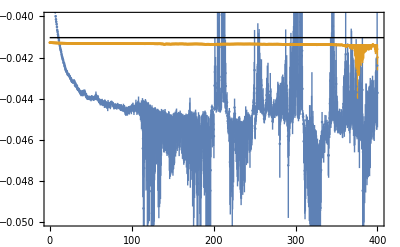

```mathematica
Show[ListPlot[matHamEM,Joined->False,Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}}]
```

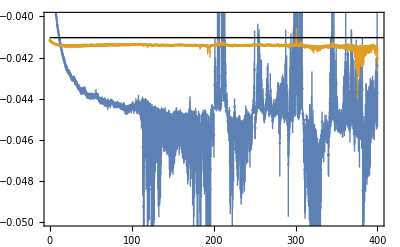

```mathematica
Show[ListPlot[eigenHamEM,Joined->False,Frame->True],Graphics[{Black,Line[{{0,thresh},{10000,thresh}}]}],PlotRange->{{1,1000 .4},{-.05,-.04}}]
```

```mathematica
matHam[[1]]
```

{{-0.0347258,-0.0398865},{-0.0398865,-0.041273}}

```mathematica
matmatHam[[1000]]
```

{{-2.86816×10^6,-1.3933×10^6},{-1.3933×10^6,-637145.}}

```mathematica
Table[cMat.mat[[τ]].matHam[[τ]].Transpose[mat[[τ]]].Transpose[cMat],{τ,1,1}]
```

{{{-0.0301529,-0.0328281},{-0.0328281,-0.0334712}}}

```mathematica
Table[Transpose[cMat].Transpose[mat[[τ]]].matHam[[τ]].cMat.mat[[τ]],{τ,1,1}]
```

{{{-0.0294753,-0.0327108},{-0.0328664,-0.0341525}}}

```mathematica
Table[cMat.mat[[τ]].matHam[[τ]],{τ,1,1}]
```

{{{-0.0323821,-0.036749},{-0.0355931,-0.037185}}}

```mathematica
Table[Transpose[cMat].Transpose[mat[[τ]]].matHam[[τ]],{τ,1,1}]
```

{{{-0.0319791,-0.0363195},{-0.0359744,-0.0376087}}}

```mathematica
mat
```

```mathematica
matHam[[1]]
```

{{-0.0347258,-0.0398865},{-0.0398865,-0.041273}}

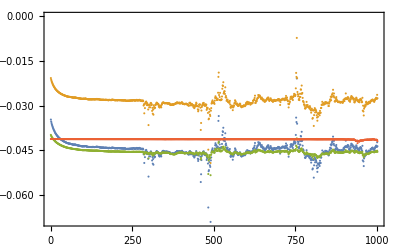

```mathematica
ListPlot[{ matHam[[All,1,1]],c11[[1]] matHam[[All,1,1]]+c12[[1]] matHam[[All,1,2]],matHam[[All,1,2]],matHam[[All,2,2]]},Frame->True]
```

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.430897,-0.296194,-0.536342,-0.531442,-0.52827,-0.492685,-0.491518,-0.528522,0.742784,-0.427323,-0.402003,«30»,-0.483738,-0.29733,-0.447551,-0.35939,-0.5671,-0.580002,-0.50034,-0.324017,-0.409612,«150»},«19»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.430897,-0.296194,-0.536342,-0.531442,-0.52827,-0.492685,-0.491518,-0.528522,0.742784,-0.427323,-0.402003,«30»,-0.483738,-0.29733,-0.447551,-0.35939,-0.5671,-0.580002,-0.50034,-0.324017,-0.409612,«150»},«20»].

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{-0.404763,-0.865885-0.0448084 ⅈ,-0.095352,-0.182075,0.0499562,0.0103266,-0.167085,-0.149282,-0.195281,-0.34269,«31»,-0.127576,0.0627556,-0.494826,-0.000875116,-0.253025,-0.181363,0.01528,0.225063,-0.25554,«150»},«19»].

General::stop: Further output of Quantile::rectn will be suppressed during this calculation.

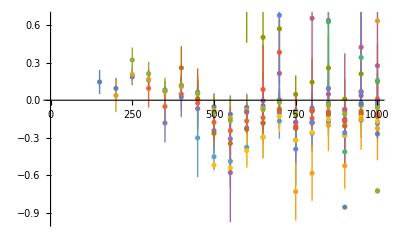

```mathematica
ListPlot[Table[Table[{tRs[[t0,tR]],Around[-eigenVecs[[t0,tR,1,2]],CI[-booteigenVecs[[All,t0,tR,1,2]]]]},{tR,1,Length[eigenVecs[[t0]]]}],{t0,Length[eigenVecs]}],Joined->False]
```

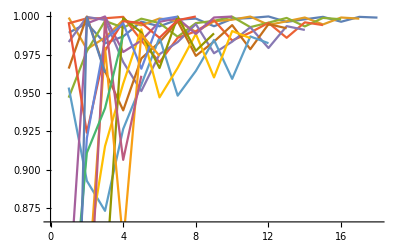

```mathematica
ListPlot[-eigenVecs[[All,All,1,1]],Joined->True]
```

```mathematica
-eigenVecs[[-1,-1,1]]
```

{0.690349,-0.723476}

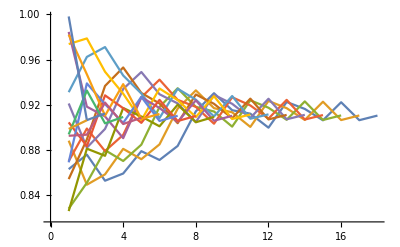

```mathematica
ListPlot[-eigenVecs[[All,All,2,2]],Joined->True]
```

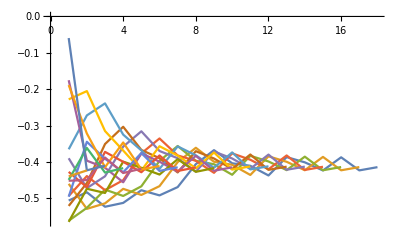

```mathematica
ListPlot[-eigenVecs[[All,All,2,1]],Joined->True]
```

```mathematica
-eigenVecs[[-1,-1,2]]
```

{-0.385309,0.922788}

```mathematica
Total[Total/@evals]
```

171

```mathematica
Dimensions[evals]
```

{19}

```mathematica
Table[
```

```mathematica
evecs
```

{{-0.740865,-0.671654},{0.701492,-0.712677}}

```mathematica
gevpCorrs=Table[Table[Table[Sum[Sum[Conjugate[evecs[[m,MM]]] mat[[t,MM,NN]]evecs[[n,NN]],{MM,1,2}],{NN,1,2}],{t,1,101}],{m,1,2}],{n,1,2}];
```

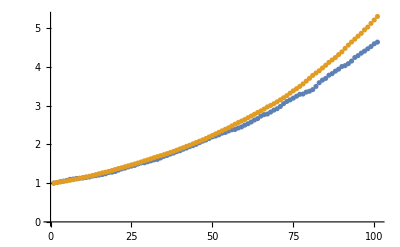

```mathematica
ListPlot[{gevpCorrs[[1,1]]/gevpCorrs[[1,1,1]],gevpCorrs[[2,2]]/gevpCorrs[[2,2,1]]}]
```

```mathematica
EM[tab_]:=Table[1/1Log[tab[[t]]/tab[[t+1]]],{t,Length[tab]-1}]
```

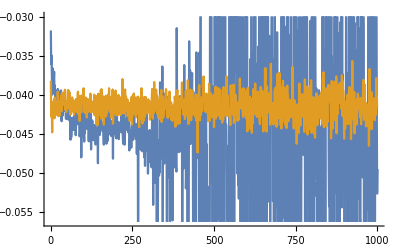

```mathematica
ListPlot[{EM[Table[Mean[WA[[τ]]],{τ,1,1001}]]/.4,EM[Table[Mean[WB[[τ]]],{τ,1,1001}]]/.4},Joined->True]
```

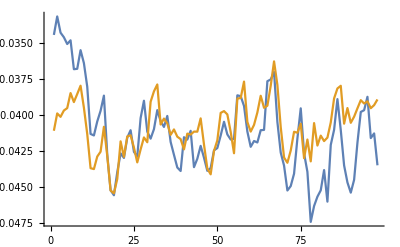

```mathematica
ListPlot[{EM[Table[Mean[WA[[τ]]],{τ,1,101}]]/.4,EM[Table[Mean[WB[[τ]]],{τ,1,101}]]/.4},Joined->True]
```

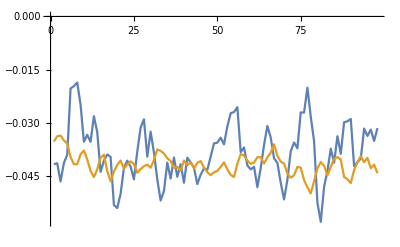

```mathematica
ListPlot[{EM[gevpCorrs[[1,1]]]/.4,EM[gevpCorrs[[2,2]]]/.4},Joined->True]
```

```mathematica
Around[Mean[EM[Table[Mean[WA[[τ]]],{τ,1,101}]]],StandardDeviation[EM[Table[Mean[WA[[τ]]],{τ,1,101}]]]]/.4
```

-0.04130.0029

```mathematica
Around[Mean[EM[Table[Mean[WB[[τ]]],{τ,1,101}]]],StandardDeviation[EM[Table[Mean[WB[[τ]]],{τ,1,101}]]]]/.4
```

-0.04080.0018

```mathematica
Around[Mean[EM[gevpCorrs[[1,1]]]],StandardDeviation[EM[gevpCorrs[[1,1]]]]]/.4
```

-0.04170.0028

```mathematica
Around[Mean[EM[gevpCorrs[[2,2]]]],StandardDeviation[EM[gevpCorrs[[2,2]]]]]/.4
```

-0.0380.009

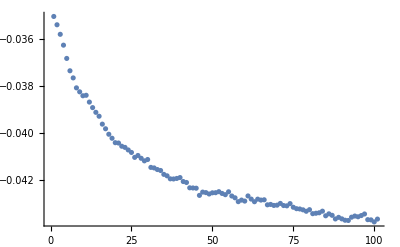

```mathematica
Show[ListPlot[Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

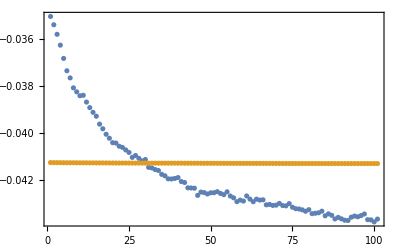

```mathematica
Show[ListPlot[{Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}],Table[Mean[HamB[[τ]]WB[[τ]]]/Mean[WB[[τ]]],{τ,1,101}]}],PlotRange->All,Axes->False,Frame->True]
```

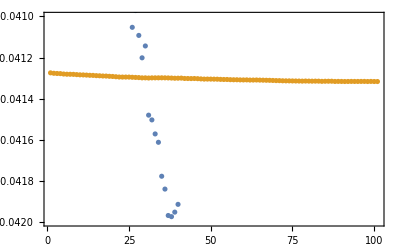

```mathematica
Show[ListPlot[{Table[Mean[HamA[[τ]]WA[[τ]]]/Mean[WA[[τ]]],{τ,1,101}],Table[Mean[HamB[[τ]]WB[[τ]]]/Mean[WB[[τ]]],{τ,1,101}]}],PlotRange->{-.042,-.041},Axes->False,Frame->True]
```

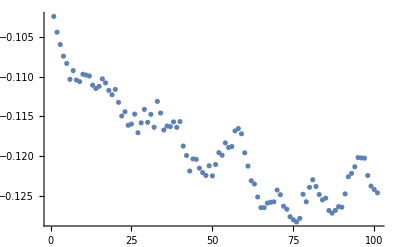

```mathematica
Show[ListPlot[Table[(Mean[HamI1[[τ]]WI1[[τ]]]/Mean[WI1[[τ]]])/Sqrt[Abs[Mean[HamI4[[τ]]WI4[[τ]]]/Mean[WI4[[τ]]]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

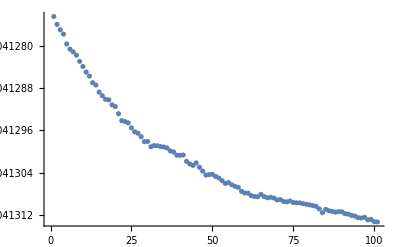

```mathematica
Show[ListPlot[Table[Mean[HamB[[τ]]],{τ,1,101}]],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

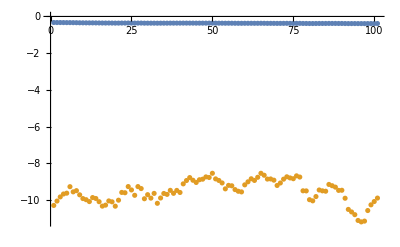

```mathematica
Show[ListPlot[{Table[Mean[HamI1[[τ]]],{τ,1,101}],Table[Mean[HamI4[[τ]]],{τ,1,101}]}],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

```mathematica
Show[ListPlot[{Table[Mean[HamI1[[τ]]],{τ,1,101}],Table[Mean[HamI4[[τ]]],{τ,1,101}]}],Plot[Exp[-(-.041)τ .4],{τ,0,101},PlotStyle->ColorData[97][2]]]
```

```mathematica
HamI1[[2]]/HamI4[[2]]
```

{0.236891,0.135178,0.0910462,0.17323,0.269617,0.152577,0.47073,0.147255,0.0930316,0.292298,0.262936,0.241183,0.19049,0.284223,0.158109,0.246722,0.235551,0.0434272,0.105923,0.0180886,0.0676614,0.374626,0.0817959,0.0878261,0.105855,0.171867,0.0206867,0.144502,0.519465,0.42177,0.135574,0.112091,0.377489,0.201073,0.24124,0.461732,0.232731,0.414285,0.131164,0.0990864,0.339216,0.124942,0.240982,0.0993528,0.0891989,0.562915,0.108236,0.296507,0.154117,0.0266005,0.347712,0.382427,0.560127,0.11585,0.0536705,0.231563,0.0819472,0.421139,0.274444,0.0730091,0.0209906,0.487703,0.407403,0.0643662,0.258551,0.3242,0.321571,0.026125,0.316878,0.216235,0.119577,0.144341,0.406563,0.248186,0.180856,0.118126,0.0826353,0.237735,0.161207,0.523131,0.114014,0.0947074,0.119403,0.296697,0.26897,0.524623,0.294271,0.0854158,0.235575,0.554181,0.355551,0.455356,0.328673,0.196951,0.0978243,0.291879,0.426767,0.0997843,0.313221,0.0965993,0.268912,0.192918,0.283285,0.262839,0.335327,0.289698,0.498508,0.345459,0.0914743,0.141342,0.364911,0.221494,0.0725396,0.0652226,0.0548016,0.489376,0.248581,0.0583012,0.408267,0.23855,0.141978,0.149051,0.560095,0.319623,0.22851,0.134237,0.102187,0.295379,0.42516,0.440098,0.526976,0.184806,0.422884,0.291295,0.421057,0.375509,0.313519,0.209797,0.558941,0.0715794,0.215255,0.152093,0.257224,0.0261109,0.14762,0.038181,0.178222,0.241998,0.241456,0.274268,0.604714,0.442578,0.297751,0.644835,0.0598956,0.235503,0.101983,0.311966,0.105119,0.125325,0.204607,0.478574,0.566032,0.127758,0.478599,0.214164,0.092354,0.26845,0.0981694,0.299567,0.0348552,0.352435,0.531241,0.380753,0.268734,0.294351,0.306101,0.205833,0.214312,0.246669,0.351284,0.0501709,0.1352,0.185562,0.39639,0.01036,0.397466,0.112719,0.117913,0.186839,0.120199,0.208367,0.210753,0.142833,0.55735,0.373152,0.225359,0.0668956,0.0664585,0.121974,0.195651,0.103146,0.0657541,0.177704,0.111517,0.1793,0.00848645,0.265675,0.126324,0.0931931,0.206687,0.0836483,0.172717,0.18878,0.113644,0.240103,0.148669,0.0424628,0.427195,0.313821,0.166383,0.254825,0.0804343,0.153912,0.191391,0.0747825,0.240492,0.277052,0.163131,0.0245689,0.0725263,0.210081,0.28698,0.260298,0.58469,0.2009,0.237629,0.121815,0.398126,0.227097,0.0602347,0.0605331,0.154778,0.233093,0.157267,0.379417,0.160132,0.106886,0.146252,0.179142,0.127506,0.246433,0.264007,0.107598,0.155043,0.176702,0.157122,0.384294,0.270106,0.380646,0.193116,0.19428,0.0956754,0.367669,0.117774,0.216095,0.145943,0.272219,0.266744,0.309764,0.463917,0.454741,0.284229,0.323515,0.327056,0.258948,0.119086,0.116995,0.353759,0.0683298,0.421574,0.175967,0.0669714,0.360213,0.476824,0.27498,0.060925,0.225211,0.221506,0.302324,0.259977,0.20918,0.39879,0.100555,0.265029,0.434895,0.0410671,0.221249,0.390559,0.257313,0.287531,0.194006,0.281009,0.309544,0.127021,0.427117,0.0184857,0.161841,0.565888,0.39557,0.228812,0.129184,0.369267,0.294849,0.273403,0.44175,0.281815,0.175423,0.0963334,0.0231733,0.185292,0.297658,0.158541,0.387383,0.268981,0.280431,0.291478,0.472407,0.534657,0.291538,0.347483,0.0305055,0.0339294,0.400201,0.287546,0.0618429,0.374841,0.11127,0.139009,0.402118,0.368198,0.117207,0.109737,0.0995427,0.26933,0.145443,0.0068002,0.164727,0.219373,0.0992558,0.220972,0.037432,0.394746,0.160419,0.199186,0.056032,0.204993,0.214596,0.301964,0.217873,0.24571,0.12585,0.0242508,0.321265,0.146252,0.152125,0.372811,0.0751245,0.0651058,0.344313,0.0880891,0.0791831,0.434222,0.123412,0.291413,0.420426,0.210395,0.106269,0.0723629,0.0823466,0.142273,0.0792024,0.0977661,0.333463,0.321115,0.225429,0.183213,0.234552,0.20603,0.266451,0.0858864,0.36153,0.26234,0.262604,0.180969,0.165127,0.2152,0.343372,0.352298,0.107565,0.0198307,0.504849,0.184039,0.189338,0.0207207,0.321963,0.262584,0.412273,0.238447,0.104065,0.0524591,0.085216,0.175622,0.251734,0.604819,0.260243,0.151385,0.0590711,0.372964,0.230762,0.0122336,0.304738,0.294033,0.155795,0.312687,0.143447,0.210451,0.072307,0.252394,0.336241,0.230033,0.341557,0.102252,0.314299,0.131988,0.422995,0.214933,0.359811,0.281576,0.320108,0.120743,0.0867263,0.187238,0.234773,0.306049,0.0739065,0.0522467,0.211286,0.363097,0.361588,0.59089,0.519391,0.199059,0.251186,0.299651,0.0754614,0.254181,0.0852881,0.213213,0.0760897,0.386844,0.174911,0.240192,0.0794655,0.461136,0.392067,0.159424,0.0685383,0.499991,0.495198,0.101063,0.192954,0.106181,0.38533,0.0831097,0.405969,0.218835,0.31015,0.323452,0.113571,0.129352,0.198628,0.0580479,0.321937,0.257358,0.21371,0.466375,0.130803,0.113978,0.47353,0.369241,0.178757,0.245519,0.163895,0.0780901,0.49894,0.105441,0.109098,0.248148,0.110112,0.0259559,0.291176,0.164463,0.319152,0.22223,0.283261,0.337674,0.0817137,0.0879247,0.372341,0.329022,0.123576,0.188808,0.201702,0.177212,0.300752,0.266648,0.271975,0.0332709,0.242814,0.484181,0.0154819,0.167674,0.113127,0.314004,0.00738208,0.375569,0.119773,0.310645,0.0841332,0.305693,0.314612,0.126926,0.392621,0.0683102,0.0266628,0.271382,0.184646,0.0774531,0.046804,0.392367,0.209659,0.424852,0.288436,0.0635802,0.178516,0.512453,0.48852,0.141598,0.48248,0.065531,0.38264,0.0151541,0.396314,0.069935,0.389883,0.355049,0.266716,0.419048,0.301588,0.286382,0.225301,0.225936,0.221638,0.224723,0.252037,0.218117,0.222211,0.0574284,0.305615,0.222953,0.520661,0.369299,0.0846169,0.310576,0.286117,0.217692,0.259398,0.24307,0.20792,0.174696,0.146092,0.47571,0.258422,0.106487,0.160786,0.165202,0.218106,0.605457,0.0975656,0.257523,0.0109891,0.162531,0.139064,0.480084,0.144182,0.191653,0.0234772,0.155104,0.118381,0.548185,0.269411,0.431187,0.112773,0.0975473,0.0482559,0.532556,0.166659,0.170404,0.0627955,0.0395322,0.324894,0.171925,0.224836,0.443141,0.289783,0.358144,0.259999,0.0848148,0.141309,0.254091,0.103071,0.105054,0.0277204,0.43959,0.0552951,0.254763,0.418698,0.0825624,0.479445,0.219551,0.0423525,0.159086,0.291694,0.046289,0.235328,0.040006,0.468712,0.0788209,0.266606,0.0616565,0.0708678,0.176699,0.0109717,0.0853175,0.0740813,0.386537,0.19028,0.327053,0.265216,0.331732,0.364808,0.449966,0.165108,0.0227741,0.0349421,0.11037,0.217726,0.222698,0.164033,0.105874,0.112135,0.29199,0.184438,0.397397,0.0704219,0.196778,0.042778,0.409811,0.312175,0.0654078,0.113191,0.264403,0.374001,0.258177,0.10188,0.423762,0.47898,0.0431354,0.185098,0.364192,0.184545,0.0740664,0.230147,0.29604,0.243766,0.164313,0.0610891,0.142085,0.248338,0.379585,0.357141,0.443006,0.350003,0.179984,0.343346,0.0661323,0.213506,0.179822,0.0636149,0.382421,0.172397,0.0756519,0.469682,0.376935,0.438177,0.177523,0.239579,0.319445,0.136458,0.176134,0.379615,0.352854,0.181821,0.14032,0.137111,0.181107,0.0843687,0.155132,0.351524,0.182171,0.118211,0.476625,0.213961,0.0418485,0.0322331,0.152487,0.552884,0.372507,0.125945,0.486973,0.517411,0.0945261,0.0500469,0.303891,0.34068,0.237395,0.128267,0.276362,0.663684,0.109602,0.110561,0.310935,0.0273537,0.218353,0.237676,0.223394,0.10429,0.232736,0.212322,0.0946018,0.109397,0.338461,0.454243,0.0687961,0.130012,0.251292,0.181823,0.0990857,0.103757,0.230211,0.330695,0.54141,0.453294,0.36119,0.277294,0.0298669,0.369365,0.352788,0.20661,0.043195,0.230225,0.438457,0.394,0.316591,0.061526,0.184489,0.377997,0.199053,0.0999818,0.114008,0.0522965,0.0458182,0.599181,0.577297,0.541151,0.114798,0.430572,0.491207,0.437048,0.201247,0.460989,0.429943,0.303425,0.0969425,0.29013,0.290208,0.236173,0.37826,0.336836,0.261234,0.129118,0.24897,0.453441,0.138284,0.293243,0.187144,0.264842,0.172053,0.350469,0.30148,0.212825,0.431256,0.283194,0.0278529,0.103124,0.310545,0.274242,0.497503,0.103771,0.233498,0.421388,0.354825,0.264204,0.374384,0.38365,0.145598,0.44424,0.219003,0.119996,0.312879,0.157519,0.237037,0.284385,0.334402,0.263834,0.327833,0.454929,0.0549501,0.196177,0.0740721,0.195213,0.446856,0.13322,0.121459,0.160533,0.0624681,0.40543,0.0566291,0.0887188,0.240922,0.0395833,0.176723,0.184246,0.094682,0.21055,0.181068,0.32842,0.553163,0.132536,0.321965,0.197486,0.0799717,0.256975,0.136532,0.262003,0.186867,0.0292108,0.231499,0.0309794,0.100983,0.313107,0.0911108,0.118547,0.650289,0.203816,0.278011,0.595723,0.00651923,0.2303,0.320191,0.574534,0.16766,0.326338,0.2811,0.1971,0.144087,0.165089,0.177902,0.0538488,0.412794,0.328807,0.0590307,0.389322,0.1558,0.233406,0.262969,0.187451,0.0322789,0.343415,0.0235133,0.497401,0.296478,0.0150333,0.0278863,0.0473476,0.201392,0.233641,0.512647,0.309501,0.165867,0.0637523,0.108494,0.0348239,0.540033,0.319067,0.344216,0.292365,0.309648,0.311268,0.248099,0.34814,0.587251,0.208277,0.367605,0.122994,0.32109,0.177256,0.190718,0.135257,0.443531,0.187135,0.337224,0.535807,0.23026,0.415198,0.0191928,0.0497294,0.157376,0.0675676,0.148034,0.196828,0.228351,0.164936,0.507433,0.158459,0.224507,0.401231,0.184185,0.0706165,0.172415,0.0598563,0.0633593,0.101038,0.122419,0.422857,0.211833,0.113275,0.0322894,0.510266,0.367111,0.353947,0.0955766,0.239555,0.127972,0.120233,0.067898,0.109026,0.100328,0.144859,0.312083,0.335462,0.497524,0.357832,0.404491,0.413771,0.171764,0.158061,0.281013,0.0720714,0.205823,0.151967,0.183912,0.229673,0.315347,0.340745,0.153252,0.106337,0.314397,0.366185,0.281072,0.188951,0.55339,0.30338,0.096095,0.185317,0.326753,0.518834,0.558748,0.443645}

```mathematica
Table[Eigenvalues[{{{Mean[WA[[τ]]],.22},{.22,Mean[WB[[τ]]]}},{{Mean[WA[[τ+1]]],.22},{.22,Mean[WB[[τ+1]]]}}}],{τ,1,100}]
```

{{0.987528,0.979986},{0.987645,0.980269},{0.988544,0.981787},{0.988706,0.982018},{0.986711,0.97965},{0.98837,0.982225},{0.988331,0.982133},{0.987176,0.980905},{0.986858,0.980608},{0.988452,0.982838},{0.988111,0.982375},{0.985576,0.979036},{0.98665,0.980498},{0.985072,0.978607},{0.985377,0.979149},{0.987508,0.981985},{0.98554,0.979565},{0.986666,0.981345},{0.984194,0.977971},{0.982937,0.976361},{0.986294,0.981159},{0.985378,0.980021},{0.984816,0.979323},{0.985493,0.98035},{0.986739,0.982158},{0.985008,0.979931},{0.984164,0.978913},{0.985991,0.981354},{0.986984,0.982316},{0.985132,0.980466},{0.984674,0.979748},{0.988156,0.984006},{0.98577,0.981544},{0.985446,0.981194},{0.985987,0.981955},{0.985733,0.981645},{0.985645,0.981564},{0.984558,0.980311},{0.985656,0.981147},{0.984794,0.980806},{0.984266,0.980159},{0.986263,0.98254},{0.985262,0.981494},{0.984433,0.980681},{0.985065,0.981006},{0.985441,0.982047},{0.985333,0.981988},{0.983378,0.979588},{0.984002,0.980439},{0.98518,0.981927},{0.98491,0.98149},{0.984389,0.981155},{0.986624,0.983822},{0.985332,0.982388},{0.983775,0.980474},{0.985697,0.982904},{0.984696,0.981347},{0.987667,0.984728},{0.985625,0.982972},{0.984712,0.981902},{0.984846,0.982109},{0.98462,0.981944},{0.985141,0.982526},{0.985441,0.982441},{0.985699,0.983276},{0.984622,0.982098},{0.987538,0.984551},{0.986869,0.983925},{0.985885,0.983472},{0.984215,0.981822},{0.983739,0.981072},{0.984075,0.981706},{0.98325,0.980323},{0.984506,0.981693},{0.985205,0.983158},{0.984466,0.981942},{0.985677,0.983763},{0.982183,0.979651},{0.984542,0.981891},{0.983347,0.980189},{0.984862,0.98144},{0.983772,0.981592},{0.984075,0.980815},{0.984728,0.982801},{0.98294,0.980126},{0.986294,0.984526},{0.986433,0.984327},{0.984091,0.982328},{0.985509,0.98299},{0.983444,0.981293},{0.984852,0.981465},{0.984353,0.982097},{0.984022,0.98228},{0.985798,0.984275},{0.985544,0.98411},{0.983868,0.982309},{0.986345,0.985019},{0.984325,0.981375},{0.984131,0.982688},{0.986134,0.983079}}

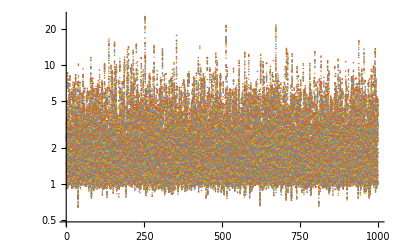

```mathematica
ListLogPlot[WA]
```

```mathematica
meanA=Mean[HamA*WA]/Mean[WA];
```

```mathematica
meanB=Mean[HamB*WB]/Mean[WB];
```

```mathematica
meanC=Mean[HamC*WC]/Mean[WC];
```

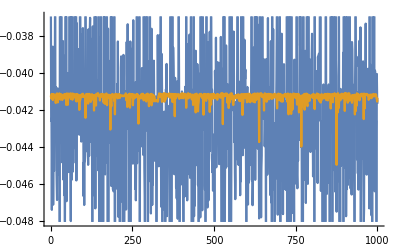

```mathematica
ListPlot[{meanA,meanB},Joined->True]
```

```mathematica
<n|m> = int dx psi_n(x) psi_m(x) = 0
```

```mathematica
for all x, psi_n(x) psi_m(x) >= 0
```

```mathematica
for some x, psi_n(x) psi_m(x) > 0
```

```mathematica
int dx psi_n(x)psi_m(x) > 0
```

```mathematica
I1=int A(x)B(x) / int |A(x)|^2=<B(x)/A(x)>_{prob=|A|^2}
```

```mathematica
I2=int A(x)B(x) / int |B(x)|^2=<A(x)/B(x)>_{prob=|B|^2}
```

```mathematica
I3=int |A(x)|^2 / int |B(x)|^2=<|A(x)/B(x)|^2>_{prob=|B|^2}
```

```mathematica
I4=int |B(x)|^2 / int |A(x)|^2=<|B(x)/A(x)|^2>_{prob=|A|^2}
```

```mathematica
ϵ=int A(x)B(x)/sqrt( int|A|^2 int |B|^2)=I1 Sqrt[I3]=I1/Sqrt[I4]
```

```mathematica
C(τ=0)={{<AA>,<AB>},{<BA>,<BB>}} = {{1,ϵ},{ϵ,1}}
```

```mathematica
C(τ)={{<AA(τ)>,<AB(τ)>},{<BA(τ)>,<BB(τ)>}}
```

```mathematica
C(τ)(C(τ0))^(-1)
```

```mathematica
Eigenvectors[{{1,ϵ},{ϵ,1}}]
```

{{-1,1},{1,1}}

```mathematica
Mean[meanA]
```

-0.0423889

```mathematica
StandardDeviation[meanA]
```

0.00410067

```mathematica
Mean[meanB]
```

-0.0413053

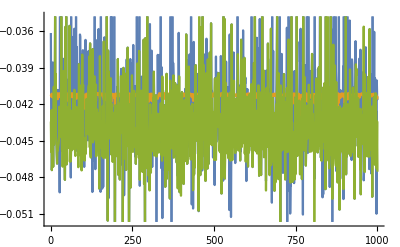

```mathematica
ListPlot[{meanA,meanB,meanC},Joined->True]
```

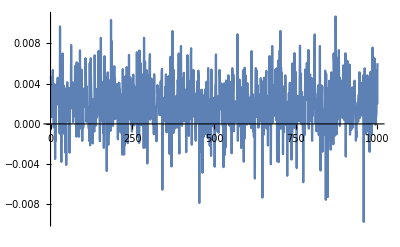

```mathematica
ListPlot[{1/2meanA+1/2meanB-meanC},Joined->True]
```

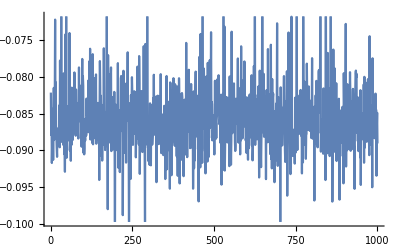

```mathematica
ListPlot[{1/2meanA+1/2meanB+meanC},Joined->True]
```